This notebook is for the calculation of dispersion relation with box spectrum

## Setting Defaults

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
pltcolors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pltDR[spect_]:=Show[
Plot[(#*x)&/@DeleteDuplicates@Flatten[{#[[1]]}&/@spectWC1],{x,-4.5,4.5},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,ImagePadding->{{20, 70}, {20, 20}},PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLabel->"Dispersion Relation for Spectrum "<>ToString[spect],AspectRatio->1],

ParametricPlot[
{
{n ConAxialSymOmegaNMAA[n,spect],ConAxialSymOmegaNMAA[n,spect]},
{n ConAxialSymOmegaNMZA[n,spect][[1]],ConAxialSymOmegaNMZA[n,spect][[1]]},
{n ConAxialSymOmegaNMZA[n,spect][[2]],ConAxialSymOmegaNMZA[n,spect][[2]]}
},
{n,-50,50},Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MAA","MZA+","MZA-"},{Left,Top}],PlotLabel->"Dispersion Relation",Exclusions->{1/0.3,1/0.9,1/0.6}]
]
```

```mathematica
pltDRMAAData[spect_,stepsize_:0.01]:=Table[
{n ConAxialSymOmegaNMAA[n,spect],ConAxialSymOmegaNMAA[n,spect]},
{n,-50,50,stepsize}
]
```

```mathematica
pltDRMZApData[spect_,stepsize_:0.01]:=Table[
{n ConAxialSymOmegaNMZA[n,spect][[1]],ConAxialSymOmegaNMZA[n,spect][[1]]},
{n,-50,50,stepsize}
]
pltDRMZAmData[spect_,stepsize_:0.01]:=Table[
{n ConAxialSymOmegaNMZA[n,spect][[2]],ConAxialSymOmegaNMZA[n,spect][[2]]},
{n,-50,50,stepsize}
]
```

```mathematica
pltOmegaN[spect_]:=Plot[
{
ConAxialSymOmegaNMAA[n,spect],
ConAxialSymOmegaNMZA[n,spect][[1]],
ConAxialSymOmegaNMZA[n,spect][[2]]
},
{n,-50,50},Frame->True,FrameLabel->{"n","ω"},ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MAA","MZA+","MZA-"},{Left,Top}],PlotLabel->"ω(n) Relation",
GridLines->{DeleteDuplicates@Flatten[#[[1]]&/@spect], None}
]

pltKN[spect_]:=Plot[
{
n ConAxialSymOmegaNMAA[n,spect],
n ConAxialSymOmegaNMZA[n,spect][[1]],
n ConAxialSymOmegaNMZA[n,spect][[2]]
},
{n,-50,50},Frame->True,FrameLabel->{"n","k"},ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MAA","MZA+","MZA-"},{Left,Top}],PlotLabel->"k(n) Relation",
GridLines->{DeleteDuplicates@Flatten[#[[1]]&/@spect], None}
]
```

```mathematica
pltDROmegaRealLSA[data_,drplot_,spect_:""]:=Show[
Graphics[
{Point[{#[[2]],#[[1]]}&/@data,VertexColors->colorf/@Rescale@(Abs@#[[3]]&/@data)],Inset[plotLegend[{Min@#,Max@#}&@(Abs@#[[3]]&/@data),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega.real"},
ImageSize->Large,
ImagePadding->{{20, 90}, {20, 20}},
AspectRatio->1,PlotRange->{{-4.5,4.5},{-4.5,4.5}}
],
drplot,
PlotLabel->"Dispersion Relation for Spectrum "<>ToString[spect]
]
```

Define color function for the plot legend of graphics

```mathematica
colorf=Blend[{Blue,Red},#]&;
colorRainbow=ColorData["Rainbow"];
colorTemp=ColorData["Temperature"];
plotLegend[{min_,max_},n_,col_]:=Graphics[{{col[(#-1)/(n-1)],Rectangle[{0,#-1},{1,#}]},{Black,Text[NumberForm[Rescale[#,{1,n},{min,max}],{4,2}],{3,#-.5},{1,0}]}}&/@Range@n,Frame->True,FrameTicks->None,PlotRangePadding->.5]
```

## Export Data

```mathematica
pltDRMAADataC1=Select[pltDRMAAData[spectC1,0.01],#[[1]]∈Reals&];//Quiet
```

```mathematica
pltDRMZApDataC1=Select[pltDRMZApData[spectC1,0.001],#[[1]]∈Reals&];//Quiet
```

```mathematica
pltDRMZAmDataC1=Select[pltDRMZAmData[spectC1,0.001],#[[1]]∈Reals&];//Quiet
```

```mathematica
pltDRMZADataC1=Sort[Join[pltDRMZApDataC1,pltDRMZAmDataC1],#1[[2]]<#2[[2]]&]
```

{{-1.48202,-1.4835},{-1.41734,-1.42018},{-1.37675,-1.3809},{-1.34645,-1.35186},3825,{0.527818,0.529406},{0.563764,0.564894},{0.623289,0.623913}}
 |  |  |  |

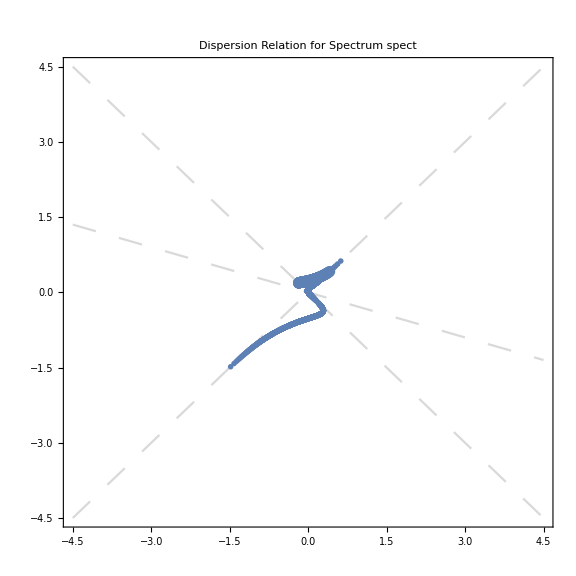

```mathematica
Show[
Plot[(#*x)&/@DeleteDuplicates@Flatten[{#[[1]]}&/@spectC1],{x,-4.5,4.5},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,ImagePadding->{{20, 70}, {20, 20}},PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLabel->"Dispersion Relation for Spectrum "<>ToString[spect],AspectRatio->1],
ListPlot[pltDRMAADataC1],
ListPlot[pltDRMZApDataC1],
ListPlot[pltDRMZAmDataC1]
]
```

```mathematica
Export["export/dr-cont-box/pltDRMAADataC1.csv",pltDRMAADataC1]
Export["export/dr-cont-box/pltDRMZApDataC1.csv",pltDRMZApDataC1]
Export["export/dr-cont-box/pltDRMZAmDataC1.csv",pltDRMZAmDataC1]
Export["export/dr-cont-box/pltDRMZADataC1.csv",pltDRMZADataC1]
Export["export/dr-cont-box/maalsadataC1Clean.csv",maalsadataC1Clean]
Export["export/dr-cont-box/mzaplsadataC1Clean.csv",mzaplsadataC1Clean]
Export["export/dr-cont-box/mzamlsadataC1Clean.csv",mzamlsadataC1Clean]
```

export/dr-cont-box/pltDRMAADataC1.csv

export/dr-cont-box/pltDRMZApDataC1.csv

export/dr-cont-box/pltDRMZAmDataC1.csv

export/dr-cont-box/pltDRMZADataC1.csv

export/dr-cont-box/maalsadataC1Clean.csv

export/dr-cont-box/mzaplsadataC1Clean.csv

export/dr-cont-box/mzamlsadataC1Clean.csv

if the plot itsef is really needed, the following code exports the plots.

```mathematica
pltDROmegaRealLSA[mzamlsadataC1Clean,pltDRC1]
```

-Graphics-

```mathematica
exp1=Plot[
Piecewise[{#[[2]],#[[1,1]]<x<#[[1,2]]}&/@spectC1],
{x,-1,1},Frame->True,Axes->True,FrameLabel->{"cosθ","g"},FrameLabel->"Spectrum",ImageSize->Large,PlotRange->{{-1,1},Full},AspectRatio->1
]
exp2=pltDROmegaRealLSA[maalsadataC1Clean,pltDRC1]
(*exp2=Show[pltDROmegaRealLSA[Select[mzamlsadataC1Clean,0.03<Abs@#[[3]]<1&],pltDRC1],FrameLabel->{k,ω}]*)
pltDR[spectC1]

Export["/Users/leima/github/dispersion-relation-paper/assets/boxspectrum-c1-spectrum.pdf",exp1]
Export["/Users/leima/github/dispersion-relation-paper/assets/boxspectrum-c1-dr-lsa.pdf",exp2]
```

K3r1DfIG8
MQkH/5DII/kT8LrmanmB0wKbCx9zDOoxOKfqrqoq1wwLL4nCGtkmOMIRKd77
cATOS02/Zhk3wvvPpG2NiTHA5wJZetncEFxGWNOJlyTc+XxnouQmZWvdU+6y
TMq/Qg2azF2UfasY7NaNlFeKgkyjkSRB+5sZXkTAJqVnMOVoUpDB9aO87c5R
H7EXZYWU7VY/G4RtmWZyTkxZwT1w/17zAMzzMGZw6JQL8+O86Rf74Vyj7lSt
uw9OqLi8QivVwydGv42ImDo4zby2qSdcC8cQlZ/sxc1w3MzBbFO2Al5zdXrJ
m7NlvP9u0bs0RcIWuIPfu3mLrh121D/JSRXq4OomTuXsCz38OqvEf31bHyzz
q/iY5jMA930YShpUkvDpd7GrSwMMcE1/kr+kxwjfamxTewpGYHrZEL+bYYKZ
mgZ9TYoZNtTJwxjXx2BxQ1RJgcUCJ1R6xr9dNQGPl7bPhRdPwq1hRY7Qz1Ow
WXV+w6IgKzwYkSx3S21wsDI5pKfDDj+oF32P++mASWL78Kt9Tjiv69DSoHIX
LJBrZcsF0/C//8O/AVRgw60=
     "]]}},
  AspectRatio->1,
  Axes->{True, True},
  AxesLabel->{None, None},
  AxesOrigin->{0, 0},
  DisplayFunction->Identity,
  Frame->{{True, True}, {True, True}},
  FrameLabel->{{
     FormBox["\"g\"", TraditionalForm], None}, {
     FormBox["\"cos\[Theta]\"", TraditionalForm], None}},
  FrameTicks->{{Automatic, Automatic}, {Automatic, Automatic}},
  GridLines->{None, None},
  GridLinesStyle->Directive[
    GrayLevel[0.5, 0.4]],
  ImageSize->Large,
  Method->{"DefaultBoundaryStyle" -> Automatic, "ScalingFunctions" -> None},
  PlotRange->{{-1, 1}, {-0.1, 1.}},
  PlotRangeClipping->True,
  PlotRangePadding->{{0, 0}, {
     Scaled[0.05], 
     Scaled[0.05]}},
  Ticks->{Automatic, Automatic}]], "Output",
 CellChangeTimes->{3.7072478981509323`*^9, 3.7072480582575693`*^9, 
  3.707481709513686*^9}],

Cell[BoxData[
 TagBox[
  GraphicsBox[{{{PointBox[CompressedData["
1:eJxTTMoPSmViYGAQBmIQ7Srx5xNDzqn9DBs+XvJNCrDnuay3MYL59H4GLx4m
7fY2+40Jr/MfzAfyDe6qsDVOtZ+tHHf6peOZ/QxWW06U7Ztvf6NOxfLKSyB/
keu2z3+X2H9IPxcuOOPsfgZ1Q441MqvsXRPiWbV9z+1vWCMTlWK93n7WtcmK
ZzjP7z8gwRLGp7vJ/m6ffenZc+f3O9z+WZe1Z4v92+t1c5f4Xdh/YO775ce8
t9uvN1x9MWb3hf0NCU8vKN3eaZ88447KVL2L+xmUwRrs

v+Hx05cX9DSDp
n/vs9/f+3qqif2k/Q8jjpbOPHLA/OfGTpeGhS/sdTON2efIcsu9du7rwasbl
/QvEbp77HnzYPlav8fhj3Sv7H3wPBmmwn/G800RK/ep+BZD046P2xccbbXc1
X9ufANTNpH3cHgB4jqL9
       "],
       VertexColors->{
         RGBColor[1., 0., 0.], 
         RGBColor[0.9647227435285481, 0., 0.03527725647145186], 
         RGBColor[0.9283178810875503, 0., 0.07168211891244969], 
         RGBColor[0.8906858074217248, 0., 0.10931419257827524`], 
         RGBColor[0.8517127891499947, 0., 0.1482872108500053], 
         RGBColor[0.8112679489398131, 0., 0.18873205106018687`], 
         RGBColor[0.7691993544303928, 0., 0.23080064556960722`], 
         RGBColor[0.7253288688272221, 0., 0.27467113117277786`], 
         RGBColor[0.6794452537642253, 0., 0.32055474623577473`], 
         RGBColor[0.6312947540356624, 0., 0.3687052459643376], 
         RGBColor[0.5805679723569233, 0., 0.41943202764307674`], 
         RGBColor[0.5268811481170279, 0., 0.4731188518829721], 
         RGBColor[0.46974879615683296`, 0., 0.530251203843167], 
         RGBColor[0.408542746617115, 0., 0.591457253382885], 
         RGBColor[0.34242969263267087`, 0., 0.6575703073673291], 
         RGBColor[0.27027637907332736`, 0., 0.7297236209266726], 
         RGBColor[0.19051863292299998`, 0., 0.809481367077], 
         RGBColor[0.10107662530285766`, 0., 0.8989233746971423], 
         RGBColor[0., 0., 1.]}], InsetBox[
       GraphicsBox[{{
          {RGBColor[0, 0, 1], RectangleBox[{0, 0}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.29\"\>",
              0.2852859011956183,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 0.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[1, 19], 0.05263157894736842], 0, 
            NCache[
             Rational[18, 19], 0.9473684210526315]], RectangleBox[{0, 1}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.31\"\>",
              0.31151660014590526`,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 1.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[2, 19], 0.10526315789473684`], 0, 
            NCache[
             Rational[17, 19], 0.8947368421052632]], RectangleBox[{0, 2}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.34\"\>",
              0.33774729909619217`,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 2.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[3, 19], 0.15789473684210525`], 0, 
            NCache[
             Rational[16, 19], 0.8421052631578947]], RectangleBox[{0, 3}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.36\"\>",
              0.3639779980464791,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 3.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[4, 19], 0.21052631578947367`], 0, 
            NCache[
             Rational[15, 19], 0.7894736842105263]], RectangleBox[{0, 4}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.39\"\>",
              0.390208696996766,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 4.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[5, 19], 0.2631578947368421], 0, 
            NCache[
             Rational[14, 19], 0.7368421052631579]], RectangleBox[{0, 5}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.42\"\>",
              0.4164393959470529,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 5.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[6, 19], 0.3157894736842105], 0, 
            NCache[
             Rational[13, 19], 0.6842105263157895]], RectangleBox[{0, 6}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.44\"\>",
              0.4426700948973399,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 6.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[7, 19], 0.3684210526315789], 0, 
            NCache[
             Rational[12, 19], 0.631578947368421]], RectangleBox[{0, 7}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.47\"\>",
              0.46890079384762684`,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 7.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[8, 19], 0.42105263157894735`], 0, 
            NCache[
             Rational[11, 19], 0.5789473684210527]], RectangleBox[{0, 8}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.50\"\>",
              0.49513149279791374`,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 8.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[9, 19], 0.47368421052631576`], 0, 
            NCache[
             Rational[10, 19], 0.5263157894736842]], RectangleBox[{0, 9}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.52\"\>",
              0.5213621917482006,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 9.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[10, 19], 0.5263157894736842], 0, 
            NCache[
             Rational[9, 19], 0.47368421052631576`]], 
           RectangleBox[{0, 10}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.55\"\>",
              0.5475928906984876,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 10.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[11, 19], 0.5789473684210527], 0, 
            NCache[
             Rational[8, 19], 0.42105263157894735`]], 
           RectangleBox[{0, 11}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.57\"\>",
              0.5738235896487744,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 11.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[12, 19], 0.631578947368421], 0, 
            NCache[
             Rational[7, 19], 0.3684210526315789]], RectangleBox[{0, 12}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.60\"\>",
              0.6000542885990614,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 12.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[13, 19], 0.6842105263157895], 0, 
            NCache[
             Rational[6, 19], 0.3157894736842105]], RectangleBox[{0, 13}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.63\"\>",
              0.6262849875493484,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 13.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[14, 19], 0.7368421052631579], 0, 
            NCache[
             Rational[5, 19], 0.2631578947368421]], RectangleBox[{0, 14}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.65\"\>",
              0.6525156864996353,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 14.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[15, 19], 0.7894736842105263], 0, 
            NCache[
             Rational[4, 19], 0.21052631578947367`]], 
           RectangleBox[{0, 15}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.68\"\>",
              0.6787463854499223,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 15.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[16, 19], 0.8421052631578947], 0, 
            NCache[
             Rational[3, 19], 0.15789473684210525`]], 
           RectangleBox[{0, 16}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.70\"\>",
              0.7049770844002091,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 16.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[17, 19], 0.8947368421052632], 0, 
            NCache[
             Rational[2, 19], 0.10526315789473684`]], 
           RectangleBox[{0, 17}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.73\"\>",
              0.7312077833504961,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 17.5}, {1, 0}]}}, {
          {RGBColor[
            NCache[
             Rational[18, 19], 0.9473684210526315], 0, 
            NCache[
             Rational[1, 19], 0.05263157894736842]], RectangleBox[{0, 18}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.76\"\>",
              0.7574384823007829,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 18.5}, {1, 0}]}}, {
          {RGBColor[1, 0, 0], RectangleBox[{0, 19}]}, 
          {GrayLevel[0], InsetBox[
            TagBox[
             InterpretationBox["\<\"0.78\"\>",
              0.7836691812510699,
              AutoDelete->True],
             NumberForm[#, {4, 2}]& ], {3, 19.5}, {1, 0}]}}},
        Frame->True,
        FrameTicks->None,
        PlotRangePadding->0.5], NCache[
       Scaled[{1, Rational[1, 2]}], Scaled[{1, 0.5}]], 
       ImageScaled[{-0.1, Rational[1, 2]}], NCache[
       Scaled[{Rational[1, 4], 0.9}], Scaled[{0.25, 0.9}]]]}, {{{}, {}, 
       {GrayLevel[0.85], AbsoluteThickness[1.6], Opacity[1.], Dashing[0.03], 
        LineBox[CompressedData["
1:eJw91PtPzXEcx/HvTk5KR/Vxjy21ZW7hh+SchM97htxOrqOVmXIrm+Uyl01E
Wa4Ro+QyInJpqBzJ7fNmlHs3ikOkWpI1x05rnZSwvfjhucd/8PSNip27XKdp
mvlPf92bmG3v7BQMqWR46iL/DsGQer+OfxzWJhjSGb95aTnNgiHdfOwYu/Sr
YEg1XUMSCssEQwra/9kz+bxgSA1H+ozsP0MwpLTyi706kjwZ0gVru+PeaQ+G
5PFzbeN1kztD8tpoDAjMMzCkcVmJ8fkhbgxJC/Dxe37PlSFZriQ1dA92YUg7
reuvh5Y5M6TmpTklPjP0DGnruQ3NtionhtRa7GSybdIxpJ4La8q32zWGdHDI
wXrvHp0KyqCwtjeLtXYFZWGko0tHe6uCMqlSH5w2okVBuUuX5zvf166gvJO+
2qP7NJuCMurFoYjSlY0Kyp5ea/pODq9TUC6IK3sYGVOloNx/IsTr0bBSBaXp
6tNR4babCsq09WbD5jrLP9X82anFRRmlEqqWw7XxO9o+SKimapVjws7VSajm
JB4ZmZfdKKFypA4wuA22SahcjTNL0kfbJVT1q2KT/d1bJFTVj351i3zXKqFK
j2mqXPf5p4Rq4NlXp3Zbfkmocg/veje+ViPIY70zlhTM0RHk0ru2In2BE0Eu
0mwVPEFPkDMPRNdsvexMkKsfpBy9NNqFIA9z+T7kQr4rQY44Vngr08eNIH97
abaJiwaCHGUO9dvR250gf/m00/RgiwdBrt8X2Gbc7kmQX8xcviAlUBDkrBhr
r9smQZATkmaV1wYLgmzioNnGiYIgZwa4T/8YKghyXP/88f7RgiAPb3AZ9OS4
IMjO+m21P04Jglzta88YkCEIcmpElXdsliDIuuKcfn1uCIJstYQblr0UBNlS
VvwsuUQQ5JTvk/bklwuCPGXoKGc3qyDIuSedtNx6QZCTCzbff//nC5CjK5ri
9E2CIHt7vnWE2QVBdvibbyW0CIL8etrDjdkOQZCvrTAGVrQLgv+/9e9jvwGZ
rl7L
         "]], LineBox[CompressedData["
1:eJwt1Pk/1HkcwPFpNI4c47M6NnpYNjaVUouMq89ndytLSckVtjK00bFttaQl
QjttSuEh0rkiIio00XS8v+QqWcYUa6SVYRxDhpmvNc7dfTz64fV4/QdPU+5h
z71MBoPh/l//PzGhUDE7iyg8tzExM5PGTSvTAy2nEVWzr9fRNp3GC97EVvtN
IGpL/exgUyqN/zDbkVGsRNTO1DUemudp/Kha5RDcj6hfTFINjsfQuEvDJb6m
GVH5Tt7XvIJpbH/+g37SbUSh8PYi9ioa96UtXG24GVGSnt6m3yglzhDdmT/N
06eM1oaUWL1V4FzxlOrZTTa1JiFk6ohqFLMnjww84OhRWtMdoPblKF4cYWdt
W6pDhXcKjHdwRrBTXkJsmYs29eyVkdRhlxwzrE3M6p9pUdbOVAol+Yj5d3l9
uo6a1FEbR7cCgyF8WnzswdZmdeqA/XNRFVeGlcHFTSabWdQ5pJnmn9SPT2aH
K+UdalTwPzvNTVt78XijGkd+nEm9sLyRz1suxQa+XaJTCgblZpsfss+3G1+0
uCg1/mwWzm5+Ko/M6cL2fhNvdzGmYNgmvZTV0IlrglRzp6fGQdBe1cyd6sC8
VpZjxqox0Ag71Gl0XYzPMEtNvUwVcOtadkC9sgU/yTzE1nWVQ5GsP/Jdoghz
X6cECPcNALsySqPufiM2WPzzoo3+3SAZGOzzPFiHfaKbK4PCOuCKW4xe1u0K
fP6qy+KqFUJoH/I2Ls98iDn3Xlr5yx+BvvD5zWbeVZxxzF0nspuPPcyS2wM3
XgGvbemNtVlCvHZV3O6zFnwYS5XExk28w7UjH2MNgyvge0brOr/sbuzDYIar
VdXB9oS01aWFAzikz9yDM6cJVOlGOtrL5HglX/CNLlcEWnZbmjJtFDinvaJG
pt0K0v2Hkyz1xnCRtDw/9LgYOqtm5gW1jeNcz/rcPGEHZIYNtR79MIktdCyM
IgWd8MWtP6//zp/Bm4K6UmQHu6Ak9Uybs4RBnCRvhZLvusHBOGvP4+1McsK3
gtyd7AHhU3kt67EaWR0teCoq6IVahryFWs8iTxoG58TF9EPOhdCukwXqJAUt
ipj+WgadFcmX8m00CYn/tXRGewhWaA5b5JZpkb3Zsuk97z5CwOWa8hwTbbI/
oMDx5SY5yBrc5eiODkmKmgzMWTsCXPetZnEL9MibtLoFvTqj0Pv3aU5FFJv4
8pZ4iyWjID1nO2F3Sp+46Omq2A0KeL1lr0+yLSIBF0/YFOUqIS9MPF/AQcSq
p7knskAJ8TwPkcQREaajZcaGe0rgUPbb7L5FJF/6XtXOV0KOtZ7b+62IjDtv
gHnVSog2LHO2DEXk0qCeW6hECSv7NM3rriDS4Jqze6kJDeqsGMnIdUSybk7r
Dy+lodNUkWWUhcgx2qdSsIyG9IAO48N5iBhmaZl7WtHAbCz+fOFDRMLGfxo4
tZ4GMd9fJ6QBEVaeffj7QBr4zY2vkpoQaZtK/apgDw3JwxvOlokQKfIcbA0P
oWHTcit1bTEiXjM3HHQP0lByTY1RIkXklvdchlMUDUmPI5+39yMScfeHYo1Y
GkJbhqJZQ4i4zinjiuJpMNb/S+WnQGSkMKx6fyINKkv38vgxRKqYLyLWXaDh
jWtlRKEKkct+SyyYqTTc/9HOtmUKkQP3wtsaLtHwyS/yyS/4FwkghfY=
         "]], 
        LineBox[CompressedData["
1:eJxF1P8z03EcwPHPbW1Nm23ypXC37E6XWPzA2pDqukq+TJTTjq4LKbrrVC65
i3y96YtFTlsqV4tQufKlGZXC+dIX2jeRlcLcQud8urmdzVDdtdf7h+c9/oMn
Oyn9UAoBwzDB3/55rbDBuLrq0GlT5SM5yllGOg/l9gotyAeeh6VNC8jWXnNQ
8gxycm1oQZ8GGVgywRQ/Qk5XuPi6RSCl2nqnZRETrNVZzR33GSBj6dxsI58O
umby/LktNHBHXWGuIpQKYv4enh877ED5U9G0fTAFLNJlNEZpyOBCcpPKI4IE
5lRfWMDHiOCiksjHLxJAxyOT2jwjBpZ6lRpY61ff2gwUWj4fw6xgX6J5zbJ1
ERSNkIKl20xgMaGFHcs2gq8qzzDsw3AwaeBmgvrULOjoenbDvvgpMC5b052Y
NgaW3A117fFWg/xn7/3i8VZQmiGgZU3Jd9mMjZYo+2Vq0FSuz823fAMPYCPb
hdVTYExhhW9LwyxolrjTqFtw0I4XqaoMMIKG0+liDt0EjvesrEscXQQr0+ZG
zk8sgZsefqq6Il8Bm8uLR0P02G6bQSzZ8fYYAqh+jfeT2olgP4YPd+4kgTU3
UidznpDB8a6yW48DKKA3Zd6rVmEHJtzua6vxoIK/BgW4Qz0NTBJEeeY708Gf
P4r4XZcYoOE618LLY4IDkSlxZVwHsC5N5/SSjywQHdTqg5H8zsBo3h5kjT89
/HsUMttNEcJJRfpMUza/u4Mkky7rf1chx9lGmbsMKUkYY6XXIQnKpo0uL5A6
eTztxCBSrlF+EKuQZfN7ryq0yP1b/chUHbL5HhFrNiDF7Vlvvs4gU4fnsklz
SBbzi1loRJo5grYCE3IorDuzwYx8fpLHHbYi/38L/ANTw1dL
         "]]}}, {{}, {}, 
       {RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6], 
        Opacity[1.], FaceForm[Opacity[0.3]], LineBox[CompressedData["
1:eJwBEQPu/CFib1JlAgAAADAAAAACAAAAF+56SDRcx78zm6Fa6mPHP5LsM4KD
Xce/VsW55OF3xz+MXMts5hTHv5XeEPPk6cc//+lI3Bqhxr+C1V0YITXIPzkF
MMHKG8a/cX++mQ1yyD8sxkxcxYvFv8PQYrT2psg/uI94YzX0xL9UFcqgv9bI
PxFrEwflVsS/e7R+owgDyT/tbJf987TDv1qQ6OTYLMk/lbcqGyMPw79kYjH6
41TJP5pNFDz5ZcK/8vsEbqt7yT/Uvm9b17nBv6YE3syQock/IgKdkrRZwL9D
uLeh1uvJP3wEX64D/Lq/VRZT8rx/yj8j2hfmloO5v+SbYYJopco/ia4YYQgH
uL8iEghelMvKPyP1zl9zAbW/UlHvjM0Zyz9BwDZk/YStv5PXCDswwMs/NoCJ
ee1Gdb81LJwPokfNP9+c32jBDV0/6+5BaOB/zT/1x5EM1h6CP9Pxp5Ycus0/
8Yfndavmlz/cXdgIFzXOP701zlPmmKs/FvZT4npJzz+3S/WjxLOvPxRix/wC
ls8/zhvtoY3ysT+0b680+OXPPy/UeU3bSLY/WBwCK6NI0D/HUFYd3aW/P8Wd
80mnD9E/7V6ribIUwT+htv3ggEjRP1/GNgP6YMI/h2Au7siE0T/+0yf6ch3F
P1bagS09CdI/zpKoSE2Qxj85NU6XZVLSP14kCvQVE8g/LPKMbP+g0j/K6AWG
IFHLP8ItatzbUdM/x749wAUSzT8W5S8kUrbTP8NKGP2D7s4/0Y/8i8wk1D9X
U3BybIjRP0MICp0AKdU/QM4yi8az0j+5jWIzxMXVP0eL6ERX/9M/0/kWTAh8
1j9nwDvWRjLXP6SMxXiLadg/sVA/m7Ba1z8rYKo+roPYP496a37rg9c/XJmq
LIme2D/whHnIDNnXP6/YoEic1tg/lxxXzPiP2D9WOL4sF1LZPy+eE3OVT9o/
XHBnWjiU2j8bY5d7jpXaPyjVhGO1ydo/pxf4N8/h2j9aEfARPgXbP49BjGJW
pds/xf9A0nOm2z91m4qUaq3bP01SYiinrds/w7yQzQ==
         "]]}, 
       {RGBColor[0.880722, 0.611041, 0.142051], AbsoluteThickness[1.6], 
        Opacity[1.], FaceForm[Opacity[0.3]], LineBox[CompressedData["
1:eJwBYQOe/CFib1JlAgAAADUAAAACAAAAigdjFiy6yD9lp6gHbfrKv1GYvM1b
L84/jOsXqRWw0L9Z+K7Umk3RPyaPz0c1zNO/8EGZHPAo0j8Ib7Ba3YbVvwS8
yTMmfdI/IwELYXW81r9yVeDatYbSP3JS/Kq8qte/NstaSJJg0j+VpgHL32zY
v9hz6Ks0GdI/UgKwJFcR2b+T/GrFSLnRP9ZyLaDCoNm/PMnMPmVG0T+O00nM
riDavwhBB8xVxNA/7lYKfOKU2r/0wgLCyDXQP/x5wgYNANu/D2rFN2M5zz/9
ShGYKGTbvx1AHZYI9c0/9iNDErXC27+USA9KtaDMPyxOow7dHNy/N4Tc3Rk+
yz98R68NjnPcv8VePPeEzsk/+FxO0IjH3L8mhYrXQ8zGP594F96/ad2/OUh1
bL5LwD/eKU2Lj6Pevy5jiQjAHYg/KKAxG+qX4L9RjHmZT4Nwv0sbczAsxOC/
nnDwmA+olL8ImXTslvHgvy23RZ8dZqu/fLCufGZQ4b/hUqVo7Py/v4ybGaTk
IeK/a5VjI6lswr9jOuL3XVviv+A+2pmT68S/zRhqIUaX4r9DE0/1bCDKv9hA
GSVZF+O/qUMcqybJ0r8kh+tnJ0Hkv6yVSrLqWNS/AtEDSKGW5L9RxoaP1PjV
v5ofR/SW8eS/QcjAnZRw2b9MEqFX7rrlv9XyeLYWTdu/iHZFJjAr5r+BI4G1
TkPdv6rCoLDGpOa/w1iRy57G4L8thZwGtLrnvya9SgAE9uG/P4gB7q9b6L/F
IPov2j3jvySLXG3BD+m/4Rzx+eEv5r80rL1F9Mbqv72OTPRk7ue/g1jCISTc
678TVmXjZ/Ppv1DegB+lLe2/rbfjp1eV778XBAyvk57wv4msHo4l5u+/wUnG
Sua98L//wJhg/Rzwv5FjnBGl3vC/vkblr/518L9pWpGuAyXxv4srhqrxQvG/
ECHe9FzL8b9i35H4sn3xv7Uq9U4m/PG/j/QU7HO88b/iGQDwyTDyv4R5KNky
SfK/wNgVFtGo8r/IsSgY487zv4IjR1uPAvS/ALfVt/he9L8kCvBE74b0v8rB
ICuYG/W/DaYPmWo39b8Lib/HoTz2v5MD9jmzS/a/6C8yti8m+r+RBPexPSf6
v5tAuoSy9Pu/SzWVtO/0+78fyNrt
         "]]}, 
       {RGBColor[0.560181, 0.691569, 0.194885], AbsoluteThickness[1.6], 
        Opacity[1.], FaceForm[Opacity[0.3]], LineBox[CompressedData["
1:eJwBQQO+/CFib1JlAgAAADMAAAACAAAAxYo+niTrwz+zrDYmVbvFv0TkRmlz
ELw/lU+awt8Hv79MN3ceqviwP3IGTbIFa7O/Q276Nipapj9kMs0wEn+qv7rw
mjTtm50/uJqdE5o0or/Yi/1ZGtKFP8B59+WFAI2/TXD2CiQxcz/gZz5VEpV6
v44eSJjA0gE/ABA6EpbFCb+CZZUgbbBtv2C4Baaoc3Y/wrmPWk6oer+Q1VNK
eyGFP/L+0QNQ94G/8NV9ws3sjT8F4RUYjZCFv8AIbxrg6pI/x90oFe9LiL84
VQui3IOWP3NBBLsZS4q/YH0DxQHSmT9EoUp8L6iLv4C52rRY4pw/xAM7Ysl3
jL9YrWQkR7+fP2UIRRpUyoy/yLOClZ04oT8mALl7B62Mv2A6QYmSf6I/t8SN
npkqjL9AhZzGZ7ejP/GrSrDCS4u/YPODbZDipD8jyGhvnxeKvyR1jOElA6Y/
joGepfuTiL9gkiKC+hqnPwNIVwmLxYa/YBC8NKgrqD+Kh7b+FLCEvwRymt2b
Nqk/7hqNYpZWgr8Y1veRHj2qP2NNY0i3dn+/+NzXFl1Aqz/XDdykKcB5v/h6
ShluQaw/lL/FmcmLc7+YohtyV0GtP8EX/3eUtla/4KA4NpFBrz8j3ptQ7sY/
P64ekeLfIbA/SEX1YsxJZD/yAAUJRaSwP+F58UqR+3s/cAwUwteusT+PdFxT
GJCRPwgEfZc56bM/gHxHizaWlD/KSvTL44K0P4oYab8vyJc/mAeTOFAitT+g
+Kk+jbyePwAkudCvdbY/KdqI48Cxpz/0Sr/vAIy5P4nuT6MhxtA/Efekyjen
0T+vt77l6RbRP69mxK088NE/3Q6MhR5s0T+MWxztgT3SPxwRoi7hJdI/SLgD
Kdbm0j/9dGoR1evTP5YT/HlFidQ/65sMUQZ11D8osJQq6wjVPzo+8QooC9U/
1pbWzi+V1T8efnXxwGnWP46+z/bz3tY/xYp7emGc2j9UrU24zOHaP88VKOjF
UNw/Rn62TFKI3D/d15I8wqreP4B1XkAu094/+CbSB3VB4T9mO0NkJk3hP0Me
2AkJp+g/XgmtkQeo6D/H5el0+jvsP04YyEA4POw/6M2XAQ==
         "]]}}}}, InsetBox[
     TemplateBox[{"\"MAA\"","\"MZA+\"","\"MZA-\""},
      "LineLegend",
      DisplayFunction->(FormBox[
        StyleBox[
         StyleBox[
          PaneBox[
           TagBox[
            GridBox[{{
               TagBox[
                GridBox[{{
                   GraphicsBox[{{
                    Directive[
                    PointSize[0.5], 
                    EdgeForm[None], 
                    Opacity[1.], 
                    AbsoluteThickness[1.6], 
                    FaceForm[
                    Opacity[0.3]], 
                    RGBColor[0.368417, 0.506779, 0.709798]], {
                    LineBox[{{0, 10}, {20, 10}}]}}, {
                    Directive[
                    PointSize[0.5], 
                    EdgeForm[None], 
                    Opacity[1.], 
                    AbsoluteThickness[1.6], 
                    FaceForm[
                    Opacity[0.3]], 
                    RGBColor[0.368417, 0.506779, 0.709798]], {}}}, 
                    AspectRatio -> Full, ImageSize -> {20, 10}, 
                    PlotRangePadding -> None, ImagePadding -> Automatic, 
                    BaselinePosition -> (Scaled[0.1] -> Baseline)], #}, {
                   GraphicsBox[{{
                    Directive[
                    PointSize[0.5], 
                    EdgeForm[None], 
                    Opacity[1.], 
                    AbsoluteThickness[1.6], 
                    FaceForm[
                    Opacity[0.3]], 
                    RGBColor[0.880722, 0.611041, 0.142051]], {
                    LineBox[{{0, 10}, {20, 10}}]}}, {
                    Directive[
                    PointSize[0.5], 
                    EdgeForm[None], 
                    Opacity[1.], 
                    AbsoluteThickness[1.6], 
                    FaceForm[
                    Opacity[0.3]], 
                    RGBColor[0.880722, 0.611041, 0.142051]], {}}}, 
                    AspectRatio -> Full, ImageSize -> {20, 10}, 
                    PlotRangePadding -> None, ImagePadding -> Automatic, 
                    BaselinePosition -> (Scaled[0.1] -> Baseline)], #2}, {
                   GraphicsBox[{{
                    Directive[
                    PointSize[0.5], 
                    EdgeForm[None], 
                    Opacity[1.], 
                    AbsoluteThickness[1.6], 
                    FaceForm[
                    Opacity[0.3]], 
                    RGBColor[0.560181, 0.691569, 0.194885]], {
                    LineBox[{{0, 10}, {20, 10}}]}}, {
                    Directive[
                    PointSize[0.5], 
                    EdgeForm[None], 
                    Opacity[1.], 
                    AbsoluteThickness[1.6], 
                    FaceForm[
                    Opacity[0.3]], 
                    RGBColor[0.560181, 0.691569, 0.194885]], {}}}, 
                    AspectRatio -> Full, ImageSize -> {20, 10}, 
                    PlotRangePadding -> None, ImagePadding -> Automatic, 
                    BaselinePosition -> (Scaled[0.1] -> Baseline)], #3}}, 
                 GridBoxAlignment -> {
                  "Columns" -> {Center, Left}, "Rows" -> {{Baseline}}}, 
                 AutoDelete -> False, 
                 GridBoxDividers -> {
                  "Columns" -> {{False}}, "Rows" -> {{False}}}, 
                 GridBoxItemSize -> {"Columns" -> {{All}}, "Rows" -> {{All}}},
                  GridBoxSpacings -> {
                  "Columns" -> {{0.5}}, "Rows" -> {{0.8}}}], "Grid"]}}, 
             GridBoxAlignment -> {"Columns" -> {{Left}}, "Rows" -> {{Top}}}, 
             AutoDelete -> False, 
             GridBoxItemSize -> {
              "Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, 
             GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{0}}}], 
            "Grid"], Alignment -> Left, AppearanceElements -> None, 
           ImageMargins -> {{5, 5}, {5, 5}}, ImageSizeAction -> 
           "ResizeToFit"], LineIndent -> 0, StripOnInput -> False], {
         FontFamily -> "Arial"}, Background -> Automatic, StripOnInput -> 
         False], TraditionalForm]& ),
      Editable->True,
      InterpretationFunction:>(RowBox[{"LineLegend", "[", 
         RowBox[{
           RowBox[{"{", 
             RowBox[{
               RowBox[{"Directive", "[", 
                 RowBox[{
                   RowBox[{"EdgeForm", "[", "None", "]"}], ",", 
                   RowBox[{"Opacity", "[", "1.`", "]"}], ",", 
                   RowBox[{"AbsoluteThickness", "[", "1.6`", "]"}], ",", 
                   RowBox[{"FaceForm", "[", 
                    RowBox[{"Opacity", "[", "0.3`", "]"}], "]"}], ",", 
                   InterpretationBox[
                    ButtonBox[
                    TooltipBox[
                    RowBox[{
                    GraphicsBox[{{
                    GrayLevel[0], 
                    RectangleBox[{0, 0}]}, {
                    GrayLevel[0], 
                    RectangleBox[{1, -1}]}, {
                    RGBColor[0.368417, 0.506779, 0.709798], 
                    RectangleBox[{0, -1}, {2, 1}]}}, AspectRatio -> 1, Frame -> 
                    True, FrameStyle -> 
                    RGBColor[
                    0.24561133333333335`, 0.3378526666666667, 
                    0.4731986666666667], FrameTicks -> None, PlotRangePadding -> 
                    None, ImageSize -> 
                    Dynamic[{
                    Automatic, 1.35 CurrentValue["FontCapHeight"]/
                    AbsoluteCurrentValue[Magnification]}]], 
                    "\[InvisibleSpace]"}], 
                    "RGBColor[0.368417, 0.506779, 0.709798]"], Appearance -> 
                    None, BaseStyle -> {}, BaselinePosition -> Baseline, 
                    DefaultBaseStyle -> {}, ButtonFunction :> 
                    With[{Typeset`box$ = EvaluationBox[]}, 
                    If[
                    Not[
                    AbsoluteCurrentValue["Deployed"]], 
                    SelectionMove[Typeset`box$, All, Expression]; 
                    FrontEnd`Private`$ColorSelectorInitialAlpha = 1; 
                    FrontEnd`Private`$ColorSelectorInitialColor = 
                    RGBColor[0.368417, 0.506779, 0.709798]; 
                    FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; 
                    MathLink`CallFrontEnd[
                    FrontEnd`AttachCell[Typeset`box$, 
                    FrontEndResource["RGBColorValueSelector"], {
                    0, {Left, Bottom}}, {Left, Top}, 
                    "ClosingActions" -> {
                    "SelectionDeparture", "ParentChanged", 
                    "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> 
                    Automatic, Method -> "Preemptive"], 
                    RGBColor[0.368417, 0.506779, 0.709798], Editable -> False,
                     Selectable -> False]}], "]"}], ",", 
               RowBox[{"Directive", "[", 
                 RowBox[{
                   RowBox[{"EdgeForm", "[", "None", "]"}], ",", 
                   RowBox[{"Opacity", "[", "1.`", "]"}], ",", 
                   RowBox[{"AbsoluteThickness", "[", "1.6`", "]"}], ",", 
                   RowBox[{"FaceForm", "[", 
                    RowBox[{"Opacity", "[", "0.3`", "]"}], "]"}], ",", 
                   InterpretationBox[
                    ButtonBox[
                    TooltipBox[
                    RowBox[{
                    GraphicsBox[{{
                    GrayLevel[0], 
                    RectangleBox[{0, 0}]}, {
                    GrayLevel[0], 
                    RectangleBox[{1, -1}]}, {
                    RGBColor[0.880722, 0.611041, 0.142051], 
                    RectangleBox[{0, -1}, {2, 1}]}}, AspectRatio -> 1, Frame -> 
                    True, FrameStyle -> 
                    RGBColor[
                    0.587148, 0.40736066666666665`, 0.09470066666666668], 
                    FrameTicks -> None, PlotRangePadding -> None, ImageSize -> 
                    Dynamic[{
                    Automatic, 1.35 CurrentValue["FontCapHeight"]/
                    AbsoluteCurrentValue[Magnification]}]], 
                    "\[InvisibleSpace]"}], 
                    "RGBColor[0.880722, 0.611041, 0.142051]"], Appearance -> 
                    None, BaseStyle -> {}, BaselinePosition -> Baseline, 
                    DefaultBaseStyle -> {}, ButtonFunction :> 
                    With[{Typeset`box$ = EvaluationBox[]}, 
                    If[
                    Not[
                    AbsoluteCurrentValue["Deployed"]], 
                    SelectionMove[Typeset`box$, All, Expression]; 
                    FrontEnd`Private`$ColorSelectorInitialAlpha = 1; 
                    FrontEnd`Private`$ColorSelectorInitialColor = 
                    RGBColor[0.880722, 0.611041, 0.142051]; 
                    FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; 
                    MathLink`CallFrontEnd[
                    FrontEnd`AttachCell[Typeset`box$, 
                    FrontEndResource["RGBColorValueSelector"], {
                    0, {Left, Bottom}}, {Left, Top}, 
                    "ClosingActions" -> {
                    "SelectionDeparture", "ParentChanged", 
                    "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> 
                    Automatic, Method -> "Preemptive"], 
                    RGBColor[0.880722, 0.611041, 0.142051], Editable -> False,
                     Selectable -> False]}], "]"}], ",", 
               RowBox[{"Directive", "[", 
                 RowBox[{
                   RowBox[{"EdgeForm", "[", "None", "]"}], ",", 
                   RowBox[{"Opacity", "[", "1.`", "]"}], ",", 
                   RowBox[{"AbsoluteThickness", "[", "1.6`", "]"}], ",", 
                   RowBox[{"FaceForm", "[", 
                    RowBox[{"Opacity", "[", "0.3`", "]"}], "]"}], ",", 
                   InterpretationBox[
                    ButtonBox[
                    TooltipBox[
                    RowBox[{
                    GraphicsBox[{{
                    GrayLevel[0], 
                    RectangleBox[{0, 0}]}, {
                    GrayLevel[0], 
                    RectangleBox[{1, -1}]}, {
                    RGBColor[0.560181, 0.691569, 0.194885], 
                    RectangleBox[{0, -1}, {2, 1}]}}, AspectRatio -> 1, Frame -> 
                    True, FrameStyle -> 
                    RGBColor[
                    0.37345400000000006`, 0.461046, 0.12992333333333334`], 
                    FrameTicks -> None, PlotRangePadding -> None, ImageSize -> 
                    Dynamic[{
                    Automatic, 1.35 CurrentValue["FontCapHeight"]/
                    AbsoluteCurrentValue[Magnification]}]], 
                    "\[InvisibleSpace]"}], 
                    "RGBColor[0.560181, 0.691569, 0.194885]"], Appearance -> 
                    None, BaseStyle -> {}, BaselinePosition -> Baseline, 
                    DefaultBaseStyle -> {}, ButtonFunction :> 
                    With[{Typeset`box$ = EvaluationBox[]}, 
                    If[
                    Not[
                    AbsoluteCurrentValue["Deployed"]], 
                    SelectionMove[Typeset`box$, All, Expression]; 
                    FrontEnd`Private`$ColorSelectorInitialAlpha = 1; 
                    FrontEnd`Private`$ColorSelectorInitialColor = 
                    RGBColor[0.560181, 0.691569, 0.194885]; 
                    FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; 
                    MathLink`CallFrontEnd[
                    FrontEnd`AttachCell[Typeset`box$, 
                    FrontEndResource["RGBColorValueSelector"], {
                    0, {Left, Bottom}}, {Left, Top}, 
                    "ClosingActions" -> {
                    "SelectionDeparture", "ParentChanged", 
                    "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> 
                    Automatic, Method -> "Preemptive"], 
                    RGBColor[0.560181, 0.691569, 0.194885], Editable -> False,
                     Selectable -> False]}], "]"}]}], "}"}], ",", 
           RowBox[{"{", 
             RowBox[{#, ",", #2, ",", #3}], "}"}], ",", 
           RowBox[{"LegendMarkers", "\[Rule]", "None"}], ",", 
           RowBox[{"LabelStyle", "\[Rule]", 
             RowBox[{"{", "}"}]}], ",", 
           RowBox[{"LegendLayout", "\[Rule]", "\"Column\""}]}], "]"}]& )], 
     Scaled[{0.01, 0.99}], ImageScaled[{0, 1}],
     BaseStyle->{FontSize -> Larger},
     FormatType->StandardForm]},
   AspectRatio->1,
   Axes->True,
   DisplayFunction->Identity,
   Frame->True,
   FrameLabel->{
     FormBox["\"k.real\"", TraditionalForm], 
     FormBox["\"omega.real\"", TraditionalForm]},
   ImagePadding->{{20, 90}, {20, 20}},
   ImageSize->Large,
   PlotLabel->FormBox[
    "\"Dispersion Relation for Spectrum \"", TraditionalForm],
   PlotRange->{{-4.5, 4.5}, {-4.5, 4.5}}],
  InterpretTemplate[Legended[
    Graphics[{{
       Point[CompressedData["
1:eJxTTMoPSmViYGAQBmIQ7Srx5xNDzqn9DBs+XvJNCrDnuay3MYL59H4GLx4m
7fY2+40Jr/MfzAfyDe6qsDVOtZ+tHHf6peOZ/QxWW06U7Ztvf6NOxfLKSyB/
keu2z3+X2H9IPxcuOOPsfgZ1Q441MqvsXRPiWbV9z+1vWCMTlWK93n7WtcmK
ZzjP7z8gwRLGp7vJ/m6ffenZc+f3O9z+WZe1Z4v92+t1c5f4Xdh/YO775ce8
t9uvN1x9MWb3hf0NCU8vKN3eaZ88447KVL2L+xmUwRrs380v+Hx05cX9DSDp
n/vs9/f+3qqif2k/Q8jjpbOPHLA/OfGTpeGhS/sdTON2efIcsu9du7rwasbl
/QvEbp77HnzYPlav8fhj3Sv7H3wPBmmwn/G800RK/ep+BZD046P2xccbbXc1
X9ufANTNpH3cHgB4jqL9
        "], VertexColors -> {
          RGBColor[1., 0., 0.], 
          RGBColor[0.9647227435285481, 0., 0.03527725647145186], 
          RGBColor[0.9283178810875503, 0., 0.07168211891244969], 
          RGBColor[0.8906858074217248, 0., 0.10931419257827524`], 
          RGBColor[0.8517127891499947, 0., 0.1482872108500053], 
          RGBColor[0.8112679489398131, 0., 0.18873205106018687`], 
          RGBColor[0.7691993544303928, 0., 0.23080064556960722`], 
          RGBColor[0.7253288688272221, 0., 0.27467113117277786`], 
          RGBColor[0.6794452537642253, 0., 0.32055474623577473`], 
          RGBColor[0.6312947540356624, 0., 0.3687052459643376], 
          RGBColor[0.5805679723569233, 0., 0.41943202764307674`], 
          RGBColor[0.5268811481170279, 0., 0.4731188518829721], 
          RGBColor[0.46974879615683296`, 0., 0.530251203843167], 
          RGBColor[0.408542746617115, 0., 0.591457253382885], 
          RGBColor[0.34242969263267087`, 0., 0.6575703073673291], 
          RGBColor[0.27027637907332736`, 0., 0.7297236209266726], 
          RGBColor[0.19051863292299998`, 0., 0.809481367077], 
          RGBColor[0.10107662530285766`, 0., 0.8989233746971423], 
          RGBColor[0., 0., 1.]}], 
       Inset[
        Graphics[{{{
            RGBColor[0, 0, 1], 
            Rectangle[{0, 0}, {1, 1}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.2852859011956183, {4, 2}], {3, 0.5}, {1, 0}]}}, {{
            RGBColor[
             Rational[1, 19], 0, 
             Rational[18, 19]], 
            Rectangle[{0, 1}, {1, 2}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.31151660014590526`, {4, 2}], {3, 1.5}, {1, 0}]}}, {{
           
            RGBColor[
             Rational[2, 19], 0, 
             Rational[17, 19]], 
            Rectangle[{0, 2}, {1, 3}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.33774729909619217`, {4, 2}], {3, 2.5}, {1, 0}]}}, {{
           
            RGBColor[
             Rational[3, 19], 0, 
             Rational[16, 19]], 
            Rectangle[{0, 3}, {1, 4}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.3639779980464791, {4, 2}], {3, 3.5}, {1, 0}]}}, {{
            RGBColor[
             Rational[4, 19], 0, 
             Rational[15, 19]], 
            Rectangle[{0, 4}, {1, 5}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.390208696996766, {4, 2}], {3, 4.5}, {1, 0}]}}, {{
            RGBColor[
             Rational[5, 19], 0, 
             Rational[14, 19]], 
            Rectangle[{0, 5}, {1, 6}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.4164393959470529, {4, 2}], {3, 5.5}, {1, 0}]}}, {{
            RGBColor[
             Rational[6, 19], 0, 
             Rational[13, 19]], 
            Rectangle[{0, 6}, {1, 7}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.4426700948973399, {4, 2}], {3, 6.5}, {1, 0}]}}, {{
            RGBColor[
             Rational[7, 19], 0, 
             Rational[12, 19]], 
            Rectangle[{0, 7}, {1, 8}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.46890079384762684`, {4, 2}], {3, 7.5}, {1, 0}]}}, {{
           
            RGBColor[
             Rational[8, 19], 0, 
             Rational[11, 19]], 
            Rectangle[{0, 8}, {1, 9}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.49513149279791374`, {4, 2}], {3, 8.5}, {1, 0}]}}, {{
           
            RGBColor[
             Rational[9, 19], 0, 
             Rational[10, 19]], 
            Rectangle[{0, 9}, {1, 10}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.5213621917482006, {4, 2}], {3, 9.5}, {1, 0}]}}, {{
            RGBColor[
             Rational[10, 19], 0, 
             Rational[9, 19]], 
            Rectangle[{0, 10}, {1, 11}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.5475928906984876, {4, 2}], {3, 10.5}, {1, 0}]}}, {{
            RGBColor[
             Rational[11, 19], 0, 
             Rational[8, 19]], 
            Rectangle[{0, 11}, {1, 12}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.5738235896487744, {4, 2}], {3, 11.5}, {1, 0}]}}, {{
            RGBColor[
             Rational[12, 19], 0, 
             Rational[7, 19]], 
            Rectangle[{0, 12}, {1, 13}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.6000542885990614, {4, 2}], {3, 12.5}, {1, 0}]}}, {{
            RGBColor[
             Rational[13, 19], 0, 
             Rational[6, 19]], 
            Rectangle[{0, 13}, {1, 14}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.6262849875493484, {4, 2}], {3, 13.5}, {1, 0}]}}, {{
            RGBColor[
             Rational[14, 19], 0, 
             Rational[5, 19]], 
            Rectangle[{0, 14}, {1, 15}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.6525156864996353, {4, 2}], {3, 14.5}, {1, 0}]}}, {{
            RGBColor[
             Rational[15, 19], 0, 
             Rational[4, 19]], 
            Rectangle[{0, 15}, {1, 16}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.6787463854499223, {4, 2}], {3, 15.5}, {1, 0}]}}, {{
            RGBColor[
             Rational[16, 19], 0, 
             Rational[3, 19]], 
            Rectangle[{0, 16}, {1, 17}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.7049770844002091, {4, 2}], {3, 16.5}, {1, 0}]}}, {{
            RGBColor[
             Rational[17, 19], 0, 
             Rational[2, 19]], 
            Rectangle[{0, 17}, {1, 18}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.7312077833504961, {4, 2}], {3, 17.5}, {1, 0}]}}, {{
            RGBColor[
             Rational[18, 19], 0, 
             Rational[1, 19]], 
            Rectangle[{0, 18}, {1, 19}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.7574384823007829, {4, 2}], {3, 18.5}, {1, 0}]}}, {{
            RGBColor[1, 0, 0], 
            Rectangle[{0, 19}, {1, 20}]}, {
            GrayLevel[0], 
            Text[
             NumberForm[0.7836691812510699, {4, 2}], {3, 19.5}, {1, 0}]}}}, 
         Frame -> True, FrameTicks -> None, PlotRangePadding -> 0.5], 
        Scaled[{1, 
          Rational[1, 2]}], 
        ImageScaled[{-0.1, 
          Rational[1, 2]}], 
        Scaled[{
          Rational[1, 4], 0.9}]]}, {{{{}, {}, {
          Directive[
           Opacity[1.], 
           AbsoluteThickness[1.6], 
           GrayLevel[0.85], 
           Dashing[0.03]], 
          Line[CompressedData["
1:eJw91PtPzXEcx/HvTk5KR/Vxjy21ZW7hh+SchM97htxOrqOVmXIrm+Uyl01E
Wa4Ro+QyInJpqBzJ7fNmlHs3ikOkWpI1x05rnZSwvfjhucd/8PSNip27XKdp
mvlPf92bmG3v7BQMqWR46iL/DsGQer+OfxzWJhjSGb95aTnNgiHdfOwYu/Sr
YEg1XUMSCssEQwra/9kz+bxgSA1H+ozsP0MwpLTyi706kjwZ0gVru+PeaQ+G
5PFzbeN1kztD8tpoDAjMMzCkcVmJ8fkhbgxJC/Dxe37PlSFZriQ1dA92YUg7
reuvh5Y5M6TmpTklPjP0DGnruQ3NtionhtRa7GSybdIxpJ4La8q32zWGdHDI
wXrvHp0KyqCwtjeLtXYFZWGko0tHe6uCMqlSH5w2okVBuUuX5zvf166gvJO+
2qP7NJuCMurFoYjSlY0Kyp5ea/pODq9TUC6IK3sYGVOloNx/IsTr0bBSBaXp
6tNR4babCsq09WbD5jrLP9X82anFRRmlEqqWw7XxO9o+SKimapVjws7VSajm
JB4ZmZfdKKFypA4wuA22SahcjTNL0kfbJVT1q2KT/d1bJFTVj351i3zXKqFK
j2mqXPf5p4Rq4NlXp3Zbfkmocg/veje+ViPIY70zlhTM0RHk0ru2In2BE0Eu
0mwVPEFPkDMPRNdsvexMkKsfpBy9NNqFIA9z+T7kQr4rQY44Vngr08eNIH97
abaJiwaCHGUO9dvR250gf/m00/RgiwdBrt8X2Gbc7kmQX8xcviAlUBDkrBhr
r9smQZATkmaV1wYLgmzioNnGiYIgZwa4T/8YKghyXP/88f7RgiAPb3AZ9OS4
IMjO+m21P04Jglzta88YkCEIcmpElXdsliDIuuKcfn1uCIJstYQblr0UBNlS
VvwsuUQQ5JTvk/bklwuCPGXoKGc3qyDIuSedtNx6QZCTCzbff//nC5CjK5ri
9E2CIHt7vnWE2QVBdvibbyW0CIL8etrDjdkOQZCvrTAGVrQLgv+/9e9jvwGZ
rl7L
           "]], 
          Line[CompressedData["
1:eJwt1Pk/1HkcwPFpNI4c47M6NnpYNjaVUouMq89ndytLSckVtjK00bFttaQl
QjttSuEh0rkiIio00XS8v+QqWcYUa6SVYRxDhpmvNc7dfTz64fV4/QdPU+5h
z71MBoPh/l//PzGhUDE7iyg8tzExM5PGTSvTAy2nEVWzr9fRNp3GC97EVvtN
IGpL/exgUyqN/zDbkVGsRNTO1DUemudp/Kha5RDcj6hfTFINjsfQuEvDJb6m
GVH5Tt7XvIJpbH/+g37SbUSh8PYi9ioa96UtXG24GVGSnt6m3yglzhDdmT/N
06eM1oaUWL1V4FzxlOrZTTa1JiFk6ohqFLMnjww84OhRWtMdoPblKF4cYWdt
W6pDhXcKjHdwRrBTXkJsmYs29eyVkdRhlxwzrE3M6p9pUdbOVAol+Yj5d3l9
uo6a1FEbR7cCgyF8WnzswdZmdeqA/XNRFVeGlcHFTSabWdQ5pJnmn9SPT2aH
K+UdalTwPzvNTVt78XijGkd+nEm9sLyRz1suxQa+XaJTCgblZpsfss+3G1+0
uCg1/mwWzm5+Ko/M6cL2fhNvdzGmYNgmvZTV0IlrglRzp6fGQdBe1cyd6sC8
VpZjxqox0Ag71Gl0XYzPMEtNvUwVcOtadkC9sgU/yTzE1nWVQ5GsP/Jdoghz
X6cECPcNALsySqPufiM2WPzzoo3+3SAZGOzzPFiHfaKbK4PCOuCKW4xe1u0K
fP6qy+KqFUJoH/I2Ls98iDn3Xlr5yx+BvvD5zWbeVZxxzF0nspuPPcyS2wM3
XgGvbemNtVlCvHZV3O6zFnwYS5XExk28w7UjH2MNgyvge0brOr/sbuzDYIar
VdXB9oS01aWFAzikz9yDM6cJVOlGOtrL5HglX/CNLlcEWnZbmjJtFDinvaJG
pt0K0v2Hkyz1xnCRtDw/9LgYOqtm5gW1jeNcz/rcPGEHZIYNtR79MIktdCyM
IgWd8MWtP6//zp/Bm4K6UmQHu6Ak9Uybs4RBnCRvhZLvusHBOGvP4+1McsK3
gtyd7AHhU3kt67EaWR0teCoq6IVahryFWs8iTxoG58TF9EPOhdCukwXqJAUt
ipj+WgadFcmX8m00CYn/tXRGewhWaA5b5JZpkb3Zsuk97z5CwOWa8hwTbbI/
oMDx5SY5yBrc5eiODkmKmgzMWTsCXPetZnEL9MibtLoFvTqj0Pv3aU5FFJv4
8pZ4iyWjID1nO2F3Sp+46Omq2A0KeL1lr0+yLSIBF0/YFOUqIS9MPF/AQcSq
p7knskAJ8TwPkcQREaajZcaGe0rgUPbb7L5FJF/6XtXOV0KOtZ7b+62IjDtv
gHnVSog2LHO2DEXk0qCeW6hECSv7NM3rriDS4Jqze6kJDeqsGMnIdUSybk7r
Dy+lodNUkWWUhcgx2qdSsIyG9IAO48N5iBhmaZl7WtHAbCz+fOFDRMLGfxo4
tZ4GMd9fJ6QBEVaeffj7QBr4zY2vkpoQaZtK/apgDw3JwxvOlokQKfIcbA0P
oWHTcit1bTEiXjM3HHQP0lByTY1RIkXklvdchlMUDUmPI5+39yMScfeHYo1Y
GkJbhqJZQ4i4zinjiuJpMNb/S+WnQGSkMKx6fyINKkv38vgxRKqYLyLWXaDh
jWtlRKEKkct+SyyYqTTc/9HOtmUKkQP3wtsaLtHwyS/yyS/4FwkghfY=
           "]], 
          Line[CompressedData["
1:eJxF1P8z03EcwPHPbW1Nm23ypXC37E6XWPzA2pDqukq+TJTTjq4LKbrrVC65
i3y96YtFTlsqV4tQufKlGZXC+dIX2jeRlcLcQud8urmdzVDdtdf7h+c9/oMn
Oyn9UAoBwzDB3/55rbDBuLrq0GlT5SM5yllGOg/l9gotyAeeh6VNC8jWXnNQ
8gxycm1oQZ8GGVgywRQ/Qk5XuPi6RSCl2nqnZRETrNVZzR33GSBj6dxsI58O
umby/LktNHBHXWGuIpQKYv4enh877ED5U9G0fTAFLNJlNEZpyOBCcpPKI4IE
5lRfWMDHiOCiksjHLxJAxyOT2jwjBpZ6lRpY61ff2gwUWj4fw6xgX6J5zbJ1
ERSNkIKl20xgMaGFHcs2gq8qzzDsw3AwaeBmgvrULOjoenbDvvgpMC5b052Y
NgaW3A117fFWg/xn7/3i8VZQmiGgZU3Jd9mMjZYo+2Vq0FSuz823fAMPYCPb
hdVTYExhhW9LwyxolrjTqFtw0I4XqaoMMIKG0+liDt0EjvesrEscXQQr0+ZG
zk8sgZsefqq6Il8Bm8uLR0P02G6bQSzZ8fYYAqh+jfeT2olgP4YPd+4kgTU3
UidznpDB8a6yW48DKKA3Zd6rVmEHJtzua6vxoIK/BgW4Qz0NTBJEeeY708Gf
P4r4XZcYoOE618LLY4IDkSlxZVwHsC5N5/SSjywQHdTqg5H8zsBo3h5kjT89
/HsUMttNEcJJRfpMUza/u4Mkky7rf1chx9lGmbsMKUkYY6XXIQnKpo0uL5A6
eTztxCBSrlF+EKuQZfN7ryq0yP1b/chUHbL5HhFrNiDF7Vlvvs4gU4fnsklz
SBbzi1loRJo5grYCE3IorDuzwYx8fpLHHbYi/38L/ANTw1dL
           "]]}}}, {{{}, {}, {
          Directive[
           Opacity[1.], 
           AbsoluteThickness[1.6], 
           FaceForm[
            Opacity[0.3]], 
           RGBColor[0.368417, 0.506779, 0.709798]], 
          Line[CompressedData["
1:eJwBEQPu/CFib1JlAgAAADAAAAACAAAAF+56SDRcx78zm6Fa6mPHP5LsM4KD
Xce/VsW55OF3xz+MXMts5hTHv5XeEPPk6cc//+lI3Bqhxr+C1V0YITXIPzkF
MMHKG8a/cX++mQ1yyD8sxkxcxYvFv8PQYrT2psg/uI94YzX0xL9UFcqgv9bI
PxFrEwflVsS/e7R+owgDyT/tbJf987TDv1qQ6OTYLMk/lbcqGyMPw79kYjH6
41TJP5pNFDz5ZcK/8vsEbqt7yT/Uvm9b17nBv6YE3syQock/IgKdkrRZwL9D
uLeh1uvJP3wEX64D/Lq/VRZT8rx/yj8j2hfmloO5v+SbYYJopco/ia4YYQgH
uL8iEghelMvKPyP1zl9zAbW/UlHvjM0Zyz9BwDZk/YStv5PXCDswwMs/NoCJ
ee1Gdb81LJwPokfNP9+c32jBDV0/6+5BaOB/zT/1x5EM1h6CP9Pxp5Ycus0/
8Yfndavmlz/cXdgIFzXOP701zlPmmKs/FvZT4npJzz+3S/WjxLOvPxRix/wC
ls8/zhvtoY3ysT+0b680+OXPPy/UeU3bSLY/WBwCK6NI0D/HUFYd3aW/P8Wd
80mnD9E/7V6ribIUwT+htv3ggEjRP1/GNgP6YMI/h2Au7siE0T/+0yf6ch3F
P1bagS09CdI/zpKoSE2Qxj85NU6XZVLSP14kCvQVE8g/LPKMbP+g0j/K6AWG
IFHLP8ItatzbUdM/x749wAUSzT8W5S8kUrbTP8NKGP2D7s4/0Y/8i8wk1D9X
U3BybIjRP0MICp0AKdU/QM4yi8az0j+5jWIzxMXVP0eL6ERX/9M/0/kWTAh8
1j9nwDvWRjLXP6SMxXiLadg/sVA/m7Ba1z8rYKo+roPYP496a37rg9c/XJmq
LIme2D/whHnIDNnXP6/YoEic1tg/lxxXzPiP2D9WOL4sF1LZPy+eE3OVT9o/
XHBnWjiU2j8bY5d7jpXaPyjVhGO1ydo/pxf4N8/h2j9aEfARPgXbP49BjGJW
pds/xf9A0nOm2z91m4qUaq3bP01SYiinrds/w7yQzQ==
           "]]}, {
          Directive[
           Opacity[1.], 
           AbsoluteThickness[1.6], 
           FaceForm[
            Opacity[0.3]], 
           RGBColor[0.880722, 0.611041, 0.142051]], 
          Line[CompressedData["
1:eJwBYQOe/CFib1JlAgAAADUAAAACAAAAigdjFiy6yD9lp6gHbfrKv1GYvM1b
L84/jOsXqRWw0L9Z+K7Umk3RPyaPz0c1zNO/8EGZHPAo0j8Ib7Ba3YbVvwS8
yTMmfdI/IwELYXW81r9yVeDatYbSP3JS/Kq8qte/NstaSJJg0j+VpgHL32zY
v9hz6Ks0GdI/UgKwJFcR2b+T/GrFSLnRP9ZyLaDCoNm/PMnMPmVG0T+O00nM
riDavwhBB8xVxNA/7lYKfOKU2r/0wgLCyDXQP/x5wgYNANu/D2rFN2M5zz/9
ShGYKGTbvx1AHZYI9c0/9iNDErXC27+USA9KtaDMPyxOow7dHNy/N4Tc3Rk+
yz98R68NjnPcv8VePPeEzsk/+FxO0IjH3L8mhYrXQ8zGP594F96/ad2/OUh1
bL5LwD/eKU2Lj6Pevy5jiQjAHYg/KKAxG+qX4L9RjHmZT4Nwv0sbczAsxOC/
nnDwmA+olL8ImXTslvHgvy23RZ8dZqu/fLCufGZQ4b/hUqVo7Py/v4ybGaTk
IeK/a5VjI6lswr9jOuL3XVviv+A+2pmT68S/zRhqIUaX4r9DE0/1bCDKv9hA
GSVZF+O/qUMcqybJ0r8kh+tnJ0Hkv6yVSrLqWNS/AtEDSKGW5L9RxoaP1PjV
v5ofR/SW8eS/QcjAnZRw2b9MEqFX7rrlv9XyeLYWTdu/iHZFJjAr5r+BI4G1
TkPdv6rCoLDGpOa/w1iRy57G4L8thZwGtLrnvya9SgAE9uG/P4gB7q9b6L/F
IPov2j3jvySLXG3BD+m/4Rzx+eEv5r80rL1F9Mbqv72OTPRk7ue/g1jCISTc
678TVmXjZ/Ppv1DegB+lLe2/rbfjp1eV778XBAyvk57wv4msHo4l5u+/wUnG
Sua98L//wJhg/Rzwv5FjnBGl3vC/vkblr/518L9pWpGuAyXxv4srhqrxQvG/
ECHe9FzL8b9i35H4sn3xv7Uq9U4m/PG/j/QU7HO88b/iGQDwyTDyv4R5KNky
SfK/wNgVFtGo8r/IsSgY487zv4IjR1uPAvS/ALfVt/he9L8kCvBE74b0v8rB
ICuYG/W/DaYPmWo39b8Lib/HoTz2v5MD9jmzS/a/6C8yti8m+r+RBPexPSf6
v5tAuoSy9Pu/SzWVtO/0+78fyNrt
           "]]}, {
          Directive[
           Opacity[1.], 
           AbsoluteThickness[1.6], 
           FaceForm[
            Opacity[0.3]], 
           RGBColor[0.560181, 0.691569, 0.194885]], 
          Line[CompressedData["
1:eJwBQQO+/CFib1JlAgAAADMAAAACAAAAxYo+niTrwz+zrDYmVbvFv0TkRmlz
ELw/lU+awt8Hv79MN3ceqviwP3IGTbIFa7O/Q276Nipapj9kMs0wEn+qv7rw
mjTtm50/uJqdE5o0or/Yi/1ZGtKFP8B59+WFAI2/TXD2CiQxcz/gZz5VEpV6
v44eSJjA0gE/ABA6EpbFCb+CZZUgbbBtv2C4Baaoc3Y/wrmPWk6oer+Q1VNK
eyGFP/L+0QNQ94G/8NV9ws3sjT8F4RUYjZCFv8AIbxrg6pI/x90oFe9LiL84
VQui3IOWP3NBBLsZS4q/YH0DxQHSmT9EoUp8L6iLv4C52rRY4pw/xAM7Ysl3
jL9YrWQkR7+fP2UIRRpUyoy/yLOClZ04oT8mALl7B62Mv2A6QYmSf6I/t8SN
npkqjL9AhZzGZ7ejP/GrSrDCS4u/YPODbZDipD8jyGhvnxeKvyR1jOElA6Y/
joGepfuTiL9gkiKC+hqnPwNIVwmLxYa/YBC8NKgrqD+Kh7b+FLCEvwRymt2b
Nqk/7hqNYpZWgr8Y1veRHj2qP2NNY0i3dn+/+NzXFl1Aqz/XDdykKcB5v/h6
ShluQaw/lL/FmcmLc7+YohtyV0GtP8EX/3eUtla/4KA4NpFBrz8j3ptQ7sY/
P64ekeLfIbA/SEX1YsxJZD/yAAUJRaSwP+F58UqR+3s/cAwUwteusT+PdFxT
GJCRPwgEfZc56bM/gHxHizaWlD/KSvTL44K0P4oYab8vyJc/mAeTOFAitT+g
+Kk+jbyePwAkudCvdbY/KdqI48Cxpz/0Sr/vAIy5P4nuT6MhxtA/Efekyjen
0T+vt77l6RbRP69mxK088NE/3Q6MhR5s0T+MWxztgT3SPxwRoi7hJdI/SLgD
Kdbm0j/9dGoR1evTP5YT/HlFidQ/65sMUQZ11D8osJQq6wjVPzo+8QooC9U/
1pbWzi+V1T8efnXxwGnWP46+z/bz3tY/xYp7emGc2j9UrU24zOHaP88VKOjF
UNw/Rn62TFKI3D/d15I8wqreP4B1XkAu094/+CbSB3VB4T9mO0NkJk3hP0Me
2AkJp+g/XgmtkQeo6D/H5el0+jvsP04YyEA4POw/6M2XAQ==
           "]]}}}}}, {
     PlotLabel -> "Dispersion Relation for Spectrum ", Axes -> True, Frame -> 
      True, ImageSize -> Large, FrameLabel -> {"k.real", "omega.real"}, 
      ImageSize -> Large, ImagePadding -> {{20, 90}, {20, 20}}, AspectRatio -> 
      1, PlotRange -> {{-4.5, 4.5}, {-4.5, 4.5}}}], 
    Placed[
     Unevaluated[
      LineLegend[{
        Directive[
         EdgeForm[None], 
         Opacity[1.], 
         AbsoluteThickness[1.6], 
         FaceForm[
          Opacity[0.3]], 
         RGBColor[0.368417, 0.506779, 0.709798]], 
        Directive[
         EdgeForm[None], 
         Opacity[1.], 
         AbsoluteThickness[1.6], 
         FaceForm[
          Opacity[0.3]], 
         RGBColor[0.880722, 0.611041, 0.142051]], 
        Directive[
         EdgeForm[None], 
         Opacity[1.], 
         AbsoluteThickness[1.6], 
         FaceForm[
          Opacity[0.3]], 
         RGBColor[0.560181, 0.691569, 0.194885]]}, {"MAA", "MZA+", "MZA-"}, 
       LegendMarkers -> None, LabelStyle -> {}, LegendLayout -> "Column"]], {
     Left, Top}, Identity]]& ],
  AutoDelete->True,
  Editable->True,
  SelectWithContents->False,
  Selectable->True]], "Output",
 CellChangeTimes->{3.7072478981509323`*^9, 3.7072480582575693`*^9, 
  3.70748170963634*^9},ImageCache->GraphicsData["CompressedBitmap", "\<\
eJztfQe8VMX1//p2X6GoiGBU1AdRiV1j79iNYgyW5GcHJRpiikSxF1AUozEm
CAJWRLGhIgFRLDQxIgQrIAoWsKCxYANL1Nz/fM+dc9/s7rlzZ+7e5WH+bz+f
d2HvTvme77QzZ2bO/Pzkfn1O/cPJ/X7b++TOB595ct8+v+19VueDzjhTvcqv
lsvle6m/1Tvn8P8gl+NHyac3HmWvf8hvL6L/54Mvv/wyWL58OX2jH94OAx2q
f3///feD0047LVi6d

qH736KOP0jv1lyvQMx+MGTOGs8ldS886Svv6668P
+vTpE/zhD38Irr322uCDDz5wTeZ6AcJ9yeg+++yz4I9//GMwbNgwlezLL7+s
wxWjqw/uvvvuYMCAAcEnn3wS/Oc//wluuumm4Jprrgn++9//5oY4pmWBeBD9
0xD861//CqZOnRr9jR8/noKOGzcueOWVVxj1rFmzgt/+9rfB9OnTo9y/+uor
4m327Nm5Gv0OaH/zm98Er776ak6KO9wt2zEhyD11Ch999FFw3XXX4U/JiWdt
cOONN0Y154orrgjOOusshUL9T4UAb0itf//+wYQJE66KTSZvJqOFKBA4AB47
dizoHqyjv/XWW5SqklF9C99deOGFwYwZM+jbUDn69VpkDZL+xV8JyBKRP//8
cyJD/akk8WwdTJw4MRJ5zpw5wTnnnBOsWLGCvhtFfHVsEnkzCS1DIZg/fz7V
oltvvRV4/65/fOmllyhFVfkicQcNGhQ8+OCDRuUqiz5U118LQK6DB+uGiKp9
8803lwYboTNdvHgxZaAaX47BgWPUM7QGBofWMXr0aPo2TIh7vT27ElDodc4+
++zg2WefNUPdoBOeOXMmAVCVIvc3/e61116jYErkCNTAgQOpEPBtuBB3qD07
Depn9E8tlQnq0MKFC8s6FqTwzDPPoFlGzREdxxlnnIG+LEKJJspxGWW/fv2o
GeLbdY7pXW/BpGEfoqvIqFGjgssuu4x/ZsTffPNN0LdvX/AR5YBKi8aj0ESI
VSETN5MmTYrCLVmyhJL797//HXVISekNk+GUgEW3dv755/Ov1+v6jK7/oosu
Ikog6pAhQ6hmLVu2TNfKOvrtzDPPDObNm0c1D4U/ePBglySGybmXDCiqa6Sa
A465OkNCVGmUy+mnn05tVKV+nS4e1bUEl1xyCWU0fPhwKs6EqCOE3DSQd40i
4X5kqPBuhPCOnmHzWskqxYYaDaqv7o9KQ+4fhtyA/ilQSDWG0R/3YDGB8xSA
NYWA/ofHE3hcaQKopd84WZ107sc6FYoXfnKbZPxu45WQx6qUb2d6FswCLyuN
PPfVpKzU0DNvFnauUUj5BuHdCMd3Utwwj9qyCoe6JMDFJxxeyuFutBLghnnU
FcF94403GHIR4oIZEyEk0PT8pZCT8UO9mB0+ZSzVFuVpY4ueR8dlfLRQLDrj
aGgxI11hgij+qUYnpWtaUdu3S3+UBUReiGQBkU8CEcvEkRYQBT8QhSQQR8WB
OMICotYPRG0SiCPjQPSwgKjzA1GXBOKIOBC/sICo9wNRnwSiRxyIwy0gGvxA
NCSB+EUciJ9bQLTyA9EqCcThcSAOs4Bo7QciDF6IQJj9XGz+3S35t/HLn4LX
RFnG8n6oJcu2flnS8wR7RmWErJ5lHt0jodfIMtnjWxJrSawlMffEOul33KlE
Pe/eWWYQqwfukakYloFkTyESPXc3CODeVFLoLZlvkJR5rJS76Zhmlw5rJ0x/
Uk4axDr6J9O0J6mErJrHAttdiETPXQVgDuy4AtsoCdhuccB2sQBrjAfWnv5J
NH9Lyn1jEtZd47DubMHaOR4rK3IVGt8lWTonybJLnCw7WWTpIkQipeY8vKop
lqoC+7pUk7okSbRznEQ7WiSSTEOSVnk2nqvh1Wrh/0jUtemfWHs3iUHz5cTi
2CkO/A4W8JQq2QAkrdAOOcYaLjG/cRL4HePAb28BLxmV3JnvoFOWTOOSDJsk
ybBDnAw/tciwaUUydKR/yozlEvxNk+BvHwd/Owv8rpnAL7GnS/C7JsH/aRz8
bS3wf1IRfB7BTBO8hP0nMdgxchsMC9i3sWDfrCLsksbAKTJONagkcLu1Bd/m
mePjFJFbEYxY/ray4Nsic3z0jFW2t9Y/QGdjDFuuZAzbCAyubB4kbb0lv/+9
/MgEtBGW+w5tybkl51UkZ54slq0yS5OsqqMJp4OFyKDAC4vNDMiiZjXGoTKX
7/kHyZZhR8rTw08//TT4+OOP6Vt7/Q5z3K+//pq+reUsEZtNYiWSTBT05J0D
rDxgJ5BkGrJLFBJWRxIdfvjhQT6fD9q0aRPsv//+2IvE+7tOOOGE4Mc/prlk
cPXVV9fRFtIG2qiCDzarHHjggUHr1q2DNdZYI/jlL3+JFNs507B7Eg2xzZTN
ZZIO5V/AIR31tCdxq622Ct59911S/4899thgn332ob1iNZqyBx54IPjb32iD
UfDee++R4D169CgEjz32mOIGQPD5+c9/znxQHTn44IORnDs3eyRxs4EQiZ7r
W7jxrypcE2H2QBW5++67o3Xsd955J1httdVoi1SdfnfnnXcGtbW1wYgRI6J5
B7hEpVm0aFFRXFQ7xF3TmZU9k1jpJESi53oWVvZKzcpzzz2HRgFpcmyv2njj
jclyEtaXgFrSvffeS6ycd955qE0F/eOyZctQb2iyhs+OO+6ILVfufOyVxMf6
cXysa+FDMp278fHQQw8RH9grxnzsvPPOwQUXXEDf6jUf2CK9+uqrByeddFLw
/fff1+gfH3nkkWCttdYKCoUC/XzIIYcE3bt3D0455RSPSrJ3EinrxZHyIwsp
3VKTcs8991AzMbecolvB9BzfQstiW7IcQmruX7FJu2PHjsFhhx0WvP3228EX
X3xBti0QrPoWd0K6JRGybhwh61gI2Sc1If/85z9JCHM/9HbbbUdbHPEtXFWv
IwtSTU0NtbLHH3+c4jzzzDPchaBvraurC3r27OlRO/ZJIuNHcWR0tJCxb2oy
MNhAsHATfvhu3XXXpQMGQRBEnSg0jzvuuAMdcTQYoWNdc801MTgH999/P6Wj
0uNkGhsbqcfBtzWcCdo3iaB1hEj0ZOulRNB+qQnCTtD11lsvuOqqq6LRA+Zd
CLtw4cJoGw/wovNQtSYi6IMPPqB+d+jQobTdHHGGDBnCycydO5deqcrlUYP2
SyKoYxxBa1sI2t+boEYtJGpFhw4dsMuZ1ofQlJS+Ua/L/U9/+lOwySabULAn
n3ySOlR0M+hS8EEni25m8ODB1C/vtNNOwXHHHeeuquyfxEeHOD7aW/g4wJsP
Xo249NJLg80224xUsyOPPBL9qB546rDrOzjmmGOo1aDvgLCKFK4vGJBPPPFE
+rlTp07URatu152LA5K4WDuOi7UsXBzozQUvAJnbqDmGGnCjdwUhnPs85kCd
hiktMFsFbWcR9CBvQd2nkZw2wGqQCUWypgXpwVVESs9YS8SamnTYbA1EP2tm
QOGcFFMi0HNIlmiaosRiOA6PGryX1gx/WOaglpwrzHn13OctObfk3JLz/+l3
sEAVGZalkwhVR/MrehYIjaEXNTcgi7K2mhDpv/odRjvM0PHtWG+Qkk2ZY2BG
qJXz3HrOwvxfkjAl4b/XpWEqN0oef1Ea6XuCMbl1kTEZH2xx2XbbbWmCD3sP
JqtqBsOzORiWcfwS39zV72MsJPxXCP+dDi9peGmZcLEjtymyIyMMxD/ggANI
q0M85NDQ0IBZa6Skp+PkWAsn3wvhv7Vwcpw3J672Yy73p59+mhYU5syZE4WD
4att27bYjlMhF8dZuPhOCP8fCxf+PZOr1ZgPoWBShnqhZvAVyn28Re5vhfDf
WOSWRjI3uZOsw6EhtEBywykAwk6ePLky0U+wiP4fIfzXFtFPTC16kg2YDeOQ
D0W+9tpro4uorDc80SL6N0L4ryyin5Ra9CRrL4uOVoENd+3atcNm4RoDDH80
DR4WipMsFHwthP/SQkHP1BQk2XhrdTxYp0x5sRMaHR/8E+Bz++2300oiUPlz
0dPCxVdC+BUWLnql5sLVnAtvEzBTNplzW1GnAKsda41Lly4N9t57bwq3/vrr
e/LRy8LHl0L45RY+Tvbmo5G+J1hv64Jzzz032HTTTckbA4LAsNmjRw9eooct
D0HAnpLeXfiTLcKvEMJ/YRH+FG/hXUy1sMVi9aJLly5EEOyyKjeuHwju3yWe
YhF7uRD+c4vYvb3FlqyyvJMEJanbuYc8vXU9YHmATWGVRPnMIsqvvUVxn2Vx
2oCoOzeR6k8t+E6tIj56SkrNpwK36v+nNQcWKjw6bvqb5sienv+bNpKWnCvM
uVPunZac/7/PuSlKZWs0q6p8JXH66XewALL+8E5zADmLnsWjJgN6u/mYkTWs
t4Twi/U78/zyud74srennm2RY4kQ/k2hIPgo9Dne8jTS96yNqsCEmQKMiu46
5jkWJhYL4d8QmEhfsiET1TOqpuPkXAsnbwrhX7dwcp43J5UbVQumURXbU/Mw
RqjX8PgHOmCdmTJlivuuqPMsjLwhhH/Nwsj5qRlxM63WmqZV2nW7zjrrKGZ2
2GEHRcGWW25JaWyxxRaYoLpTcL6FgteF8IssFFyQmgI3K2ubUisrOZmEEQXz
bnzSNYwLLBy8JoRfaOHgwtQcpDS38jYw9C3HHXdcKQ3uLFxoYWGREP5VCwsX
CeHdWKjI8lpH4ygsddhZmoqFiywsLBTCv2Jh4eLULLgZX+ttxtfIFR/aFvZK
Yh+lf9u42MLHq0L4BRY+LknNR3oDbN40wObYBNm7d2/SObyrxyUWOl4Rwr9s
oaO/Nx2N9D2t/bWghccIjA7EW/j+FuEXCOHnW4Qf4C18BvZXpRxQF+vXBAbE
iA0t+WUh/DyL2Jd6iy3ZXzd1xs75MXa4IpCKaq4F82XemN1nXpy2edpR4vQl
C76BVcRHT2m2Ple/w+ZRBnJ5cwCZJzDYLIzQ83/EMtSSc7Y5b5Zb0JJzS86r
Ss5864PpvODp5gAS3rZS5regGbHI2t0/hfAzDBL53VAhXLaFJuN7Sgj/pIFP
GzajO4Lc8bkaaVnFxD1LMGfhm/vOhiEW2WYI4afr8JI65F8GjfQ9K8MtT8Vh
rDv++OPpJ8y/YNKaNm2au9491ELKk0L4aRZS/As+JMXFhru2jw2XwvTq1Yum
KECIKSsseji+9+abb3qc6WRTgMTPdCH8VAs/w4Twdn4qt+fWFdlzsS8KVWXc
uHGcDNoSkh4yZIgHLcMstEwTwk+x0DJcCO9Gi5tRt67IqMvnxQ2nqLvuumtw
6qnhVhLLcWhCM9wi+FQB9OQkwZPWPQ1x3Qy49WUG3JEjR9L/r7nmmqj24KwF
asLAgQM9in2ERfopQvgnLNJLl4G4FbubEXf1UiMuJQe3pegl0MdeeeWV5LG1
W7duZNBCNXLn4gYLF5OF8I9buLgxNRdupty2paZcSg5eNTAMIY0999yTegm0
hdmzZ7sPIDdaaHhCCP+YhYabUtPgZsttbd1Iy4f+VRodnMW/ySL+40L4Ry3i
35xa/PSm27qivbNIZ/PNN4efYvP+xQ033BCWbY/GcbOFlseE8JMstNziTUuj
Fi2dCZedzqDbRPMYMWIExVY/kb+E77//3oOJWyxMPCqEf8TCxK3eTFRgz+UL
fuCZu2vXrqRXHH300egtPOy6IeRiTwDvvfeeJPnDFslHektu21JrvnMXhTFA
FFgkg6g5F4ebaJHjNm85MpjqT9RlUOIYYFTzYSn2CXB7cwCh5/+m5aUl5x9s
zjvnZrXk3JLzqpLzg/odemvtKyB3b/MBKXMRcE/zYZE1uruF8HcaJLJjgPHe
+HxtpOkc0I6zyHaXEH60LpcSZwH+4jXS96zNoxV7ov2HhY87hfB36PCS7peW
FBfzaHtv82jFjmjHW6gZLYS/3ULNBG9qsraMGq5oK/NEO8FCyx1C+FEWWh5K
TUsaTwKmr7uKnM8+ZKFA0vVvs1AwUQjvRoGbtbRtmbUUH4u/WXcaeB4o0SDN
vUZaaHg4NQ2VGEsTHM16tAqe20tcSHPiWy1cPJKaCzdjaYNoLM3MzywbeCQq
Rgrh2YAkUTEpNRVZGEwz8yzL1j+JEsnmxdZFiRLJIuNGSVZG1FT+ZNk0BUer
gKn+wuvOVbbYgG9+8JZXEyTKJIMp26klyiSDrJu2VomBtc7PwSwThD7pj3/8
YzBs2DBFEKpvLV3oVkoQLz1JBEmGdl7HkAiSDPl2giqwu6ZyOcuuSmfNmkU9
+fTp08XLu23VRlp94UUuiRVpdcfOimSTXSvuXZmM8ddH5s3rI6ODTKiQ4GLs
2LFIXbrV/QkdlOnQXhIkJnjpU2JCWu5LM9uMv0oyb14lmeMd9uhp0BbQ+0S3
BxRnydBWGE4WJPF4XVsST1rZTSMe+wdfvHgxwVb9Wq7pzkhKQ/IjNlwoJPV/
KrvY2yCTsLAz95kzZ1LLwsYl6WJRekq2F6oP5HhB2u+Qhh7u4XBVpdIySHHl
AQTFcsYZZ6Cb9INJz6ysIYwQg3/fvn1BXoQQdRatDbOl5kMY9oP1NGRCqwOP
uCtTjcVU5VSn2uzo6ogrzMRQoqeffnowaNAgoJTa78oBxi3T7ISbD03VbaD7
555oybkl51Ul52f1O9NnxF+aA8gceso+I65uPmZkdfUqIfyV+h0LgHAveOOT
TO1dnTE/Z8H8ZyH8IIF0rYfmnvfG3kjfE+zoedOOrjv6WspYH1ekVK+++upc
eLVbPrp6KMrMiYrnLVRcKYS/IoaKdMUYUuFiPc+b1nPNR30ZH8atbrnwWrfQ
SYQ/Ly8IvLz+2CXBV0uf0dWhOPzlFl5e9ObFz3Telu4og1mI/0o8QVDyxu1u
azvT8KJBA8RfcvMm9AcarhDCD7TQ8FJqGpJM5WF1aGBvEPAFQX8l3iB41lly
o5v70hufvlTSR0wwG9Khx8ssbMwVwruxkWQ158ZhcwrBZ6BLLnNzX1rig7IS
FdKxy0stVMwTwrtRkWQ5D9tHrFMItjcYt7d5bDbj880SBdJZYT4/LVEwPzUF
SQZzpiDGI0SdjmLc1+ZhKOeT7RIFlwrh+1sokI47u1GQZCgPZWwleYCgJMuv
Z8ub17N58MFuDiQ+pJP+7EZB4kM6nu7GR5KVPLRhNZR6f6DkVjTdxMZRjYvY
PKhgBxgSFf2F8OxgQ6JC8ijhpmPFWL/DtdUyFxC8rdhy7ZoHA+wSRWJAcgHC
7VViQHIxYmfAZt7mmKYfCLZpx9yy5t4tsj8cSWzJEwz725HEljzN2MVOctPL
79zlYS9HkjySfx/2oiTJI/kPymoixh6pJJySNyb2eCXhlLw9ZYWTnYdJOCXP
WfzO9DAheeTKCh+7e5PwSc7NmFvz/G81+WMXfRI+yR0dPatpAXhTA/r2i3fK
AEk+A6sOaLEFkOTOseqAllgAnd0cgN6yAOonhK86IN4YKQE6KyNAR+TGugN6
xwLozJUCiKK8GwNj+cIHcn+Kg+HkrNeLjaUWGH2bo3jeswA6ozkAvW8Aen/i
8UWA/tgcgP5tAfSH5gD0gQb05bI3gzfvO6II0O+F8Kfrd+a4+nEV8X1owfc7
IfxvDXzQnbA8vcwbX2WG7I9iMH/67OCIPzN8Hx1e0vn8uW2k7ykM2cWeeyvz
cPxxDAUfTT8nKiIzPBuGJAr8iy+kIK0BO0selll46COEP83CwyfePPgZrFsl
GqzV77mK3Rp/okWETaOUEukqjlMdKMFviIPW3saJEjfjdesk4zX/XrGnY76r
pZQVNUjoSlEc/tcWVsL+pyFyIIV9X3yEFWngX/WbW91xs2uvabNr0/dsnCHz
lTsSTdKVNr0tNH1gVB6sIKupbLiYp9MAZaZdxs5ThUbvzBwl8/1KEkPSpUR8
f5PE0PslDKF5hQwVKAwm/3ifqNNmZBbPzI8y370lkSRdQnWyhaRwMlAobW1c
k5inFZGD3zQ9uJsxXXannLf85k4Z39UGEd+Y0Cei7N17uonXlfVKpKzJ72vI
VFO9QsvTpybrhKTdKHOzt5d5Wy7Ir92JWqELpHRxVhGFeWovIUpPC1c0p6op
qUxx3ZKbZuhnfq/YMfOXBiGvPXl9KSE9hSh8yaStUzKv4JZ6HzsXvob4ypw0
82WQBgWqTuKZJ4shh5N2UZ1o4UK6cNMud2UOmzk/yPHO3ImxckgzVr42VpJD
ujs1qxkk3zhcapnFDFLiO3xX5vRDutk2K4h8QXSp3QQqsUTlifqdHlfom+lp
GWMyKvLGVcTMF32XWjIwhEqb0em5fQlIKBRm38aBuwgJZAU8vLW8UApaupyc
ntvo8Jbxnc8HVBN2IMBWPegxcUG3LKG6SbstG2M3qTbs8PdaGEBKe//cr+Ii
bVYiQJPyWTwObiYkkCl6vqpCdRhlRudfxkXaRBeXg1a4pZBGpgKwAljaA8Ie
dXRcJO47eG+tRUfbxk+Ak3KjPAXgjZZS/3iUXYA6UwCz3mwvxMsUdK0BurSD
PDIuEjdFs2ffsdpI6zXSkq6FKniPuEieRml/VA0aldlpcLP7RbOh4uuupLZ0
eDOjCvvK9xe/GCwevUekl6FUOXD3uARWNxJAg0G/JAWuAuom3zQLX3wSs3EG
rqsgBTo0Lg0GJGkU2tcchThk5QhTvmV76VN/VsFDiVCVOdLPhIQOM4RhR3kP
a5IsA8lKk7F1jIzLXp8ayWhWt4OFhLob8nB8JRM7MnFQVw4TUrWLWdlyDj1D
q3Jdmeif/3shRJbq7EFCWodqBqVJ0LgSCuIUHqlLtsvfqMFXuCTE4Q499FCy
U+Jb+3gam9C0jSEP31WbkJrHAYJAh1jIe8CoVgn6Fg2+SQvxEWvZrCIxdf36
9Qu23nrrJOriu+h6kURUORjipGq4v5DgzxKZdFL8JN3dXhP9VqQaklakOOot
t9xC2yK//fZbX1rXsNCqVTex/95XSPBgC61j6bdYdVSaMrtRmekxjLCloBQe
eughXyrXtFCJDywu0jCxj5DgQRYquaM0lWTJkuPGX3YHN/LkNwy9I765H2Ch
ZztdTHHk6bootfBuQpoHWvijEGsJkdwIq3Cli7lC08bZhtdff92Xq7V0PtLx
OJ6tl04boKBLRB2QRFR7IZIbURWudjFRcBqAiodzMJ5EtU8kqq5sJoOapSrb
XkKa+ydxtbYQyY2rSha42DaPQRijwEsvveRhmzeA24jKmxP5aKA1R4TdhcT3
szDG3oZY38O5VWlXpRuBKZe76nTQI444gkYFjKDuuxbo2cHCXV4XXmlr1N2X
RNm+FsrYAYs029MeQimEtAnTTUW2ro3VlS6CUSpKgw6vA8mTHw/85Hc+iZ4d
E1lMroG7CInvY6FzhK4TMUqzOX/2ZzR5ha3WXE2j6NOmTcvRXUwqVXgdKUrV
nct1tFwl3om4v42pjBJ73Szs8a1EDlNWafe2nb3K1unoyZ56TA9G3NyTapJk
c9zbwgVf65U0d5WOQmRqovixFlMa1ZSA8XKVuUkyb79LmFF6XqvuLxUb41Fs
uvaKc72fCgl0w7OmSaK86Qs6bmbneRm2v0SbGhKVVsSPpp8TBd5WSOAlXcag
X5hKed4I7I/9J/oHox8RG9HWsdib7sJA9ZGO7GcKmJfI4qoPVrYQYqu4BKpu
wN7CQFhaHcwKvkVcAlVHyNxoU0sRQiAGcoSQliNXDkJehkuqll2FBNgloelq
3fNSqd/lhnoC5rZtVkvJ1CKtT7O3UkkT5CkzQnheluYvBHe5SUL8WEiA75dx
0L+qLscOjnJ0FhJgB+0OmpDnVV3+cuzkKMdGQgLmrQ02LUZyvJypEObeB/4h
NFY3mIJFmo02cOA3Kc376Omkykie1jMVjQdPVkKQ6ZqWMjN7//WFRMfod4Yy
EKfU3FVt2cKeVXYD1i5BRl03c+vGylgXXcJcovCMEaJUoczkuSnbEZPkWkdI
nEcs0+sYH+ZGmXGlfECIW4X2JgvINi0IwgO/2aHwwC/ZvrYWKgS7KKMQm3tL
Jq1lUowa0FUn/OppM9zcwkUHo7ChpccVtmRc3iqGi8h4KOl2di4a6Xuqu0+w
CAfLAy4qgFORyDt9bGqeFsUtLDR2NGiMazPqt6hfNBPfMolGz+1kEY3+l0nj
A3L2228/XA5NNx2ccsopdFsKvuNjS9PTQsaSS4yyrUNqpGbFlFZ8uaQkRvlM
EY+c+CZdeW4n2PfOFVwgAlvurFmzIjM94rZq1YpWkI10pGQ8eeWGKfHKo5FZ
UwtG58cjcyshce5IJF75kI2kvptKz/TUXCcti7IJct9996UrfZLCu1/KQE/u
+SVS1yshFSv3BaH5S37oeaSSSA2PlsSqeaaBPD2vSculfP8F3PoYxksChDqL
VUIjDSkJT6q3sVDdqYRqs/6a/YLks5m1Honqk3R4hxnPU6mpTlpoDUG3IQD1
9fV0ySxAPv/887TwitVVXN+UlI4n39ta+OZI5XzXmnzTRyVsrc68pJ80G3sm
NcFuC7Stgw022CDYY489SFFAeFz1A8ed+BhpSEl4crudhVtGzdxiZ0qtYYHS
ieWkWQhzeqyuOA4zwX+lptXtipxa2inBqzxLly4t2lCVlIYnrz+18MoWDbM7
zuuai4T0TnNYSTe2UMsnMXjzZtgZiF3Cc6mpTVrlZf0fTlT32msvXdpucT3V
hu0tlPIeQoNSJFCqkWFDUKOFUto7kheavKfTWmOqYL14Jx/cdddddEtTuJyL
ZwMVHD4xUS3zgiYwOwhk8UTQNG/GqQPY9N7JwhQbl81ZM50IS9rnqKhJvnIn
1EhxIZH6U9/wbCD/rPwR4nrOl3hlDgxBKiVJuOCZqzUDc5WKej5TYfqRhSGK
vJOQu73eZH8behEQU9eVzNzmyr9Nf+kQlnVTS+HJSkqxPe0n0u47c6nZNsk1
76cqKixpPb7qqPkmIUk3N609vF/TnBh+2ByA2d1Jkr2bT6qVzbg+ag7UfN5E
WpE0t4aGe91j9RWz+fy7OeQILTTyIS8+DuQwR2iWMlhLc6sNebyIwEdtktTu
T5sDM3cWBtd6q7CTTvtF82EuFJ0fVfWF9+XzTgCLvvilH+zzc4MyhG3upIlg
1xftYy9Zj8h5npXPEm/T8jd67gP1O3DJdeD75gDHbc3sJ7ifO6g5AZmVkj04
VB0QF4s5eHYQArczWONlTvyLj3S2LFOQB+jMAZIX3hRYG04uWb1mSZP5mmiQ
6ijErAJi+ypW+eBVXAdU62F7mjEAUDIYv1aOIHx4QRJE2o6/hg5vng9fPHoP
FJu27sujw8qR5iCLNNJCGR/0Mms9pFk0+/5IQe6q4znoFimFtK8zru9HAR+M
kihoJ0Rqa1BgqlXwp8QU8HQpSU+hFNcTMrHL30jfE9YW27quLdJvV199dWXX
QtGTz+5JXEoLhnz40twzYvAYlrOT9kTpbZCSSZflxTW8lheNa6Uqu1WKnny4
VKJ1DSESHwg2aYVfNE0rGxUdtDtKr9Gb1soXFeuLFhXxMW6jyrlfR0VPPtks
8be6EKmNDs/NW/fXFL6LhmfTMSkVTwdHBmtuy4MN0fIgf1LfUkXP7haSJCMd
Hzv5bMW7kVHLqGQsflkj7Sqk5caL2/JevW15L8e3LKe+xoqeh1m4kny8Nmiu
5i8ZH/xt3PbB5Nk3mgZACvTz1Ly4rcU1JK3FsS0+3d1WhgwyL5IsfGs66hB4
wd+IiQcH816dFfEieS5x48X1jGPMEhobCdNddGVgl/mQtiXUOfAh+Zdx4yOL
ta/sbr4yhJEJahAicZGVEvSvuQ8hDquspu2NnnumJq2SVa0VTVdjRXHT3Y1F
zx4WsqT9GAWDrFseO6yULLYPxs6lpGO2boqp90pWq2glK5ubtOh5hGbB5Evp
NRJVfBa0lKpHZ12N6G11SiWKaEEroow9ynkPb+YqXeiq+BIuerLvL5YxiPro
4sC88SuGLhbVdQboX9Gyv7SLnidouYwf6KPlrIGgKp4Ws4gep6nevt6CyvN5
njJ/+eWXwfLl7P7YKlTxSqUWKMcSTX7ub5FE7FTXddYlucNJI9TamnwIhSGp
T58+NC+79tpr0WsmXF1fiH6AbPc9dSqLNnPBiCg8j3q6UibOfLIy5IWi1WMe
FAwYMAAaCdELjf6aa64p0tysJlItW04Sjp2BmEcPxZmJp/O0WKm4wWH8R0HN
nj07GuYgIfTPsM5YJQtrJiThEV39X7erQrT0ajhUSaES2gVAsSOeqSheeOGF
wYwZ4X7aGiFtQ4Cw6jH4R5/rT795es1JBAnrDeJhWwaDHDRoUPDggw/aQR6q
QX438o7gSzXSftV5s+D7qdNX16/f/nBOhB99OT6e5wETsUMHQG0w6znq/ejR
o5uwB2HS6jEFD8vGkMT8XnvtNYq3wnBQoNSMYNy4cXau2NKyfOSY4O3cBsE7
uU7BB7kOwce59lEHayqX3FfyxA4JglB8PN3+DMqdbxcKTQrxlEoeCQXjyNSp
U92EWpTbOHg+t13wYm7r4I1cl+CTzttFLmlKlUB0Fiyw6nBYuDDBE4WcKpEM
o/jZZ58NdTGSYsmSJZSWUmziO5DQ3tgQ/HvkxOCp3B7BP3O7B3NyOwQvdDow
+Oic/qV6mnlokdOsmnA8nMHCCpPqvHnzgsWLF1M9HDx4cOxwFspUCKblugWT
Ox0TPH3ERcGLf741Rn+q1aHR61SrArITlQkTJpCTM8wNhw8fTnaYWDF4oQ4V
a+mLi4Ln7nhE1ItaawHQ9XA3xKOaZzcUKwCf7zK1xVjg++mfHdSf1TUxGJXN
ISAcoZvkR3lF6pLkljmNULFKLLssK1dyaoPnpzwbPHXH9GDi70cHD+58cfDa
gNv1Ikc9JcStgQcDVKW448v0lLwFV0GaNlHHZGo1/7x7VnDzEXcFF+SuCC7L
XYTUgwc6n1mkk7Ov0tJpDHSMPGlRqmTferJsQk2BJAfOVZGuVMuZNvKN4P9y
9wTH50YHfXN/C87LXRlc3/nq4IUBY7XFocxLKStMppqvio9lhIYvyuhfgg7H
/Oh/ni76ePfGoyPfDQ7MPRYcnJsUHJm7n3i4qvOw4MkBT0SutqRdlGxMtE7e
aoNRj50gE3GENxGNOsdsz/jF/Ow5ld1Pszl+5MfBT3PPBTvk/hXsk5tKzP6+
84Tg8QEzrGxK1jdz2m/2FJj6vzDvqdhOwlNfj5itzrE/y+++FqZ9Ncx7R64I
1s+9G2yYeyvYMjePCD+h84zgvgFzrSRLNmB2KG9OiEDw088/GN8Ney4eKIaz
Pvdn/F5jJK1/TneesljX5m1BI0ciahDkc98Fa+c+rAHzKmj3zvOC2wfwXeHh
c8YLbwc3PTAzuG/SvyLOJVo4PKvx/PfQU1fEc+7p69ng3G2BL28u8EXlYL7z
PGhiHmgydX3MKKmvLoBXFRNVeZfO7wcjBiyNliQQ6Q/XPBqcdOlE+nfM4/OD
BW9+JAnMNR7Kg8nmfVP/FM+mp1HCYDOLU3/46N+59pqrhp61N+aCDZ6GmIcd
22nGOncOKzVXbNB/zYDPeXWBO4+Lh09R8qgyUKmfOXhKMHbaQvpTJSHZ//j2
hNIOW42B8SVxqJCQW0m4LUS2SzwUmPC7Z2mwupJkjVa/875SzKhREiiVAQMC
1ixKu3C0gUG3zWygAqmNCgS9Dj6YUrbR5VA6XKrevFj7SF//K1zmrLH/7Kl2
MKgkczivd0ijIq/Rf/jJl1EFVzTXE81hnvq1Zqi+aLDEXxm96St1Jaumectv
ntsz1tekOExLf2zhltS6GlCrImliidcaeoazQPTx/MeVWvUwujupL+vY1TBZ
zLbnbQ8G22mWW2uFd547hNhHg/ONVDK7axg1F70A8lEE1uqaa3LJm1WErrmY
S+kyDrdpifcqbCFaydS/se9Yc4HTc+/aulpO0z9Q6aqE7TQ7+9PmhLlTuHHc
i7lSXsNaLfPKnW7Eq+fajuI13RptPlqjVb+p2MXvUjNaIPaMZm9zaSFtTOa+
jAkNlYpiQhGCLcSlXewbS2emJTIDB7Ls/MOcINgYkPaYc19SzkCBqxMFVLOC
vF5vY9NqhMNz8dPfQmRu9TcEkrb682zS7NbzRomiR1IC5FgYzHaK8pKu48hU
GNfDFbyHziwZU5KJT88mGWriJNmv2pLYDg6Wo64Nfn3lncFVY/YrWuJcOZzr
umNM+KR7GXkeAtxgmId/4B44+qho54Ne3IxS30dIKyv43xrwhWmUOXGRjOp8
wYAuClOcqOJghCiSp1sV5eEbah0mIv8nRO+g6TDlMYqmTJS9qyjKihJR4tR8
aQWno5bDaCZWOTx3B3nJ8ZnG4qBVnyREZ7URoqDVWKuW5x5ELzmWlZSHRX89
WYgeHkEJm4qSoWghK00ZDM39zh37J3gWhMpzqhA4nAbVEeN3TjknQjr8oROg
VlMgz913/mBr6PRW8SU/vxECb6Bp5cVZ/GEQgP5PIaQ7JjJFWqIh/VYIF8Yt
FOl3AFltfPSUhtGNNGumMRZrkZFjyl2bA1WjgApzio8+XZLKJUQ2qHhKUooK
ah6F2LmKqBbQs1i9UE3CdDbEM9lNhehdkrB7ugaxY6cocw3EgkZhNpWjNTrJ
ParkDYWNLrHSkJudJJc3Sgb76qr74cYXjGJI0DZ+GSNrXMmxqynTDlQuq1fJ
NdL3rJZSPW+DLEH1bAlzccrNMRbaugrpsuUoljbPe58j2lzWSdv4rJNGprd0
d0LOoqeTVnWchcOfCEmz26VYDqVrRuwcVr4SWrzUWdnFj0+XVD6LJsfbZyXu
pKseuiZxt11q7txWNOvLjiymu9GROTKvAa0RGmhPC0GSd2u2Q8YSJN344kZQ
dmcX097kOJOehSLjazQdkDnaQkiGF5FjOdpGiOTGUUbnGDlqukscZ+p3pnXB
xpHk0poNkbEcbZ2aowoX+zK4t9Hm5Fu6pGeLJDKkSG5kVLI0x8bfCi5mZMkk
JqQSZuZimfB0j24wkWbZjM3FFVyvaLO4S/0Au/MuXUCMGJB6HDfF0XuxK1zV
wkkB8126WxLDExhlM6F+FnqkoYQdc8fS43klg6KnkjWradOm0X2HtRXdehhz
wQsNRGdZCJKUEXb/E0uQpPbYCapsLeoe/a5cW8ub2lp4d6rkA1OSkp1Yx0op
KcZZTervLJEobvJzjg5nusaU5i/sNTpWGGmmlJUwo+jpNBEZK0Rnz8yx2KXJ
cVbYby0pCMtE4B9CdHaBHItdMmJkjd28+EhS0CcKcdkdcSxwT8cqKYDXRjML
s4ZMEsLvmARWulotK7Aj9TtTVX1UCLdTEsguQqSqmy53TkLVWYhUdVS7JKFq
bA5Uuyahkm6Ms6AalTvJHdWV9CxWbtS/LwhBd0vCKaWfFc6BBk6js2cf7ebh
P8nJ/e5J2D29i3lhH6DfJekREul7JAHvJETKCvjFJcDj1IW5Qtw9k4BLd+pl
BTy8y81JNXhZiM47D2Oxe3r188LOupeDamBefs3Rpc0xfIF2rDzS3X9Zy5Ok
Lgw3hNGjc07aP9MtSZgfCZGyFUZWIW7Qv0nzHalU9ikRBNYCbLaNNjFKNxfa
BYldXsqF7kRg8Q4zLQ/nbik6V78zVROb8FIp7msIzzuMi3bGejoOVcI30nfv
VaYvvvgiOP7442mFCbYiWLbV5DjbS/nWttAj7TLcT4eXvEFRCGljnQs96U7d
9erVK+jSpQtBgKcC+HGCM6IqXLbHG7skpg4UIu2fxJS0OdTOlO+aEayOqD3j
xo2LTs+htSHukCFDMr41j/dMSwQdJESyOWc2GE9DUNLCEBukH3/8cQqHPdJ8
amLXXXcNTj311Ayvv+up8zRVWfX/+y18SbubbT6gjQJIw1fSOhHzNXLkSAp3
zTXXRBUKQz4qGTxMZHaN3fEGZQla9b0WGqVTDAcl0Si5X3aj0fV6uptvvpnW
vNHbX3nlleQgplu3buRxDg0wu+vpzF0xcRo+dJwxFhKlYzU299UUQvK77EZi
0loTk/jII4/Q2Ifwe+65J9nZ0XZnz55NSSel406idFGMNNuwNWjpJJjNbzWF
kLwsu5GYtEbFDXru3LlRuFrHuBbiCBY7QHQ2f8qMSUcTbS6pKQRtckra7mTw
lLSCVWuE23zzzYNzzjkn6vigb2y44YbkL9JIp7KL5DyuyBlnIU86JX6oE3mp
NFvrMtgaNGygqY4YMYJ+7tGjBy0Rs89E/3vkYlgzjnuJU7kJFsokZwbddVUu
8eWZki3bqliD/u3GG28MunbtGrRu3Zp2GqheLNJMpHi+HNVG012zHU608CK5
0eDqZXrsTEmKtBLWWnhXK7zzryDmEaBHdOGyQwItsOTpmJ6efqG8pu/05MTM
Dd7Nh0ayCP8P58wbqc1Bnn6R1lKqjiZcjorVf01fDvRsbA6QvIqcpFxSaGm1
p+oIeT+Mk5tcaWmy6gjDvRXubm+lRfg0IMfmjnAH2bWExiTPytJ+mpUDMrZw
pX1BK4m32qIRpqg0pW3DKwlV8VhIv0j756uOhp5Sj29eds6uDL9tPiBNeoLW
mT2v9PPCYp7Z1F4Qcr1iockq/TdVxMeze7NffVfTZOqQqrJLsE+0wP5aCJ8V
7DYGRGFUNVerlmiIkkYsiXSSRaSvvEXyXS7BlB2HKfDNfbmEne3Zxm/gf8vC
xclCuj0tXHhe3Km4aKTvWa+e4AjPtttuS1u1EaSxsRHTT/cZhemX2aZacEFJ
5J0ipNvLQt4KIbwLedmvrSANUIZDAagmSBcIYNWcP3++1eDRYGKlj4Pys9RC
Y2+BAt48L9G43JvGrBde4G4MM/w5c+ZwMqivMGGef/75VvZCV6tGk41RxN63
EPZrQdhTLIR5XhJsEJZ+ISYfLcSY4TD7R71TdTGGJd4vAzmA7dXID3Fxu/zQ
wo90BLy3hZ/PU/OTfuElby68RB7hwc+tt95KYSdPnmyjKLxMTlNUpp5+bKHn
NEG0X1vo+Sw1Pa5ncxIWVNi1G7bZo/bgWIrq7ZI7e92W9Kl2mQ3pCP6pFjY8
bwk32HBbGam3rYxEFQUNU3U1Qbt27YLrrrvOfdxbZqGijxD+NAsVnwjh3ahI
s75Rp+nBpUWGqhf079+fKPrmm288DPW2BiI5PPiNhYdlQng3HrJav8D/0VhG
jRrFyaAbgeK0gm9RdaLlIwstpwvh+1ho+diblkYtWoXrEeeeey4dTcHVA0gC
RncVxr2R2AaX3wnhucIwC9hi5l8p0q4vcIVYtmwZHdWC0gf2TjzxRCByF/sD
i9i/F8JzhTD3a/kXuusKwrqecpR5P/uDEJSe1bSPfKjfmdaaZgFCz6xM8y05
l+bcFCU2P/JakLS4varK97+Z8xO5/Vty/oHlfKF+Z5r7XmsOIBfod5hlsM7z
enMACU8lFI/bDKiazCzU70yfTZfEEiUriYuqiO9VgRf2xnSxEP5CC86FQvis
cL4SgzOOT3baIOF81Runl7Ha84qeBRbJ+gvhL7ZI9oq3ZI30vRqm54pu2nnZ
QsoAIfwlFlIWpCSlOtv1s7kkZ76Fn0uF8P0t/EinsOz8ZG0rzuyKm3kWWi4T
wg+w0DI/NS1ZWYQru5lmroWLgUL4Sy1czEvNRVbb7vHJ5B6Zlyy0XC6Ev8xC
i3T20o0W1wtdkrbRZ3ahy4sWWq4Qwg+00PJSalqyMP9mdu3KCxZKBgnhL7dQ
8mJqStKbgSu9HeV5i/xXCuGvsMgvHa92kz8r8y8+2klTB2cKnrNQ8Gch/CCB
Atamn/emoFGLYTX1tk409WZy5cizFiauEsJzBQETHM6/ElRm7rVfGpJCfsnP
kCQ8Pf0n/tlbednhqlkKf8kO8A/aRtKSc0vOP6Cc+aTwo48+SvHUX7hRRnWB
Y8aMCczPaXzlunS1QhpUs3I721FBD4WmMWzYMIUqPGr3/vvvNxMqPnau5pO0
IWL69Oll11QHWZdcLBq+XgRjM9CMHTsW3bl0reTKAcT3hMyfP58KDcvgClDs
xe0SoBH6nblmNzUjfOx7Y/HixYRPVe9QzW26rOw4IdnhWixTRVHQnsBraimW
JaVYLOzQZObMmTQ5wx7IvJDOZIGPm2JBykrylIz440a5fPlyWN1o7s0aEfCd
ccYZ6EZEOZ4oIVFrDZIoIyyiTBbCVyIK3Or27dsXxVDkGhztCZYmSZTHNT5J
ZZXkYTcqkjxPZCRP2DPVU4+NSS2KR81iyAqGqr5s2TJRlscsstwshL/RIsvj
3rL47tWG4QaNN36+GfIQXnQNsxiq5Omnnx4MGjQIfEhd0aMWCm4Rwt9koeAx
bwoaNeBs7eSYtO+4445kCsLPHTt2xHRNtlFwt2hOBSSiJlmIulUIf7OFKMnr
oQtR2dvO0Zl17tw56N69e/Dhhx/STh5sa4OlC1M+d1PXIxZ+Rgrhb7HwI7mu
tPOTte0c+iBsIW+//TYng4n/RhtthCLwoOVhCy23CeHZo6dEyyOpacnCrQ0o
AY2qC4rSgGkI1Qnf3G3otkPjo4TwIy2cPJyak/Q29DZFNnQMorCgQI9BFUJH
Mnr0aOIKKrJ7XXnIwsvtQvjbLLxIrmrdeHEzoq+ZaETHB2h22WWXYK211qIu
CNZi6Eju5mKb44U7hPCjLJw8lJqTLC3oCANTc+/evYNLLrmE7jW48MIL3SkZ
b6FktBD+dgslE1JTUslGagzOPXv25NSD++67j6qcmtt6NJd/WHi4Uwh/h4WH
8al5yNKSjuGlX79+nMzDDz9MySxYsMCDFpt3l7uE8KN1cZm0qP7Nn5FGLZXV
sL5momEdKo5eVSKX/qgs2PWgfve+4kBm4W4hPFcYPk0WRA3Nh4JKN1JDsUW/
APUMfStOyS1atMi9b+CbHUpck9wjBKWnv/HD1+0KFyu+ucsxTr8zPZpkKEQz
mSFbcm7JuSXnrHNekNusJecfWM48PcHwbJvirCQgBdMBHMBI09CssIw0ZGcf
HZJFiKfJkr4qmQ6ywnerpqTEH4cEka0bEsSRQvisILLxSNLuJJxsnJJwSsY7
O07JcNteeOe+KYiNhZI8klWVjZGSPJLV1i5PI31PsMLmTStsNNMxb6wt2JNx
V/7YxiyxIZnZ2YYtsSGZ8V3YcDG15k1Tq3gHbcEhLfc5DS8/SLxISym8vCHx
Ii3V2HlxNbHykrB5n2zeMa47Fzbv/NIyGS9bSVzcmJqLJLtqnX5n3hubd4zr
bk/lJUOJC2n18wkLFzek5iLJnsr1wrwOtsYxbpLnYF7/lRiYKqCfbGGA0ko6
LGnInWQvZbnN+11rHOO614FhFgamCeGnJDGQqg4k2UmZC/M+1xrHuO5c8G2q
EhfThfBTLVwMS81FkoG0QTNi3OhKSVXgRbsE01ALD08K4adZeLg+NQ9JBtIw
lTrzXtfsvGIPsVAwQwg/3ULBUCG8m2IVYxHl0UFf6ko7iWvo2dq82JVSrdjT
9XUWJp4SwnMFYSbgWcK/EtgMoiy+vreVbm0t0LPBvLtViusu9mCL2P8UwnOl
WGF4lvAveMlI2l545ytHIZo0ahmeFoLSs5qzeqpKNYAyU/i16tnTc9UyZ7Tk
3JJzS85NOb+T69SSc6qc+Uyo6WNCOldadSB8CtP0MSGd5Kw6EOloKQOqJjOX
6necL1QW6dA7nwiWVEbpdHRW+PiUteRjQjp8zqe4JZyXCuGzwtk/BmecEwE+
hC/hlJwU2HHabLXpnB+zUwRJHslTBDtdkOTp7y1PI33PzFZbsTdj9pshsSF5
BGG/HBIbkscRFzaysdWG1DUkeSh2n3uysxSJGsmpCztjkaiRnMbYqcnCXGt4
G47iurobLsbFDm4kLiRHPOxAR+LiotRcpDHXsq/zZAfCktzsgEiSW3KQtNAi
94VCeDe505hmQy4cHQNLoku+oVh0yVnVIovoFwjh3URPY52t1aJ7e/1lGOdZ
RH9DCP+aRfTzU4uexhjLoqf28nuuRfQ3hfCvW0Q/L7XobrbXvGl71R1cVl5+
+VptiYfFQvg3LDycK4R34yGN7TUzj75nWyhYIoQPq0fxRlQV3l/6Ri1VBmbX
ih369rOQ8JYQnuvGCu1bANq8PwOVml0rduhLYkuOHSSZ6ek/25aMrJt6Fkyx
E4d3sgO3ShohmqJU5ip2VZWvJeeWnH+4OX+eW70l51Q58z0h8JfBA81pzQEk
vKKjQEAMDa6aWPhKHtNFgnRPUQhNVjCla2uywtdbU1Li+kCC+JkFonTzUFYQ
+QYjSUeTcH5uwSldKZUVzpMtOKUbvr6w4JRuELPjtFlSTXcF7pbUXhZ5pOve
llvkOdlbnkb6npklNcYngbvK3NPChnQR4AoLG71SspHtrleL4wGPaSRfkCjx
It35+KWFl57evGRhRi13NpA3nQ14cHGihQvp2s6vLFxI/qLcuKhk12uSd173
3W18hanEhXTF6tcWLk5MzUUlu16T7mZzrxfHW7iQrr79xsKFpNe4cZF+J2zi
RWzuVBxnoeI7Ifx/LFT4K7OVb4S1OxFwH06OtfDwvRD+WwsPkl8wNx7SboI1
vQa4O5Y9xiLzf4Xw31lkPja1zGk3vGrvABzFcA7g0RPspN/96le/CmprQ3M+
pwijJkDAnWCNFh3Hs/HupJNoPIC6k2uFN2oUx5i+xRZbkPcOVVHrdBT4oELz
hV2U2Q0EKGEtK3Ms4E9soybM257bpsyea3E+kBHJO+20E+WoOq+oRZeSzKhU
q1a/9u3bV7H0j3/8I/jLX/5C79X/a42qfPbZZ9PrAQMGNJG9moCL6/gKw4mB
P91Z7NkVnBy4d10hve1NeukDh1XgAdZoVEDoVfiU0gtHVvBTDl1TVTrua+E5
E0PrMcccE61zwb8Ayh+XIuD/+NQIkOjpPxxkvw94J51DKTeoOuAEHS7ayHXX
XVfKja6OBVrWR1x0OEqvZX4wCUJ5LV++PPLegjaC6D179gyjNyCG+uHrr7+O
MElzz5SEuU+GKc6Gwfwl49vEUAI1bO+996b/Q73EWFpKCV/wiukM3qFPVgXD
1fzBBx+k10oLUYHatWunKg4owjtQgw+0nQbqMfPw47NKsPK3cdtLrKDnBvSh
Q2lLezBlyhRS2LAJymSFS/+oo46id+hLmRJ0SOuss07QqVMn9Q27QMLJH9JR
o1nIaAPNa0L/nqswH0rxpkbDLR8cYORGbSjnIzTrYdRDnIkTJzIlSnmj6yKg
7HHnoX6m6KojDKWM9QNbTfHD3qK2SGiokkorz7F/NziJxDtTYO4eX3zxReoa
sQ1g0aJF7NOFtTM14YsExv0YGCnQe6w6AmMDF2omVB4WGJUS76C7sMB1WmDe
6bLlllvCohMKXEeDOmYy+MDQgz4AjjXxifU4vDLlvPbaa0mvgQctrq0wvfz5
z39mGbmbx9VIeKUad47lU/QQJbBojBo1in5H2TezfIVIvt122w33O3G9xNr0
9ttvXyxagQxWKCa8HjRoUEGTBE0ac0t0e7gkSiUWSlAn5LxSRQPn+FPqqNnk
gF+Lxs3rtttuI/zqT33Ds0BKLWxI6I5mzZrF5Q6THUx4SBiFmaWkClY6SSEO
KugHH3zAWDC1KFZN8hhVWHpVLcNB1fDDHqkwbEZq3749lXqzyUjPrFbD7Dk3
Rals9T5D+dbUP5huXA5pNrZDNGW+XH5WRUAHGQSwLxf6ZW0hsAFStjkcXEWk
B2pySry62MG2s4A9SIiUFdgDdL6SIceOeC0L4gOriHj/JMQd4hC3tyA+wBux
bZUu2YG4JNl+SZJ1jJNsbYtk+3tL1kjfM1uv83ISLvGybxIv6wiR6NnBwst+
KXnJ9gxEgltwd0vZPkkk/UiIRM+OFpL29SYpi2U8wyd4FDedU/BuSaysG8fK
OhZW9knNSiULetm5Bd87iZX14lj5kYWVbqlZSb+015DkFNy9quyVRMr6caSs
ayFl79SkpFnjC8PVUe6CN3D3LnfPJDI6xZGxnoWMvVKTkWaVj8mo2A34Hklk
bBBHxvoWMvZMTUYlZy6ycQi+exIjsVOKThZG9kjNSJqFQEokCzfguyWRsZEQ
iZ5cb5gMNUtIUS0atXAZLNpl4xE8tEY0FNlCmRxeYfv73/+eemE0VCTQ5ykt
LDKho/D69OlD36RdKfRkuOahf/9qV+m6XcXOx+MYxsR4m2224WXRClZFWQzV
ougVVhmY6csvv5z6DCvT/gYZ2xJeOt/mccubiuusljdNExts1WrOVG2efM2C
K30JU1XtMHoeE+NcuFgHIvCtRr+DrsY4s1qw8iJHL1gtX/jA//iyZhpWlty8
SbMua9K+EV3NkAC+1eh3s2fPXpU5WklLnRxuFelkVvrK5yorf3UXQrn//etf
/0qa2ioj9g9gXTT1ktoqvC56diqBfjiroenk+yGsgbpLRs/YtTiyJ5OPyK1W
cs5baXowohvOy7ZsFhiy27ItMseymX5nOiujX34ah29rjU8yeWxeET5e98CE
BKHVPEa8UfUnAkPs8oBCbBeHfRsL9s2ESNlj7xqDPbKuxPK+rQX7TyrCHs5K
G0iDnzp1avQ3fvx4io0jFa+88op0EfKmSeJsHyfOdhZxumYizhVXXBGcddZZ
9C/+sAsasbEeNWHCBEmcTZLE2SFOnJ9axNk0A3Hq4UsLu/z5rG5iTds4SZYd
42TZ3iLLJhXJwvdMY30IB3dK5Gi6VZ5NUrHgdxLyNEpIBk+pxt49b4eMlU1Y
+2CHLYVcklCXJPA7x4Hf0QL+x0Ikd+Z56RjnZNAocMu5rfYkFsAucTKwJi3J
0EWI5C5DuLJbIG3ssssusxVBYxL8XePg72yB31mIRHPm8/CqphglNCt4wrKg
3CgJ5W5xKHexoGwUIl0RYuNRSvXmtPAWV/obJgHbPQ7YrhZg0sKBBiapJhsk
gZAs3QZtZQ6hPPPntZ3Y/KW1jSJ22EUQFJM0mUt+kOw5S9p6oojFvox4Y4Xb
QbBya7yxvqGNAnXmAkfS+gelIZ1RSiNfpeetjBWESBZjCSFphaEKsqyV+nBT
uZm/zjTzm7+bk0xeBaiCLJVY8h1N9g7hKAOvo1sWwbQtdcYLb1dihWc05eb2
vGludw5XDRFPunRiJSZ1RuNkPncIR5lJKn32IrpaxBlNkum74BguUxHTmrk5
/yR7dukt7tYTP9USytV2zVs7Y4zUdfaf6bvXoSUPERzs0Iw+xuZcZ/+5Cuhd
rcw2c3K95TfKy8uK7gg52Y7Mr0uMww3y66oBTTAIM8oSQ2+D/NqOsrv+wXSR
trofcnrG2jsP1ahKXJ955tFGvzO9mdEvh9vzlWcqknnAknlrLYI5U2AzTWz+
3S35txEiWfJvpZOKnanEgjjMAkKamFtANCSB+EUciJ9bQLTyA8HdRiyIHnEg
DreAaBAiWUDUJYE4Ig7ELywg6oVIFhCmHwgRxJFxIHpYQNQJkSwguIePBXFU
HIgjLCCkvsoCgkf+WBBHx4E40gJCGjItIHh3YCyIX8aBOMoCQlKcikDUmj/R
B7aIWLtCLIijLSCkiUURiEIRCAUgNv9fxeUfAquX8qffVYTclTL7cQI3CnlJ
l9iOcHwnxQ2NPnUibBWuCHEdxRTqh2Q0zRpoSEZT+SJrrIGW8RpWqNIaLNmm
pZWCSt5tvBLyWJXyDY3NoRFT++Qx6oxpHOUS4dJYGYj/fysNKV/dyZVue0eb
CcKA6vFEaUOviTqtpk94XDNX8rZ3y9uWt6vE2/BwdJ7OHmH2iG9jhHcUeJQQ
Ect1sIybEc132UXkWQsObMKMjOGf1VAjIk18ly1bFun2MDRgCopvbYU0eEqG
rhjvA6NTMONy/jCp8ztW3bGGrM/qRO/M9DoJ7/jAOgxOMO3j7Arr9q7yUF41
SDZXfB4hLwDjBOCoC1faYD83hQ5vE4kcLMO+gU4O3R15jlA048DNxRdfTL+9
8847bJnCplYYrPgDTgcOHBjGytMxF1j+mwyf9SQaNm0gJfyOnLCB49lnn43M
dTDlYS0bv2E1E+FVbWShEBy22iZB6zlnBi5knTfR6nd1dPylb9++UVY4KjN7
9mzOyqyR/A7Z8DueNt11112UBM4M8Lvhw4fTu0mTJkXZWSXrSBTr09j0eeaZ
Z8j3KYIiCpadcTT3/vvvJwl1XaI6gd0vCDNo0CB6p6XN5bOV9IknaOCDhco1
abO8eNoP5DBc9uvXL8fV5fe//z2VGRavuVwrqC7881NPPUVnj7lq4LTuggUL
uEJK3GnEOofwBkA4MORyQHIoGxgvBw8eXCNwyO9efvllivL8889HvML2iywD
7ud+LbfAO+64Q6Vz7733qi4B58+RNiDANt10qLJjWTP8+9//TmsokydPpvUZ
MIB7iyA59xK8zwKiKjZofQc19ne/+x254+Zzy4iLcEpMOpqHM0nAgneqjFnM
8jbZxgkG11LOjqsXNhJhAfT1118nllH2quZLTLu2y7BzXZ12yrDk331HHl+T
pNTw2hY1UHTmgIV3KGWcwkI6WF1BCalWwHUMwyiSuvvuu2nhZCVIbrZTzyzM
smR3vBiheNMLFm+xfvXkk09S5ayho3ltKDn+ZFq92tHpLrzCT0gKm7XQzLFv
jg/JSiRrUbgd49IuBMEWNWyVwWZI9BxYoatiO8beW17jwVwOfSVqiepWeGAw
mzCKBtFUu+FuED4V8GrJkiURvSg1VeciKtGkcM4ctQEf8ILmh9OcZJsJk8Ki
H4KgJeIYukFTJJiBQL9rXQbBRAyVAkKp74wYaMANXvOpSM1rZGJLarFhuFY0
F0angb4P+9sE6TQLbUTxzFaLdR+kr9pCJC6XrXksG+dM8Q5rmVIhZSZyvdlU
S5PO2dLmUuMx9YYbbqBKgQ6L80MnhdHq+uuvz5nVO6PKg2j4v0oygop1SIiD
xoVPOZPScBFusNHtOQqHrkN3D7lqtk62PHMlV32JWOr4QBlQ4wZTgu010BsQ
DUNAeanXUb8DxlGRsbsAYUeOHMk/o8CNk8PFvdaanGH0s5Sj1H/ATzhnwYLh
NwOhX0sMT53gneIu4t4QSIdrUyZR6biJ8FAPmlpuOH/B8GBefoANMAir0hPL
wxA1taTlDdCFQF1GPKmCsOjSlVDRJixojJg4lfQFKSoF/Hbh54cffph/BuYX
XniBfjZYsjUwNAbo14HRcJADQKysBgZh0Y2bhVw+L8vTKIPKpiqOnh/U0hkv
/gBj0x6bOnK8grygHLCCp2SqQyIqEOa7RqnVxubSqigXs6rhOC9SheLNuWLr
Pt7xdgvPVsWHsjGm8bxJ9arMgSFHrlQQ3aC4+4Y6hhTQflDEcLajioo2Zvz1
r391bU6GjKlFLG9OLsyVNCdUfhRp0+XLeRqSMEQpTaCoqqKZNVVzp6qgrbmY
ObK5ppwauREZPVmUI1iGAmtWTkVKqXqRtu1wf4KBFjp4Se3kgoT+yxNUKLW4
2WDevHnmBF9v3ouAs/aN/VR8cEANwQUaz+toNMYrfZEX8aEKvOCSYXHFQk+l
i5tjz5o1i2tFRJpS6eMrVquo7aBiYUBELUEFglIEbFBoWFxDnFycPLosTRsS
jJ6YHSB7TOIQXDUg5wEpC0HLW5CRai4uWV045F1NtRlwgx6AD0eh8putpoKq
wAqeGh6TWo9WJ62tB74kSluP6glLW4+aoFbQetrSFneMdDymmqWGUQmljawx
C1WqCPc6eKW9XUSIx44dS0nx5djISvVCXDJoB5qMqGSUbmBuVyjJLDpeboLi
w0iTJk3ilJlmXjZEEkpL56qke3ujKjWNN6eRHTc0tCEH6DOmpm3IkYsTpGjQ
CaPAD2RgjNsIirqigjm3mSwELW8zRqq5uGR1yYRLAAUSBl6p0OerEgo1gjoy
KJjKrK4SnKhHbUCnhaK///77+ef58+dTLHxi9DjolWkakZq7cRQYjfWcLEoG
9CN590bUmuKgt+WPWYxYGNFKqqnSY6YyfPjwos4HwWDBNWsNZpuqjUbvdCHQ
GQV+hwVWZN+krTZEHRw6O3yQpxOU+iL0KGAQi0G2afMLXW5CE2hYm0ptp6o7
5uShoaMSoPlwp8hN784778yRlzvVzOFFg6OjczQnQG4SF4omUwpSDbQiVUJm
FeU5lpI2vhVWmYCGsiZZkkWNrlRSDkKp1mvQMPfDM5ju1WgggBNK1ZdG89Rs
K1lom4CRsMmGUR9ZkrAQgE85wXLlxEcXYUEnJbXeYvgN5CUR7zCOcVGjy4Hm
xbUhvDHRqkRCgTStGUVKZD1NHiA86i70O6SsW1KEBOjQA2O9BpNYqA6oy7AV
Ke2ag2Fyhekv/uDpFKoV9HcEU6pWGGx1oggTHxQpwIAL0JSMpG2ZaQbDKTRS
pAE/e3DYisoGpG+88YYpAGoNZktIFj047ItazShtv00GkAIhw3igjURespav
78GCjpQgK6ZwmLaBWbyDyRsf6HmofniHdT+Yvo2Ci0olG9nDarIGHe+BgQav
wQPK2ZnhurhC5fVtPqaKyggzIda36w2AWdWudagjRAuBiMALBtGQkSLKMo7d
uFpZ1HDXEhsum2nR+jD4o38BMmjcoArZoBEjS6WF5ZJaLmuiWILBu9tuuy3H
XSfShz9N/qArRVzkAyYw4qmi5BkORh+UGGbk6G3BBJZUmrrOOpofY2UWZ+LR
XeL/6h1rr5gcQUeC/ghir7vuOoUGV4DVSjlH2oaBNFICMUMHe4CB7OAY9r33
3jPRosxgBIa2h2RRbqpGRJsZyhf48iQB3uFoUt5FqmKVitecsIaEd1BnoYJB
IlRW7sPRIfO0CL9xE9GS5isXst7gnBff8FvThDQh+TqpuFBYTBU6HG0ricZO
zE/QMTUt01VUcQq678PEEhUEgiA6foaObqMyBj2ZfOCwnZshLm+EKPwBXMSD
+QdDvB7OaRUaYybUBfQxgIneHBOhpGbIIwAmCaAAHaiSiQ8/SBWRLVHjx4+P
th6ZNY23HpmaQ6N+hw4Y77AZ4kdGOHSbKtuotB577LHIVt0opEdiXS6LpfpM
VcKYE9TSEAsnyygardVEbRc9FtLEt62Fd+xxnDmYNm2a+jZnzhyVLvaGYL0Z
LQjFgPNuNi54ida0JJTnVRvNaND3ow2giEIPDa2pWiE/pD9jxgwy96GjR1i0
L/TaSpNrFLK00XWasSEKyWBMQSNQtcp0pcqm7K2Fd6VMhfPxMEkMNaiQaMEf
fvghn5OSSIL+hyZqzh7KswldFiM5ttIpEiNXERgZMcKrcTbagYM2Bvs3HNx3
FvIy2aH/s+UVOrO+ZiLHVxWgn0SfEHmeGmNEbPpYNynmVvt/LTh8hw==\
\>"]]
}, Open  ]]
}, Open  ]],

Cell[CellGroupData[{

Cell["Box Spectrum", "Chapter",
 CellChangeTimes->{{3.7034214380076323`*^9, 3.7034214449031973`*^9}, 
   3.7034506689417152`*^9}],

Cell["Build the spectrum", "Text",
 CellChangeTimes->{{3.703421682725326*^9, 3.703421684956917*^9}}],

Cell[BoxData[{
 RowBox[{
  RowBox[{"spectWC1", "=", 
   RowBox[{"{", 
    RowBox[{
     RowBox[{"{", 
      RowBox[{
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-", "1"}], ",", 
         RowBox[{"-", "0.3"}]}], "}"}], ",", "1"}], "}"}], ",", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-", "0.3"}], ",", "1"}], "}"}], ",", "1"}], "}"}]}], 
    "}"}]}], ";"}], "\[IndentingNewLine]", 
 RowBox[{
  RowBox[{"spectWC2", "=", 
   RowBox[{"{", 
    RowBox[{
     RowBox[{"{", 
      RowBox[{
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-", "1"}], ",", 
         RowBox[{"-", "0.3"}]}], "}"}], ",", "0.5"}], "}"}], ",", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-", "0.3"}], ",", "1"}], "}"}], ",", "1"}], "}"}]}], 
    "}"}]}], ";"}], "\[IndentingNewLine]", 
 RowBox[{
  RowBox[{"spectWC3", "=", 
   RowBox[{"{", 
    RowBox[{
     RowBox[{"{", 
      RowBox[{
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-", "1"}], ",", 
         RowBox[{"-", "0.3"}]}], "}"}], ",", "0.1"}], "}"}], ",", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-", "0.3"}], ",", "1"}], "}"}], ",", "1"}], "}"}]}], 
    "}"}]}], ";"}], "\[IndentingNewLine]", 
 RowBox[{
  RowBox[{"spectWC4", "=", 
   RowBox[{"{", 
    RowBox[{
     RowBox[{"{", 
      RowBox[{
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-", "1"}], ",", 
         RowBox[{"-", "0.3"}]}], "}"}], ",", "0"}], "}"}], ",", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-", "0.3"}], ",", "1"}], "}"}], ",", "1"}], "}"}]}], 
    "}"}]}], ";"}]}], "Input",
 CellChangeTimes->{{3.7034232459978952`*^9, 3.703423248762385*^9}, {
  3.703450801033053*^9, 3.703450830209505*^9}}],

Cell[BoxData[{
 RowBox[{
  RowBox[{"spectC1", "=", 
   RowBox[{"{", 
    RowBox[{
     RowBox[{"{", 
      RowBox[{
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-", "1"}], ",", 
         RowBox[{"-", "0.3"}]}], "}"}], ",", 
       RowBox[{"-", "0.1"}]}], "}"}], ",", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-", "0.3"}], ",", "1"}], "}"}], ",", "1"}], "}"}]}], 
    "}"}]}], ";"}], "\[IndentingNewLine]", 
 RowBox[{
  RowBox[{"spectC2", "=", 
   RowBox[{"{", 
    RowBox[{
     RowBox[{"{", 
      RowBox[{
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-", "1"}], ",", 
         RowBox[{"-", "0.3"}]}], "}"}], ",", 
       RowBox[{"-", "0.5"}]}], "}"}], ",", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-", "0.3"}], ",", "1"}], "}"}], ",", "1"}], "}"}]}], 
    "}"}]}], ";"}], "\[IndentingNewLine]", 
 RowBox[{
  RowBox[{"spectC3", "=", 
   RowBox[{"{", 
    RowBox[{
     RowBox[{"{", 
      RowBox[{
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-", "1"}], ",", 
         RowBox[{"-", "0.3"}]}], "}"}], ",", 
       RowBox[{"-", "1"}]}], "}"}], ",", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-", "0.3"}], ",", "1"}], "}"}], ",", "1"}], "}"}]}], 
    "}"}]}], ";"}], "\[IndentingNewLine]", 
 RowBox[{
  RowBox[{"spectC4", "=", 
   RowBox[{"{", 
    RowBox[{
     RowBox[{"{", 
      RowBox[{
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-", "1"}], ","

RowBox[{"-", "0.3"}]}], "}"}], ",", 
       RowBox[{"-", "1.5"}]}], "}"}], ",", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-",

.3"}], ",", "1"}], "}"}], ",", "1"}], "}"}]}], 
    "}"}]}], ";"}]}], "Input",
 CellChangeTimes->{{3.703421687901387*^9, 3.703421697285653*^9}, {
   3.7034218806506863`*^9, 3.70342

## ]] }, Open ]] }, Open ]], Cell[CellGroupData[{ Cell["Box Spectrum", "Chapter", CellChangeTimes->{{3.7034214380076323`*^9, 3.

4214449031973`*^9}, 
   3.7034506689417152`*^9}],

Cell["Build the spectrum", "Text",
 CellChangeTim

```mathematica
spectWC1={{{-1,-0.3},1},{{-0.3,1},1}};
spectWC2={{{-1,-0.3},0.5},{{-0.3,1},1}};
spectWC3={{{-1,-0.3},0.1},{{-0.3,1},1}};
spectWC4={{{-1,-0.3},0},{{-0.3,1},1}};
```

```mathematica
spectC1={{{-1,-0.3},-0.1},{{-0.3,1},1}};
spectC2={{{-1,-0.3},-0.5},{{-0.3,1},1}};
spectC3={{{-1,-0.3},-1},{{-0.3,1},1}};
spectC4={{{-1,-0.3},-1.5},{{-0.3,1},1}};
```

```mathematica
spectC5={{{-1,-0.3},-15},{{-0.3,1},1}};
spectC6={{{-1,-0.3},-0.01},{{-0.3,1},1}};
spectC7={{{-1,-0.3},0.01},{{-0.3,1},1}};
spectWC5={{{0.1,0.3},1},{{0.3,1},1}};
```

```mathematica
ConAxialSymOmegaNMZA[0.4,spectWC1][[1]]
```

-1.04366

Dispersion relation

```mathematica
ConAxialSymOmegaNMZA[0.01+0*I,spectC3][[2]]
```

-0.146536+0.426803 ⅈ

Test ω(n) for complex n.

```mathematica
DensityPlot[
Log@Abs@ConAxialSymOmegaNMZA[nreal+nimag*I,spectC3][[2]],
{nreal,-50,50},
{nimag,-50,50},
PlotLegends->Automatic,PlotRange->{Automatic,Automatic,{-10,1}},Exclusions->None,PlotPoints->100,MaxRecursion->7,FrameLabel->{"n.real","n.imag"},PlotLabel->"ω(n.real,n.imag) (MZA-)"
]
```

```mathematica
DensityPlot[
Log@Abs@Im@ConAxialSymOmegaNMZA[nreal+nimag*I,spectWC3][[2]],
{nreal,-50,50},
{nimag,-50,50},
PlotLegends->Automatic,PlotRange->{Automatic,Automatic,{-15,1}},Exclusions->None,PlotPoints->100,MaxRecursion->7,FrameLabel->{"n.real","n.imag"},PlotLabel->"Im@ω(n.real,n.imag) (MZA-)"
]
```

```mathematica
DensityPlot[
Log@Abs@Im[ConAxialSymOmegaNMZA[nreal+nimag*I,spectC3][[1]]*(nreal+nimag*I)],
{nreal,-5,5},
{nimag,-5,5},
PlotLegends->Automatic,PlotRange->{Automatic,Automatic,{-15,1}},Exclusions->None,PlotPoints->100,MaxRecursion->7,FrameLabel->{"n.real","n.imag"},PlotLabel->"Im@ω(n.real,n.imag) (MZA-)"
]
```

Check the absolute value of f(ω,k)

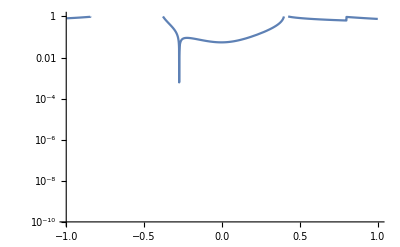

```mathematica
LogPlot[
Abs@ConAxialSymOmegaNMZAmEqnLHSComplex[0.4,kreal,spectC3],
{kreal,-1,1},PlotRange->{Automatic,{10^(-10),1}}
]
```

```mathematica
ParametricPlot[
{
{n ConAxialSymOmegaNMZA[n,spectC3][[1]],ConAxialSymOmegaNMZA[n,spectC3][[1]]},
{n ConAxialSymOmegaNMZA[n,spectC3][[2]],ConAxialSymOmegaNMZA[n,spectC3][[2]]}
},
{n,-50,50},Frame->True,FrameLabel->{"k","ω"},ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},Exclusions->None,PlotLegends->Placed[{"MAA","MZA+","MZA-"},{Left,Top}],PlotLabel->"Dispersion Relation"]
```

-Graphics-

## DR

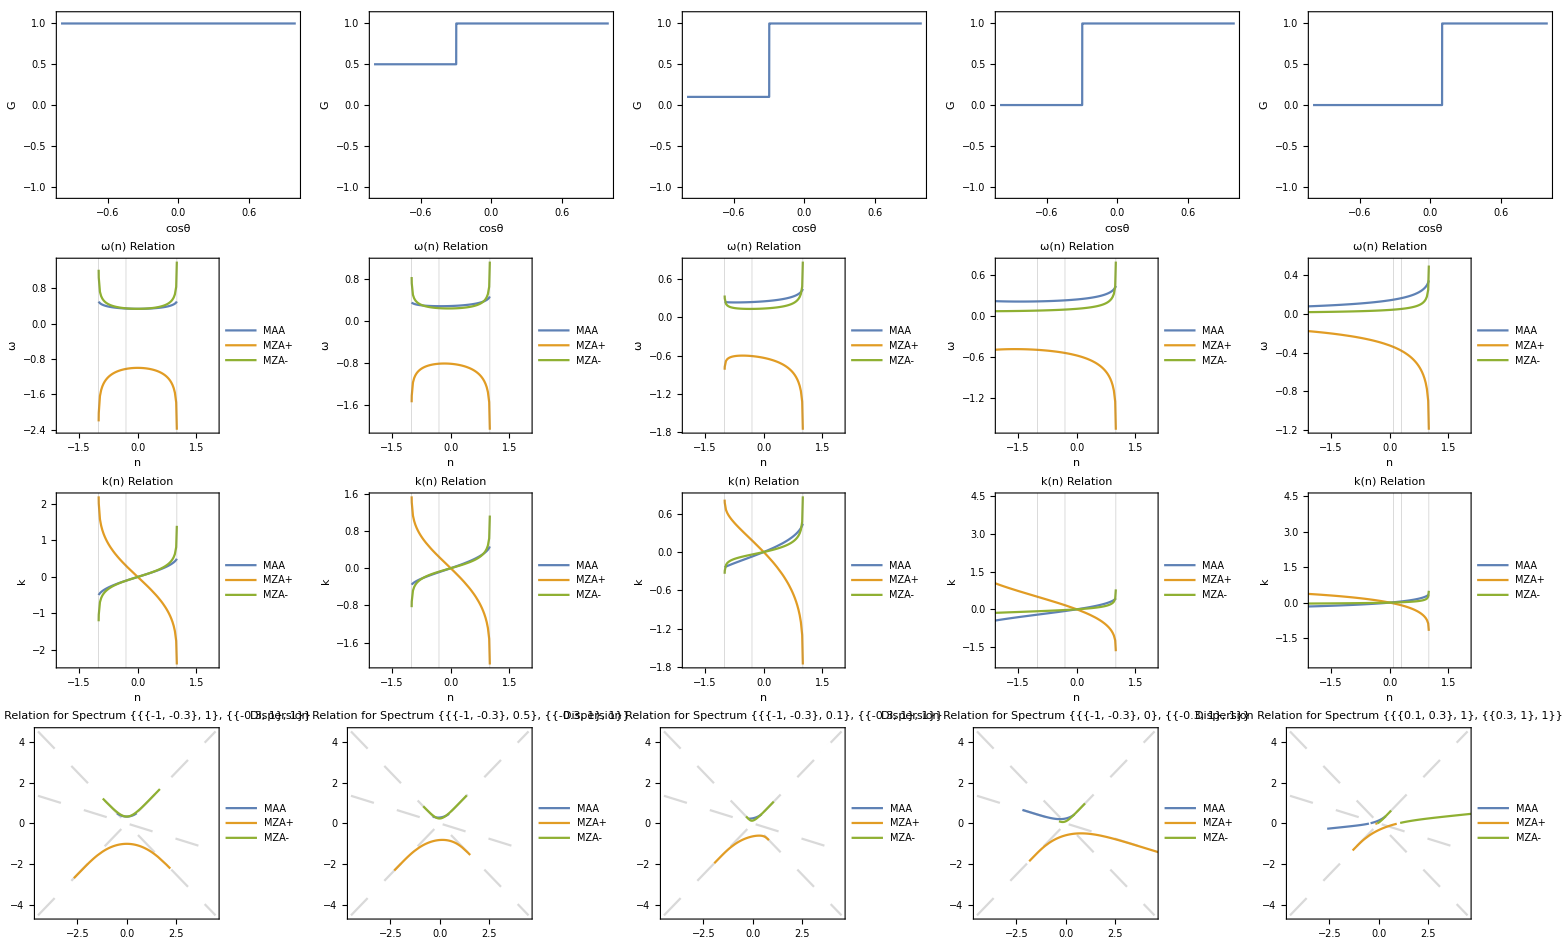

```mathematica
Grid@{
Table[
Plot[
Piecewise[{#[[2]],#[[1,1]]<x<#[[1,2]]}&/@spectra],
{x,-1,1},Frame->True,Axes->True,FrameLabel->{"cosθ","G"},FrameLabel->"Spectrum",ImageSize->Medium,PlotRange->{{-1,1},{-1.1,1.1}}
],
{spectra,{spectWC1,spectWC2,spectWC3,spectWC4,spectWC5}}
],


Table[
Show[
pltOmegaN[spectra],
PlotRange->{{-2,2},Automatic}
],
{spectra,{spectWC1,spectWC2,spectWC3,spectWC4,spectWC5}}
],

Table[
Show[
pltKN[spectra],
PlotRange->{{-2,2},Automatic}
],
{spectra,{spectWC1,spectWC2,spectWC3,spectWC4,spectWC5}}
],

{
pltDRWC1=pltDR[spectWC1],
pltDRWC2=pltDR[spectWC2],
pltDRWC3=pltDR[spectWC3],
pltDRWC4=pltDR[spectWC4],
pltDRWC5=pltDR[spectWC5]
}
}
```

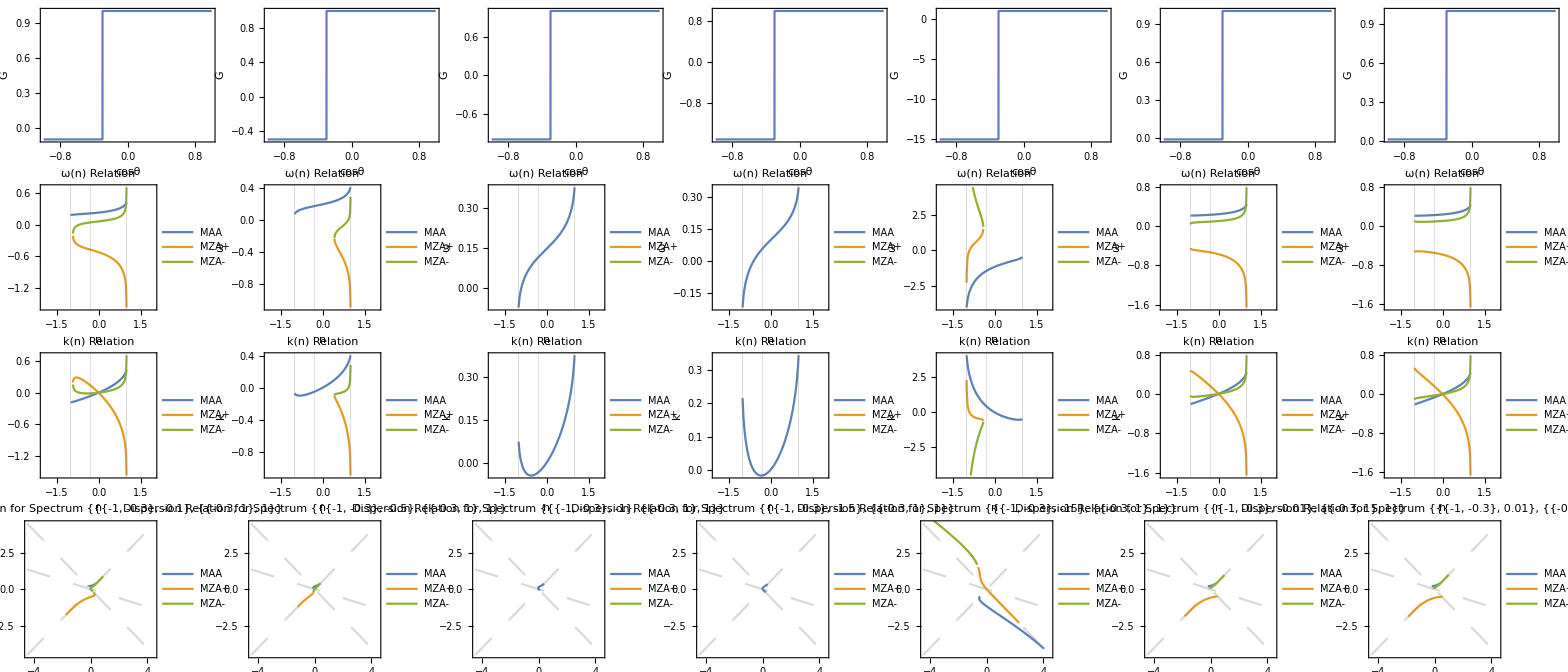

```mathematica
Grid@{

Table[
Plot[
Piecewise[{#[[2]],#[[1,1]]<x<#[[1,2]]}&/@spectra],
{x,-1,1},Frame->True,Axes->True,FrameLabel->{"cosθ","G"},FrameLabel->"Spectrum",ImageSize->Medium,PlotRange->{{-1,1},Full}
],
{spectra,{spectC1,spectC2,spectC3,spectC4,spectC5,spectC6,spectC7}}
],

Table[
Show[
pltOmegaN[spectra],
PlotRange->{{-2,2},Automatic}
],
{spectra,{spectC1,spectC2,spectC3,spectC4,spectC5,spectC6,spectC7}}
],

Table[
Show[
pltKN[spectra],
PlotRange->{{-2,2},Automatic}
],
{spectra,{spectC1,spectC2,spectC3,spectC4,spectC5,spectC6,spectC7}}
],

{
pltDRC1=pltDR[spectC1],
pltDRC2=pltDR[spectC2],
pltDRC3=pltDR[spectC3],
pltDRC4=pltDR[spectC4],
pltDRC5=pltDR[spectC5],
pltDRC6=pltDR[spectC6],
pltDRC7=pltDR[spectC7]
}

}
```

```mathematica
(*Export["export/box-spectrum-crossing/box-spectra-without-crossing-omega-n-k-n-dr.png",Out[377]]*)
```

I observed that MZA solutions dispears for some spectra, spectC3 and spectC4.

```mathematica
FindRoot[
ConAxialSymOmegaNMAA[n,spectC3]==0.1,
{n,0.1}
]
```

{n→-1.}

```mathematica
Select[
Table[
ConAxialSymOmegaNMZA[n,spectC3],
{n,-50,50,0.1}
],
#[[1]]∈Reals&
]
```

{}

```mathematica
Limit[{ConAxialSymOmegaNMAA[n,#],
ConAxialSymOmegaNMZA[n,#]},n->-1]&/@{spectC1,spectC2,spectC3,spectC4,spectC5,spectC6,spectC7}
```

{{-0.182375,{(-ⅈ) ∞,ⅈ ∞}},{-0.066875,{(-ⅈ) ∞,ⅈ ∞}},{0.0775,{(-ⅈ) ∞,ⅈ ∞}},{0.221875,{(-ⅈ) ∞,ⅈ ∞}},{4.12,{-∞,∞}},{-0.208363,{(-ⅈ) ∞,ⅈ ∞}},{-0.214138,{-∞,∞}}}

## Combine with LSA

```mathematica
importData[id_]:=Module[{},

{
{#[[1]],#[[2]],#[[3]]}&/@Import["boxspectrum/export/maalsadata-box-spectrum-"<>ToString[id]<>".csv"],
{#[[1]],Re@ToExpression@#[[2]],Im@ToExpression@#[[2]]}&/@Import["boxspectrum/export/mzaplsadata-box-spectrum-"<>ToString[id]<>".csv"],
 {#[[1]],Re@ToExpression@#[[2]],Im@ToExpression@#[[2]]}&/@Import["boxspectrum/export/mzamlsadata-box-spectrum-"<>ToString[id]<>".csv"]
}

]
```

## Import Data

```mathematica
{
{maalsadataWC1,mzaplsadataWC1,mzamlsadataWC1},
{maalsadataWC2,mzaplsadataWC2,mzamlsadataWC2},
{maalsadataWC3,mzaplsadataWC3,mzamlsadataWC3},
{maalsadataWC4,mzaplsadataWC4,mzamlsadataWC4}
}={
importData["wc1"],
importData["wc2"],
importData["wc3"],
importData["wc4"]
};
```

```mathematica
(* Import data *)

{
{maalsadataC1,mzaplsadataC1,mzamlsadataC1},
{maalsadataC2,mzaplsadataC2,mzamlsadataC2},
{maalsadataC3,mzaplsadataC3,mzamlsadataC3},
{maalsadataC4,mzaplsadataC4,mzamlsadataC4}
}={
importData["c1"],
importData["c2"],
importData["c3"],
importData["c4"]
};
```

```mathematica
maalsadataC1[[2]]
mzaplsadataC1[[2]]
mzamlsadataC1[[2]]
```

{-4.489,-711.195,-9.9825×10^-22}

{-4.489,-4.489,-4.41493×10^-9}

{-4.489,-118.753,84.4458}

Alternatively I could calculate the mza solutions on spot.
mzap:
cw1:  0.1,0.72
cw2: 0.1,0.62
cw3: 0.01,3.4
cw4:

```mathematica
spectWC1
```

{{{-1,-0.3},1},{{-0.3,1},1}}

```mathematica
ConAxialSymOmegaNMAAEqnLHSComplex[0.001,0.1+0.1I,spectWC1]
ConAxialSymOmegaNMAAEqnLHSComplexN[0.001,0.1+0.1I,spectWC1]
```

-0.0029268-0.00387719 ⅈ

-0.0029268-0.00387719 ⅈ

```mathematica
Plot3D[
{Re@ConAxialSymOmegaNMZApEqnLHSComplex[omegareal+I*omegaimag,0.1,spectWC1],Im@ConAxialSymOmegaNMZApEqnLHSComplex[omegareal+I*omegaimag,0.1,spectWC1],0},
{omegareal,-1,1},{omegaimag,-1,1},PlotRange->{Automatic,Automatic,{-1,2}},AxesLabel->{"Re@omega","Im@omega",""},ImageSize->Large,PlotLabel->"MZA+ Solution for WC1 Spectrum"
]
```

```mathematica
Plot3D[
{Re@ConAxialSymOmegaNMAAEqnLHSComplex[0.1,kreal+I*kimag,spectWC1],Im@ConAxialSymOmegaNMAAEqnLHSComplex[0.1,kreal+I*kimag,spectWC1],0},
{kreal,-10,10},{kimag,-10,10},PlotRange->{Automatic,Automatic,{-0.1,0.1}},AxesLabel->{"Re@k","Im@k",""},ImageSize->Large,PlotLabel->"MAA Solution for WC1 Spectrum"
]
```

```mathematica
maalsadataWC1={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMAAEqnLHSComplex[omegareal,k,spectWC1],{k,0.1 I}]},{omegareal,-1.4,-0.1,0.01}];
```

```mathematica
mzaplsadataWC1={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMZApEqnLHSComplex[omegareal,k,spectWC1],{k,0.1 I},MaxIterations->10000]},{omegareal,-1.4,-0.1,0.01}];
mzamlsadataWC1={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMZAmEqnLHSComplex[omegareal,k,spectWC1],{k,0.1 I},MaxIterations->10000]},{omegareal,0.01,3.4,0.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
mzaplsadataWC2={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMZApEqnLHSComplex[omegareal,k,spectWC2],{k,0.1 I},MaxIterations->10000]},{omegareal,-1.4,-0.1,0.01}];
mzamlsadataWC2={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMZAmEqnLHSComplex[omegareal,k,spectWC2],{k,0.1 I},MaxIterations->10000]},{omegareal,0.01,3.4,0.01}];
```

```mathematica
mzaplsadataWC3={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMZApEqnLHSComplex[omegareal,k,spectWC3],{k,0.1 I},MaxIterations->10000]},{omegareal,-2.78,-0.11,0.01}];
mzamlsadataWC3={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMZAmEqnLHSComplex[omegareal,k,spectWC3],{k,0.1 I},MaxIterations->10000]},{omegareal,0.01,3.4,0.01}];
```

```mathematica
mzaplsadataWC4={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMZApEqnLHSComplex[omegareal,k,spectC4],{k,0.1 I},MaxIterations->10000]},{omegareal,-1.4,-0.1,0.01}];
mzamlsadataWC4={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMZAmEqnLHSComplex[omegareal,k,spectC4],{k,0.1 I},MaxIterations->10000]},{omegareal,0.01,3.4,0.01}];
```

```mathematica
mzaplsadataC1={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMZApEqnLHSComplex[omegareal,k,spectC1],{k,0.1 I},MaxIterations->10000]},{omegareal,-2.8,-0.01,0.01}];
mzamlsadataC1={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMZAmEqnLHSComplex[omegareal,k,spectC1],{k,0.1 I},MaxIterations->10000]},{omegareal,0.01,3.3,0.01}];
```

$Aborted

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
mzaplsadataC2={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMZApEqnLHSComplex[omegareal,k,spectC2],{k,0.1 I},MaxIterations->10000]},{omegareal,-2.8,-0.01,0.01}];
mzamlsadataC2={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMZAmEqnLHSComplex[omegareal,k,spectC2],{k,0.1 I},MaxIterations->10000]},{omegareal,0.01,3.3,0.01}];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

```mathematica
mzaplsadataC3={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMZApEqnLHSComplex[omegareal,k,spectC3],{k,0.1 I},MaxIterations->10000]},{omegareal,-2.8,-0.01,0.01}];
mzamlsadataC3={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMZAmEqnLHSComplex[omegareal,k,spectC3],{k,0.1 I},MaxIterations->10000]},{omegareal,0.01,3.3,0.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
mzaplsadataC4={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMZApEqnLHSComplex[omegareal,k,spectC4],{k,0.1 I},MaxIterations->10000]},{omegareal,-2.8,-0.01,0.01}];
mzamlsadataC4={#[[1]],Re@#[[2]],Abs@Im@#[[2]]}&/@Table[{omegareal,k/.FindRoot[ConAxialSymOmegaNMZAmEqnLHSComplex[omegareal,k,spectC4],{k,0.1 I},MaxIterations->10000]},{omegareal,0.01,3.3,0.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

Clean up the data.

```mathematica
imaglow=10^(-5);
valepsilon=0.1;
```

```mathematica
maalsadataWC1Clean=Select[Flatten@#&/@maalsadataWC1,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMAAEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC1]<valepsilon)&];
mzaplsadataWC1Clean=Select[Flatten@#&/@mzaplsadataWC1,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC1]<valepsilon)&];
mzamlsadataWC1Clean=Select[Flatten@#&/@mzamlsadataWC1,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC1]<valepsilon)&];

maalsadataWC2Clean=Select[Flatten@#&/@maalsadataWC2,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMAAEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC2]<valepsilon)&];
mzaplsadataWC2Clean=Select[Flatten@#&/@mzaplsadataWC2,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC2]<valepsilon)&];
mzamlsadataWC2Clean=Select[Flatten@#&/@mzamlsadataWC2,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC2]<valepsilon)&];


maalsadataWC3Clean=Select[Flatten@#&/@maalsadataWC3,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMAAEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC3]<valepsilon)&];
mzaplsadataWC3Clean=Select[Flatten@#&/@mzaplsadataWC3,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC3]<valepsilon)&];
mzamlsadataWC3Clean=Select[Flatten@#&/@mzamlsadataWC3,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC3]<valepsilon)&];


maalsadataWC4Clean=Select[Flatten@#&/@maalsadataWC4,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMAAEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC4]<valepsilon)&];
mzaplsadataWC4Clean=Select[Flatten@#&/@mzaplsadataWC4,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC4]<valepsilon)&];
mzamlsadataWC4Clean=Select[Flatten@#&/@mzamlsadataWC4,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC4]<valepsilon)&];


(* **************** *)


maalsadataC1Clean=Select[Flatten@#&/@maalsadataC1,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMAAEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC1]<valepsilon)&];
mzaplsadataC1Clean=Select[Flatten@#&/@mzaplsadataC1,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC1]<valepsilon)&];
mzamlsadataC1Clean=Select[Flatten@#&/@mzamlsadataC1,(-4.5<#[[1]]<4.5)&&(-0.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC1]<valepsilon)&];


maalsadataC2Clean=Select[Flatten@#&/@maalsadataC2,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMAAEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC2]<valepsilon)&];
mzaplsadataC2Clean=Select[Flatten@#&/@mzaplsadataC2,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC2]<valepsilon)&];
mzamlsadataC2Clean=Select[Flatten@#&/@mzamlsadataC2,(-4.5<#[[1]]<4.5)&&(-0.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC2]<valepsilon)&];


maalsadataC3Clean=Select[Flatten@#&/@maalsadataC3,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMAAEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC3]<valepsilon)&];
mzaplsadataC3Clean=Select[Flatten@#&/@mzaplsadataC3,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC3]<valepsilon)&];
mzamlsadataC3Clean=Select[Flatten@#&/@mzamlsadataC3,(-4.5<#[[1]]<4.5)&&(-0.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC3]<valepsilon)&];


maalsadataC4Clean=Select[Flatten@#&/@maalsadataC4,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMAAEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC4]<valepsilon)&];
mzaplsadataC4Clean=Select[Flatten@#&/@mzaplsadataC4,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC4]<valepsilon)&];
mzamlsadataC4Clean=Select[Flatten@#&/@mzamlsadataC4,(-4.5<#[[1]]<4.5)&&(-0.5<#[[2]]<4.5)&&(imaglow<Abs@#[[3]]<500)&&(Abs@ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC4]<valepsilon)&];
```

### Validate Data

#### Some Numerical Demonstrations

```mathematica
Chop[
ConAxialSymOmegaNMAAEqnLHS[#[[1]],0,#[[2]],#[[3]],spectWC1,2*$MachinePrecision]&/@maalsadataWC1Clean,
10^(-10)
]//Quiet
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0.754876,0.0803537},{0.774415,0.10274},{0.875644,-0.0804188},{1.59539,-0.0891957},{1.6569,-0.0840978},{3.3249,0.0943658},{3.4424,-0.0945426}}

```mathematica
Chop[
ConAxialSymOmegaNMAAEqnLHS[#[[1]],0,#[[2]],#[[3]],spectWC2,2*$MachinePrecision]&/@maalsadataWC2Clean,
10^(-10)
]//Quiet
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0.714666,-0.0842437},{1.04444,-0.0925068},{1.07815,0.116067},{1.09544,-0.111946},{1.12594,-0.0836909},{1.20556,-0.112569},{1.38464,0.0861224},{1.71549,0.0866702},{2.18514,-0.0985023},{2.31601,-0.0898015},{2.36533,-0.100399},{2.82856,0.0450954},{2.84542,-0.0977076},{2.96473,-0.0949667},{3.19408,0.0907287},{3.32515,0.108982},{3.66411,0.0433251},{3.76664,-0.0429438},{3.6749,0.0948431}}

```mathematica
Chop[
ConAxialSymOmegaNMAAEqnLHS[#[[1]],0,#[[2]],#[[3]],spectC1,2*$MachinePrecision]&/@maalsadataC1Clean,
10^(-10)
]//Quiet
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0.203068,-0.0632274},{0.27356,0.0617496},{0.352434,-0.0697426},{0.901585,0.0828033},{0.951417,-0.0901929},{0.940202,0.113495},{1.03164,0.0866023},{1.61061,-0.0903602},{1.91074,0.0932448},{2.18296,-0.0637107},{2.36159,-0.106924},{3.21739,0.0446274},{3.12073,-0.0982759},{3.14015,-0.111225}}

```mathematica
Chop[
ConAxialSymOmegaNMAAEqnLHS[#[[1]],0,#[[2]],#[[3]],spectC2,2*$MachinePrecision]&/@maalsadataC2Clean,
10^(-10)
]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
Chop[
ConAxialSymOmegaNMAAEqnLHS[#[[1]],0,#[[2]],#[[3]],spectC3,2*$MachinePrecision]&/@maalsadataC3Clean,
10^(-10)
]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

Validate MZA solutions

```mathematica
Chop[
ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[3]]*I,spectWC1]&/@mzaplsadataWC1Clean,
10^(-10)
]
```

{-1.53813-0.389916 ⅈ,-1.5564-0.323432 ⅈ,0.000432253+0.000361618 ⅈ,0.00544972+0.0035508 ⅈ,0.00849997+0.00804769 ⅈ,0.012527+0.0119602 ⅈ,0.0167061+0.0158178 ⅈ,0.0116752+0.0260013 ⅈ,-0.00954554+0.0483717 ⅈ,-0.0200694+0.064204 ⅈ}

```mathematica
Chop[
ConAxialSymOmegaNMZApEqnLHS[#[[1]],0,#[[2]],#[[3]],spectWC1]&/@mzaplsadataWC1Clean,
10^(-10)
]
```

{{-1.53813,-0.389916},{-1.5564,-0.323432},{0.000432253,0.000361618},{0.00544972,0.0035508},{0.00849997,0.00804769},{0.012527,0.0119602},{0.0167061,0.0158178},{0.0116752,0.0260013},{-0.00954554,0.0483717},{-0.0200694,0.064204}}

```mathematica
k/.FindRoot[ConAxialSymOmegaNMZApEqnLHSComplex[-1.5,k,spectWC1],{k,0.1 ⅈ},MaxIterations->10000]
```

$Aborted

```mathematica
ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[3]] ⅈ,spectWC1]&/@mzaplsadataWC1Clean
```

Testing range of omega for WC spect

```mathematica
k/.FindRoot[ConAxialSymOmegaNMZApEqnLHSComplex[-1.4,k,spectWC2],{k,0.1 ⅈ},MaxIterations->10000]
k/.FindRoot[ConAxialSymOmegaNMZApEqnLHSComplex[-0.1,k,spectWC2],{k,0.1 ⅈ},MaxIterations->10000]

k/.FindRoot[ConAxialSymOmegaNMZAmEqnLHSComplex[0.01,k,spectWC4],{k,0.1 ⅈ},MaxIterations->10000]
k/.FindRoot[ConAxialSymOmegaNMZAmEqnLHSComplex[3.4,k,spectWC4],{k,0.1 ⅈ},MaxIterations->10000]
```

-1.39889-6.70825×10^-18 ⅈ

-0.0235697-1.37045×10^-20 ⅈ

-0.590078+1.57836 ⅈ

3.4+1.13676×10^-15 ⅈ

Testing range of omega for C spect

```mathematica
k/.FindRoot[ConAxialSymOmegaNMZApEqnLHSComplex[-2.8,k,spectC1],{k,0.1 ⅈ},MaxIterations->10000]
k/.FindRoot[ConAxialSymOmegaNMZApEqnLHSComplex[-0.1,k,spectC1],{k,0.1 ⅈ},MaxIterations->10000]

k/.FindRoot[ConAxialSymOmegaNMZAmEqnLHSComplex[0.01,k,spectC2],{k,0.1 ⅈ},MaxIterations->10000]
k/.FindRoot[ConAxialSymOmegaNMZAmEqnLHSComplex[3.3,k,spectC2],{k,0.1 ⅈ},MaxIterations->10000]
```

-2.8-2.17779×10^-15 ⅈ

0.125393+0.0831625 ⅈ

-0.874022+1.59949 ⅈ

3.3-3.02016×10^-15 ⅈ

```mathematica
ConAxialSymOmegaNMZApEqnLHSComplex[0.6,-0.3638096227257392+7.972197178222856*^-18 ⅈ,spectWC1]
```

3.33067×10^-15+3.36546×10^-17 ⅈ

```mathematica
Grid@{
Table[

Plot3D[
{ConAxialSymOmegaNMZApEqnLHS[omegareal,0,kreal,kimag,spectWC1][[1]],ConAxialSymOmegaNMZApEqnLHS[omegareal,0,kreal,kimag,spectWC1][[2]],0},
{kreal,-5,5},{kimag,-5,5},AxesLabel->{"kreal","kimag","omega"},ImageSize->Large,PlotLegends->{"Real Part", "Imaginary Part","0"},PlotLabel->ToString[omegareal]
],
{omegareal,{-4,-0.8,-0.4,-0.2,0.2,0.4,0.8,4}}
]
}
```

#### Formal Validation of Clean Data

```mathematica
Abs@ConAxialSymOmegaNMAAEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC2]&/@maalsadataWC2Clean
```

{0.00516508,0.0504528,0.0846924,0.108662,0.124057,0.133336,0.138546,0.140932,0.141207,0.139815,0.137069,0.133209,0.128427,0.122877,0.116686,0.109958,0.102778,0.0952133,0.0873233,0.0791564,0.0707544,0.0621536,0.0533855,0.0444773,0.0354523,0.0263298,0.017126,0.00785399,0.00147569,0.981839,1.31155,1.3535,1.36353,1.39044,1.47327,1.65019,1.97979,2.45058,2.57959,2.63066,2.82149,3.11011,3.22977,3.45924,3.59112,3.63113,3.73109,3.93951}

spect WC

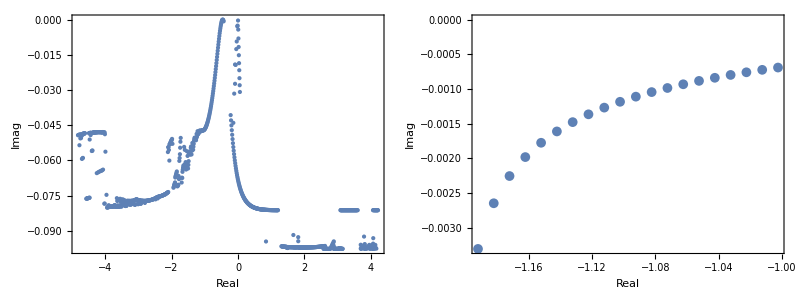

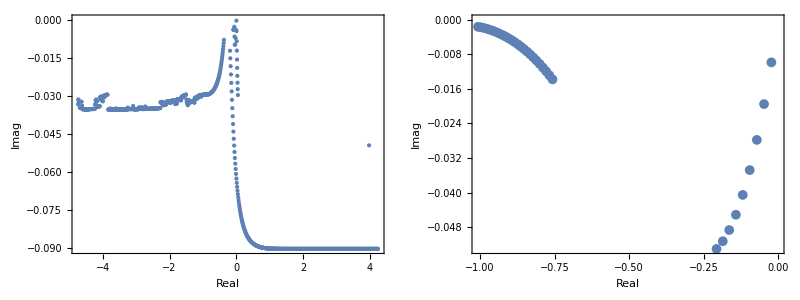

```mathematica
Grid@{{
ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMAAEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC1]&/@mzamlsadataWC1),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
],
ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMAAEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC1]&/@mzaplsadataWC1Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
]
}}

Grid@{{
ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMAAEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC2]&/@mzamlsadataWC2),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
],
ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMAAEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC2]&/@mzaplsadataWC2Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
]
}}
```

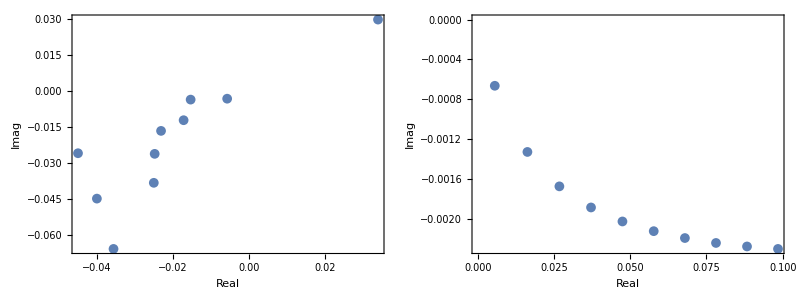

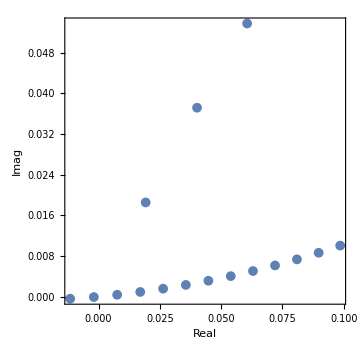
-Graphics- | -Graphics-

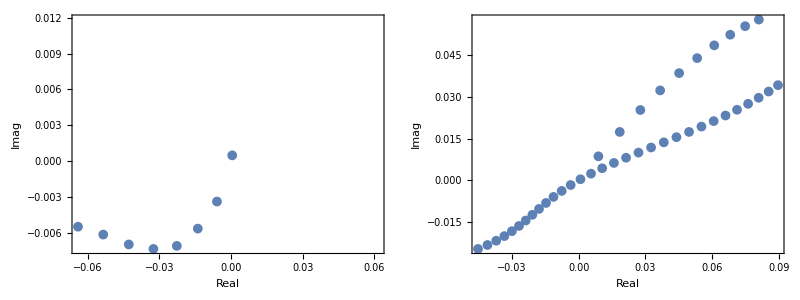

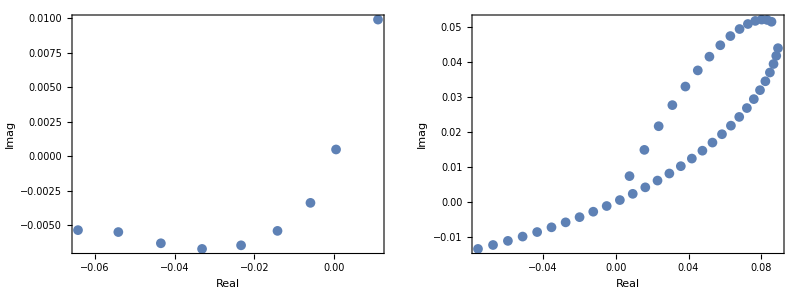

```mathematica
Grid@{{
ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC1]&/@mzamlsadataWC1Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
],
ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC1]&/@mzaplsadataWC1Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
]
}}

Grid@{{
ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC2,2*$MachinePrecision]&/@mzamlsadataWC2Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
],

ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC2]&/@mzaplsadataWC2Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
]
}}


Grid@{{
ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC3]&/@mzamlsadataWC3Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
],

ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC3]&/@mzaplsadataWC3Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
]
}}

Grid@{{
ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC4]&/@mzamlsadataWC4Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
],

ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectWC4]&/@mzaplsadataWC4Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
]
}}
```

spect C

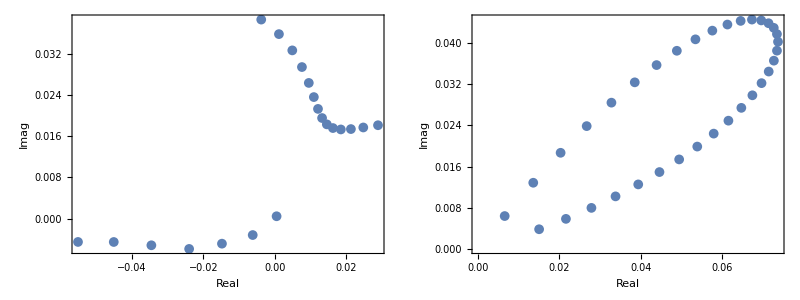

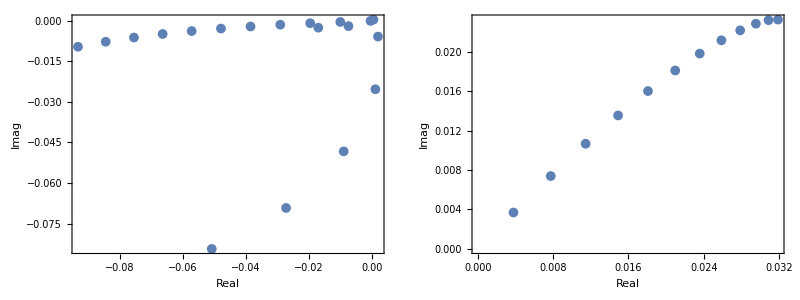

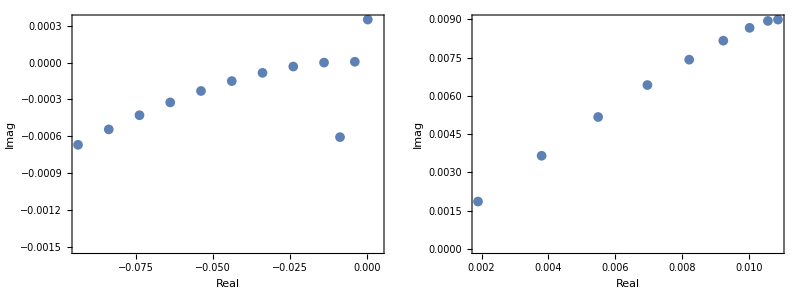

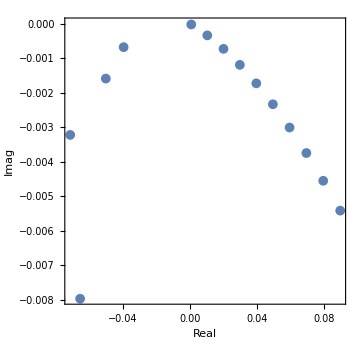
-Graphics- | -Graphics-

```mathematica
Grid@{{
ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC1]&/@mzamlsadataC1Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
],
ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC1]&/@mzaplsadataC1Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
]
}}

Grid@{{
ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC2]&/@mzamlsadataC2Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
],

ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC2]&/@mzaplsadataC2Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
]
}}


Grid@{{
ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC3]&/@mzamlsadataC3Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
],

ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC3]&/@mzaplsadataC3Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
]
}}

Grid@{{
ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMZAmEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC4]&/@mzamlsadataC4Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
],

ListPlot[
{Re@#,Im@#}&/@(ConAxialSymOmegaNMZApEqnLHSComplex[#[[1]],#[[2]]+#[[2]]I,spectC4]&/@mzaplsadataC4Clean),
Frame->True,AspectRatio->1,FrameLabel->{"Real","Imag"},ImageSize->Medium
]
}}
```

## Making Plots

### Tests

```mathematica
{#[[1]],Re[(#[[1]]/#[[2]]+I#[[3]])]}&/@maalsadataWC2Clean
maalsadataWC2Clean
```

{{0.001,-0.0106608},{0.011,-0.115064},{0.021,-0.21565},{0.171,-1.58091},{0.181,-1.69809},{0.191,-1.82554},{0.201,-1.96499},{0.211,-2.11828},{0.221,-2.28745},{0.231,-2.47471},{0.241,-2.68256},{0.251,-2.91393},{0.261,-3.17227},{0.271,-3.4618},{0.281,-3.78778}}

```mathematica
N@Pi/4
```

0.785398

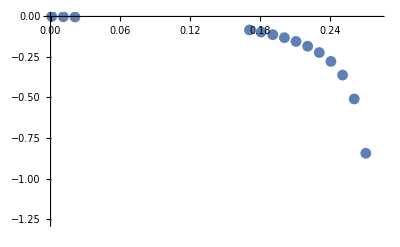

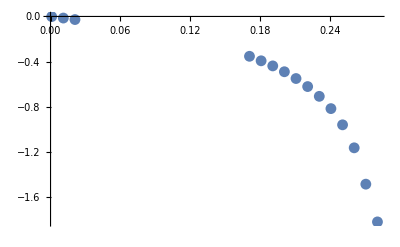

```mathematica
ListPlot[
{#[[1]],Re[(#[[1]]/(#[[2]]+I#[[3]]) )]}&/@maalsadataWC2Clean
]

ListPlot[
{#[[1]],Im[(#[[1]]/(#[[2]]+I#[[3]]) )]}&/@maalsadataWC2Clean
]
```

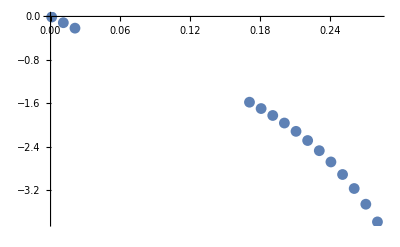

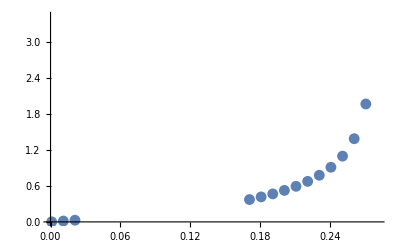

```mathematica
ListPlot[
{#[[1]],(#[[1]]/Re[(#[[2]]+I#[[3]]) ])}&/@maalsadataWC2Clean
]
ListPlot[
{#[[1]],(#[[1]]/Im[(#[[2]]+I#[[3]]) ])}&/@maalsadataWC2Clean
]
```

### Plots

```mathematica
Grid@{{
pltDROmegaRealLSA[maalsadataWC1Clean,pltDRWC1],
pltDROmegaRealLSA[maalsadataWC2Clean,pltDRWC2],
pltDROmegaRealLSA[maalsadataWC3Clean,pltDRWC3],
pltDROmegaRealLSA[maalsadataWC4Clean,pltDRWC4]
}}
```

-Graphics-

```mathematica
Grid@{{
pltDROmegaRealLSA[maalsadataC1Clean,pltDRC1],
pltDROmegaRealLSA[maalsadataC2Clean,pltDRC2],
pltDROmegaRealLSA[maalsadataC3Clean,pltDRC3],
pltDROmegaRealLSA[maalsadataC4Clean,pltDRC4]
}}
```

-Graphics-

```mathematica
Grid@{{
pltDROmegaRealLSA[mzaplsadataWC1Clean,pltDRWC1],
pltDROmegaRealLSA[mzaplsadataWC2Clean,pltDRWC2],
pltDROmegaRealLSA[mzaplsadataWC3Clean,pltDRWC3],
pltDROmegaRealLSA[mzaplsadataWC4Clean,pltDRWC4]
}}


Grid@{{
pltDROmegaRealLSA[mzamlsadataWC1Clean,pltDRWC1],
pltDROmegaRealLSA[mzamlsadataWC2Clean,pltDRWC2],
pltDROmegaRealLSA[mzamlsadataWC3Clean,pltDRWC3],
pltDROmegaRealLSA[mzamlsadataWC4Clean,pltDRWC4]
}}
```

-Graphics-

-Graphics-

```mathematica
Grid@{{
pltDROmegaRealLSA[mzaplsadataC1Clean,pltDRC1],
pltDROmegaRealLSA[mzaplsadataC2Clean,pltDRC2],
pltDROmegaRealLSA[mzaplsadataC3Clean,pltDRC3],
pltDROmegaRealLSA[mzaplsadataC4Clean,pltDRC4]
}}
Grid@{{
pltDROmegaRealLSA[mzamlsadataC1Clean,pltDRC1],
pltDROmegaRealLSA[mzamlsadataC2Clean,pltDRC2],
pltDROmegaRealLSA[mzamlsadataC3Clean,pltDRC3],
pltDROmegaRealLSA[mzamlsadataC4Clean,pltDRC4]
}}
```

-Graphics-

-Graphics-

Real K

## Import Data

```mathematica
importRealKData[id_]:=Module[{},

{
{#[[1]],#[[3]],#[[2]]}&/@Import["boxspectrum/export/maarealklsadata-box-spectrum-"<>ToString[id]<>".csv"],
{Re@ToExpression@#[[1]],#[[2]],Im@ToExpression@#[[1]]}&/@Import["boxspectrum/export/mzaprealklsadata-box-spectrum-"<>ToString[id]<>".csv"],
 {Re@ToExpression@#[[1]],#[[2]],Im@ToExpression@#[[1]]}&/@Import["boxspectrum/export/mzamrealklsadata-box-spectrum-"<>ToString[id]<>".csv"]
}

]
```

```mathematica
{
{maarealklsadataWC1,mzaprealklsadataWC1,mzamrealklsadataWC1},
{maarealklsadataWC2,mzaprealklsadataWC2,mzamrealklsadataWC2},
{maarealklsadataWC3,mzaprealklsadataWC3,mzamrealklsadataWC3},
{maarealklsadataWC4,mzaprealklsadataWC4,mzamrealklsadataWC4}
}={
importRealKData["wc1"],
importRealKData["wc2"],
importRealKData["wc3"],
importRealKData["wc4"]
};


{
{maarealklsadataC1,mzaprealklsadataC1,mzamrealklsadataC1},
{maarealklsadataC2,mzaprealklsadataC2,mzamrealklsadataC2},
{maarealklsadataC3,mzaprealklsadataC3,mzamrealklsadataC3},
{maarealklsadataC4,mzaprealklsadataC4,mzamrealklsadataC4}
}={
importRealKData["c1"],
importRealKData["c2"],
importRealKData["c3"],
importRealKData["c4"]
};
```

```mathematica
maarealklsadataWC1Clean=Select[Flatten@#&/@maarealklsadataWC1,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
mzaprealklsadataWC1Clean=Select[Flatten@#&/@mzaprealklsadataWC1,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
mzamrealklsadataWC1Clean=Select[Flatten@#&/@mzamrealklsadataWC1,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];


maarealklsadataWC2Clean=Select[Flatten@#&/@maarealklsadataWC2,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
mzaprealklsadataWC2Clean=Select[Flatten@#&/@mzaprealklsadataWC2,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
mzamrealklsadataWC2Clean=Select[Flatten@#&/@mzamrealklsadataWC2,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];


maarealklsadataWC3Clean=Select[Flatten@#&/@maarealklsadataWC3,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
mzaprealklsadataWC3Clean=Select[Flatten@#&/@mzaprealklsadataWC3,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
mzamrealklsadataWC3Clean=Select[Flatten@#&/@mzamrealklsadataWC3,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];


maarealklsadataWC4Clean=Select[Flatten@#&/@maarealklsadataWC4,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
mzaprealklsadataWC4Clean=Select[Flatten@#&/@mzaprealklsadataWC4,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
mzamrealklsadataWC4Clean=Select[Flatten@#&/@mzamrealklsadataWC4,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];


(* **************** *)


maarealklsadataC1Clean=Select[Flatten@#&/@maarealklsadataC1,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
mzaprealklsadataC1Clean=Select[Flatten@#&/@mzaprealklsadataC1,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
mzamrealklsadataC1Clean=Select[Flatten@#&/@mzamrealklsadataC1,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];


maarealklsadataC2Clean=Select[Flatten@#&/@maarealklsadataC2,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
mzaprealklsadataC2Clean=Select[Flatten@#&/@mzaprealklsadataC2,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
mzamrealklsadataC2Clean=Select[Flatten@#&/@mzamrealklsadataC2,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];


maarealklsadataC3Clean=Select[Flatten@#&/@maarealklsadataC3,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
mzaprealklsadataC3Clean=Select[Flatten@#&/@mzaprealklsadataC3,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
mzamrealklsadataC3Clean=Select[Flatten@#&/@mzamrealklsadataC3,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];


maarealklsadataC4Clean=Select[Flatten@#&/@maarealklsadataC4,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
mzaprealklsadataC4Clean=Select[Flatten@#&/@mzaprealklsadataC4,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
mzamrealklsadataC4Clean=Select[Flatten@#&/@mzamrealklsadataC4,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(10^(-2)<#[[3]]<500)&];
```

### Validate Data

```mathematica
ConAxialSymOmegaNMZApEqnLHS[-4.4,0,kreal,kimag,spectWC1]
```

```mathematica
Table[

Plot3D[
{ConAxialSymOmegaNMAAEqnLHS[omegareal,omegaimag,kreal,0,spectWC1][[1]],ConAxialSymOmegaNMAAEqnLHS[omegareal,omegaimag,kreal,0,spectWC1][[2]],0},
{omegareal,-5,5},{omegaimag,-5,5},AxesLabel->{"omegareal","omegaimag","MAA"},ImageSize->Large,PlotLegends->{"Real Part", "Imaginary Part","0"},PlotLabel->ToString[kreal]
],
{kreal,{-0.2}}
]
```

```mathematica
Grid@{
Table[

Plot3D[
{ConAxialSymOmegaNMAAEqnLHS[omegareal,omegaimag,kreal,0,spectWC1][[1]],ConAxialSymOmegaNMAAEqnLHS[omegareal,omegaimag,kreal,0,spectWC1][[2]],0},
{omegareal,-10,10},{omegaimag,-10,10},AxesLabel->{"omegareal","omegaimag","MAA"},ImageSize->Large,PlotLegends->{"Real Part", "Imaginary Part","0"},PlotLabel->ToString[kreal]
],
{kreal,{-4,-0.8,-0.4,-0.2,0.2,0.4,0.8,4}}
]
}
```

$Aborted

```mathematica
Table[

Plot3D[
{ConAxialSymOmegaNMZApEqnLHS[omegareal,omegaimag,kreal,0,spectWC1][[1]],ConAxialSymOmegaNMZApEqnLHS[omegareal,omegaimag,kreal,0,spectWC1][[2]],0},
{omegareal,-10,10},{omegaimag,-10,10},AxesLabel->{"omegareal","omegaimag","MZA+"},ImageSize->Large,PlotLegends->{"Real Part", "Imaginary Part","0"},PlotLabel->ToString[kreal]
],
{kreal,{-4,-0.8,-0.4,-0.2,0.2,0.4,0.8,4}}
]
```

## Make Plots

```mathematica
Grid@{{
pltDROmegaRealLSA[maarealklsadataWC1Clean,pltDRWC1],
pltDROmegaRealLSA[maarealklsadataWC2Clean,pltDRWC2],
pltDROmegaRealLSA[maarealklsadataWC3Clean,pltDRWC3],
pltDROmegaRealLSA[maarealklsadataWC4Clean,pltDRWC4]
}}
```

-Graphics-

```mathematica
Grid@{{
pltDROmegaRealLSA[maarealklsadataC1Clean,pltDRC1],
pltDROmegaRealLSA[maarealklsadataC2Clean,pltDRC2],
pltDROmegaRealLSA[maarealklsadataC3Clean,pltDRC3],
pltDROmegaRealLSA[maarealklsadataC4Clean,pltDRC4]
}}
```

-Graphics-

```mathematica
Grid@{{
pltDROmegaRealLSA[mzaprealklsadataWC1Clean,pltDRWC1],
pltDROmegaRealLSA[mzaprealklsadataWC2Clean,pltDRWC2],
pltDROmegaRealLSA[mzaprealklsadataWC3Clean,pltDRWC3],
pltDROmegaRealLSA[mzaprealklsadataWC4Clean,pltDRWC4]
}}

Grid@{{
pltDROmegaRealLSA[mzamrealklsadataWC1Clean,pltDRWC1],
pltDROmegaRealLSA[mzamrealklsadataWC2Clean,pltDRWC2],
pltDROmegaRealLSA[mzamrealklsadataWC3Clean,pltDRWC3],
pltDROmegaRealLSA[mzamrealklsadataWC4Clean,pltDRWC4]
}}
```

-Graphics-

-Graphics-

```mathematica
Grid@{{
pltDROmegaRealLSA[mzaprealklsadataC1Clean,pltDRC1],
pltDROmegaRealLSA[mzaprealklsadataC2Clean,pltDRC2],
pltDROmegaRealLSA[mzaprealklsadataC3Clean,pltDRC3],
pltDROmegaRealLSA[mzaprealklsadataC4Clean,pltDRC4]
}}

Grid@{{
pltDROmegaRealLSA[mzamrealklsadataC1Clean,pltDRC1],
pltDROmegaRealLSA[mzamrealklsadataC2Clean,pltDRC2],
pltDROmegaRealLSA[mzamrealklsadataC3Clean,pltDRC3],
pltDROmegaRealLSA[mzamrealklsadataC4Clean,pltDRC4]
}}
```

-Graphics-

-Graphics-

## Test of Package for Numerical Finding Instabilities

```mathematica
ConAxialSymOmegaNMAAEqnLHS[0.1,0,0.5,0.2,spectWC1]
```

{0.0254547,-0.109937}

```mathematica
Table[{omegareal,{kreal,kimag}/.FindRoot[ConAxialSymOmegaNMAAEqnLHS[omegareal,0,kreal,kimag,spectrum],{kreal,0.1},{kimag,0.1}]},{omegareal,-4.499,4.499,0.01}]
```

```mathematica
FindRoot[ConAxialSymOmegaNMAAEqnLHS[0.1,0,kreal,kimag,spectC1],{kreal,0.1},{kimag,0.1}]
```

{kreal→-0.260755,kimag→0.577222}

```mathematica
FindRoot[ConAxialSymOmegaNMAAEqnLHSComplex[0.1,k,spectC1],{k,0.1I}]
```

{k→-0.260755+0.577222 ⅈ}

```mathematica
FindRoot[ConAxialSymOmegaNMZApEqnLHS[0.1,0,kreal,kimag,spectC1],{kreal,0.2},{kimag,0.1},WorkingPrecision->30]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

{kreal→1.08621119170425210645359951224,kimag→1.48472422640315184715534388509}

```mathematica
ConAxialSymOmegaNMZApEqnLHS[0.1,0,kreal,kimag,spectC1]/.{kreal->1.086211191704252106453599512236771382566258167350492010693`30.,kimag->1.4847242264031518471553438850902859706934898285627672332812`30.}
```

{0.0869051,0.0269258}

```mathematica
FindRoot[ConAxialSymOmegaNMZApEqnLHSComplex[0.1,k,spectC1],{k,0.1I},WorkingPrecision->30]
ConAxialSymOmegaNMZApEqnLHSComplex[0.1,k,spectC1]/.%
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

{k→2.66055498514849210247428068763-1.89277306065393431713700115332 ⅈ}

0.0868705-0.0121687 ⅈ

```mathematica
FindRoot[ConAxialSymOmegaNMZAmEqnLHS[0.1,0,kreal,kimag,spectC1],{kreal,0.15},{kimag,0.1},WorkingPrecision->30]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

{kreal→1.83112929291996300101591894179,kimag→1.25608653868746062672579197135}

```mathematica
ConAxialSymOmegaNMZAmEqnLHS[0.1,0,kreal,kimag,spectC1]/.{kreal->2.9867412623830492356866189117060586861760634816868689534344`30.,kimag->12.8208987161618102320745424135342991778141820358315274836674`30.}
```

{0.0992259,0.00437811}

```mathematica
FindRoot[ConAxialSymOmegaNMZAmEqnLHSComplex[0.1,k,spectC1],{k,0.1I}]
ConAxialSymOmegaNMZAmEqnLHSComplex[0.1,k,spectC1]/.%
```

{k→-0.690552+1.45273 ⅈ}

-1.38778×10^-17-8.67362×10^-18 ⅈ

```mathematica
FindRoot[ConAxialSymOmegaNMZAmEqnLHSComplex[0.1+0.2I,k,spectC1],{k,0.1I}]
ConAxialSymOmegaNMZAmEqnLHSComplex[0.1+0.2I,k,spectC1]/.%
```

{k→-0.374586+1.41212 ⅈ}

4.16334×10^-17+8.32667×10^-17 ⅈ

```mathematica
omegakcomplexTest=Table[
{
omegareal+omegaimag I,
k/.FindRoot[ConAxialSymOmegaNMZAmEqnLHSComplex[omegareal+omegaimag I,k,spectC1],{k,0.1I}]
},
{omegareal,{-0.2,-0.1,0.1,0.2}},{omegaimag,-10,10,0.1}
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

1
 |  |  |  |

```mathematica
omegakcomplexTest2=Table[
{
omegareal+omegaimag I,
k/.FindRoot[ConAxialSymOmegaNMZAmEqnLHSComplex[omegareal+omegaimag I,k,spectC1],{k,0.1I}]
},
{omegareal,{-0.2,-0.1,0.1,0.2}},{omegaimag,-20,20,0.1}
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{{-0.2-20. ⅈ,-22.3304-69.9588 ⅈ},{-0.2-19.9 ⅈ,-32.3857-82.338 ⅈ},397,{-0.2+19.9 ⅈ,-23.0617+70.6651 ⅈ},{-0.2+20. ⅈ,-33.5538+84.0127 ⅈ}},3}
 |  |  |  |

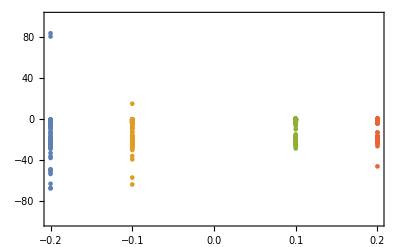

```mathematica
ListPlot[
Re@omegakcomplexTest,
PlotRange->{Automatic,{-100,100}},
Frame->True
]
```

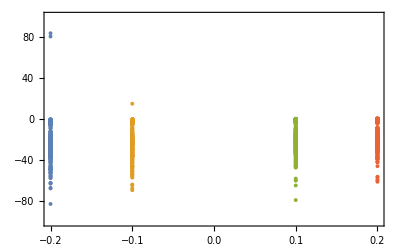

```mathematica
ListPlot[
Re@omegakcomplexTest2,
PlotRange->{Automatic,{-100,100}},
Frame->True
]
```

```mathematica
omegakcomplexC1=ToExpression@Flatten[Import["boxspectrum/export/allcomplex/omegakcomplexc1.csv"],1]
```

{{-4.5-10. ⅈ,-91.2609-64.2084 ⅈ},{-4.5-9.9 ⅈ,-92.838-64.4337 ⅈ},{-4.5-9.8 ⅈ,-91.0195-62.8715 ⅈ},18285,{4.5+9.9 ⅈ,6.24801+13.7456 ⅈ},{4.5+10. ⅈ,6.24039+13.8675 ⅈ}}
 |  |  |  |

```mathematica
omegakcomplexC1Ext=ToExpression@Flatten[Import["boxspectrum/export/allcomplex/omegakcomplexc1ext.csv"],1]
```

{{-4.5-20. ⅈ,-59.8071-83.5904 ⅈ},{-4.5-19.9 ⅈ,-55.6392-79.9026 ⅈ},{-4.5-19.8 ⅈ,-51.4883-76.2408 ⅈ},36485,{4.5+19.9 ⅈ,8.34421+36.9 ⅈ},{4.5+20. ⅈ,8.35462+37.1316 ⅈ}}
 |  |  |  |

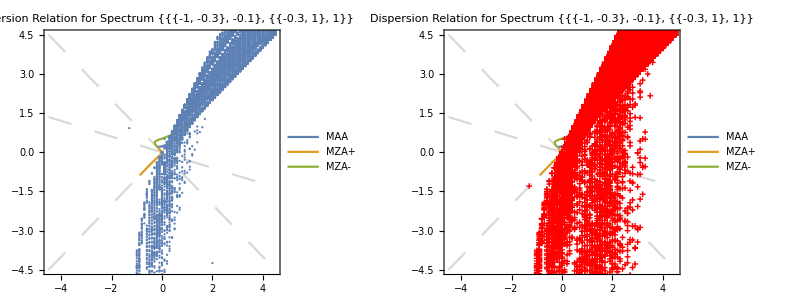

```mathematica
Grid@{{
allcomPltC1=Show[
pltDRC1,
ListPlot[
Re@omegakcomplexC1,
PlotRange->{Automatic,{-100,100}},
Frame->True
]
],

allcomPltC1Ext=Show[
pltDRC1,
ListPlot[
Re@omegakcomplexC1Ext,
PlotRange->{Automatic,{-100,100}},
Frame->True,PlotStyle->Red,PlotMarkers->{"+",6}
]

]
}}
```

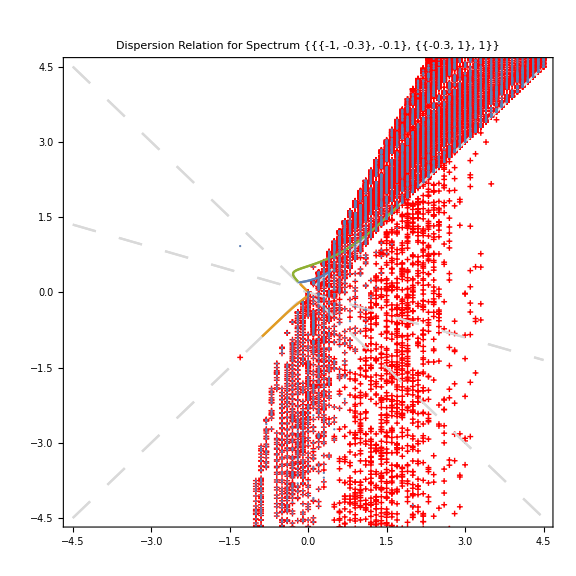

```mathematica
Show[allcomPltC1Ext,allcomPltC1]
```